# Spectroscopy and Group Theory

## Purpose

The purpose of this lesson is to...

provide some details of the theory of spectroscopy.

discuss the features of rotational, vibrational, and electronic spectra.

introduce group theory and discuss its relationship to vibrational modes and vibrational spectroscopy.

## Learning Objectives

At the end of this lesson, I should be able to...

explain which factors dictate the probability of a transition between eigenstates in a system upon interaction with light.

describe the features of rotational, vibrational, and electronic spectra and their relationship to the energy distribution of eigenstates and the spectroscopic selection rules.

identify the point groups of molecules and explain the origins of a point group’s character table.

describe the applications of point group character tables in identifying and describing the vibrational modes of a molecule.

## Born-Oppenheimer and Molecular Eigenstates

The Born-Oppenheimer approximation allows us to write the wavefunction of a molecule as a product of its nuclear and electronic components,

ψ(R, r)≈ϕ_N(R)ϕ_e(r;R)

where ϕ_e(r;R)is the electronic wavefunction and ϕ_N(R)is the nuclear wavefunction. Within this contribution, we can take the total energy of the system (molecules) as the sum of the electronic, vibrational, rotational, and translational contributions,

E_tot=E_e+E_vib+E_rot+E_trans

Let’s neglect the translational contributions for the moment. Each of the remaining contributions to the energy will have associated eigenstates given by the shape of the potential and/or the boundary conditions. For a diatomic molecule, we can visualize these molecular states in a potential energy diagram as shown in Figure 13.1. In this figure, the energies of the electronic, vibrational, and rotational eigenstates (plotted as horizontal bars) are superimposed on the electronic potential energy functions E_e(R)for different electronic states. Each of these molecular eigenstates will have a distinct wavefunction and thus distinct properties.

Figure 13.1. Depiction of the vibrational and rotational eigenstates (green and purple lines, respectively) associated with an electronic state represented by the electronic potential energy functions E_e(R)(blue lines). OpenStax, CC BY 3.0

At this point in your training as chemists, you are likely aware that transitions between these molecular eigenstates are associated with the emission or absorption of light, and we can monitor these processes to probe the structure and property of molecules in a variety of techniques that we collectively refer to as spectroscopy. In this lesson, we will address both fundamental issues of light-matter interaction (why does light of energy equal to the level spacing excite transitions?) and more practical aspects of spectroscopy (how do we interpret electronic spectra?). In all areas, we will provide only a general overview.

## The Harmonic Oscillator and Rigid Rotor as a Model for Molecular Vibrations and Rotations

### Why the Rigid Rotor?

We can directly apply the rigid rotor model to interpret the rotational energy levels of a diatomic molecule. The plot in Figure 13.1 does not display the angular dependence of the electronic energy, only the dependence on internuclear distance. However, we can certainly assume that the molecule will also be rotating in space, and we can account for this by using the rigid rotor model, wherein we assume that rotation is separate from vibration.

Remember that there is no potential energy component for rotation, meaning that V̂=0, and the energy eigenvalues of the rigid rotor are given by

E_J=ℏ^2/(2I)J(J+1)            J=0, 1, 2, ...

In other words, the energies (and eigenfunctions) of rotation are quantized. Each energy level is actually degenerate, meaning that there are multiple eigenfunctions with the same energy, and the degeneracy is given by

g_J=2J+1            J=0, 1, 2, ...

### Spacing Between Energy Levels in a Rigid Rotor

Usually at room temperature, only the ground vibrational state of a diatomic molecule is initially populated (the lowest energy eigenvalue within an electronic potential shown in Figure 13.1). In addition, the spacing between vibrational energy levels is constant (in the harmonic oscillator approximation - see below). As we discussed earlier in the course, the rotational energy levels of a molecule are a different case. The energy spacing between any two adjacent energy levels is given by

ΔE= E_(J+1)-E_J=ℏ^2/(2I)[(J+1)(J+2)-J(J+1)]

=ℏ^2/I(J+1)

As J increases, the spacing between adjacent levels also increases. In addition, the difference in energy levels is much smaller than for vibrational or electronic states, and many of these states are populated at room temperature.

### Why the Harmonic Oscillator?

Let us consider the electronic energy functions E_e(R) shown in Figure 13.1. Again, this function serves as the potential energy component of the Hamiltonian for the positions of the nuclei,

[(T̂)_N+E_e]ϕ_N(R)=E_tot ϕ_N(R)

If we neglect any net movement of the molecule in space, we can write the nuclear wavefunction in terms of internal coordinates

[(T̂)_N+E_e(R)]ψ_N(R,θ,ϕ)=E_tot ψ_N(R,θ,ϕ)

The θ and ϕ dependence would describe any rotation of the molecule. Let’s focus on only the dependence on the internuclear distance R,

[(T̂)_N+E_e(R)]ψ'_N(R)=E'_tot ψ'_N(R)

where the ' symbol denotes the portion of the wavefunction depending only on internuclear distance. Neglecting rotation and translation, this potential energy function determines the vibrational eigenstates and eigenfunctions of the molecule. The eigenvalues E'_tot give the vibrational eigenstates (vibrational energy levels) of a molecule, and the eigenfunctions ψ'_N(R)give the vibrational nuclear wavefunction, with the absolute square of ψ'_N(R)giving the probability of finding the nuclei with internuclear distance R. We will see that the harmonic oscillator provides a good approximation to the true form of the function E_e(R) for many systems, providing an easy method to calculate both the vibrational eigenvalues and eigenfunctions.

### Review - The Harmonic Oscillator Wavefunctions and Energies

Recall that the harmonic oscillator wavefunctions take the form

ψ_n(x)=N_n H_n(α^(1/2)x)ⅇ^(-αx^2/2)       n=0,1,2...

where

α=(kμ/ℏ^2)^(1/2)

N_n=1/((2^n n!)^(1/2))(α/π)^(1/4)

and

H_n(α^(1/2)x)

are the Hermite polynomials. The first few Hermite polynomials are shown in the table below.

```mathematica
Grid[Prepend[Table[{n,HermiteH[n,α^(1/2)x]},{n,0,5}],{"n","H_n (α^(1/2)x)"}],BaseStyle->{FontFamily->"Arial",FontSize->18},Frame->All]
```

n | H_n (α^(1/2)x)
0 | 1
1 | 2 x √α
2 | -2+4 x^2 α
3 | -12 x √α+8 x^3 α^(3/2)
4 | 12-48 x^2 α+16 x^4 α^2
5 | 120 x √α-160 x^3 α^(3/2)+32 x^5 α^(5/2)

The corresponding energy eigenvalues for these eigenfunctions are given by

E_n=ℏ(k/μ)^(1/2)(n+1/2)=ℏω(n+1/2)=hν(n+1/2)            n=0,1,2...

where

ν=1/(2π)(k/μ)^(1/2)

Remember that the spacing between energy levels is given by

ΔE_n=ℏ(k/μ)^(1/2)=ℏω=hν            n=0,1,2...

### The Harmonic Oscillator as a Model for a Diatomic Molecule

The harmonic oscillator does a good job of modeling the shape of the internuclear potential between two atoms. The internuclear potential describes how the potential energy E changes with the distance between the two atoms r. The solid line in Figure 13.2 shows a typical shape of such an internuclear potential for a diatomic molecule.

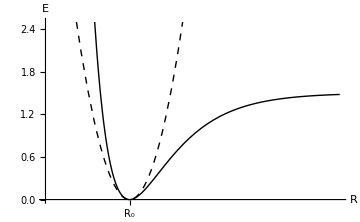

```mathematica
Clear[k]
data=Table[{x,De*(1-Exp[-a*x])^2/.{De->1.5,a->1}},{x,-1.5,2,0.1}];
fit=NonlinearModelFit[data,(1/2)*k*x^2,k,x];
Plot[{De*(1-Exp[-a*x])^2/.{De->1.5,a->1},(1/2)*k*x^2/.k->fit["ParameterTableEntries"][[1,1]]},{x,-2,5},PlotRange->{{-2,5},{0,2.5}},BaseStyle->{FontFamily->"Arial",FontSize->16},PlotStyle->{Directive[Black,Thick],Directive[Black,Thick,Dashed]},AxesStyle->Directive[Thick,Black],TicksStyle->Directive[Black, Thick],Ticks->{{{0,"R_0"}},None},ImageSize->Medium, Exclusions->None,AxesOrigin->{-2,0},AxesLabel->{"R","E"}]
```

Figure 13.2. An exemplary internuclear potential for a diatomic molecule (solid line) can be approximated by a harmonic oscillator potential (kr^2/2) in the region around the equilibrium internuclear distance R_0.

The minimum of the potential, marked by R_0, corresponds to the equilibrium internuclear distance, which we would typically call the bond length. At lower values of R, the potential energy rises steeply as the two atoms repel each other. At larger values of R, the potential energy increases more slowly and eventually levels off as the two atoms are far enough apart that they no longer interact. In the region around R_0, the shape of the potential can be approximated as that of a harmonic oscillator, as shown by the dashed line in Figure 13.2.

In the case of an internuclear potential similar to that shown in Figure 13.2, the harmonic approximation can do a fairly good job of predicting the energies of the ground state and first excited state. That’s because at lower energies, the correspondence between the harmonic approximation (dashed line) and the true potential (solid line) is best. The eigenstates (wavefunctions) and eigenvalues (energies) for the harmonic approximation of the diatomic are plotted in Figure 13.3. We’ll talk more about anharmonicity and the failings of the harmonic approximation as we go along.

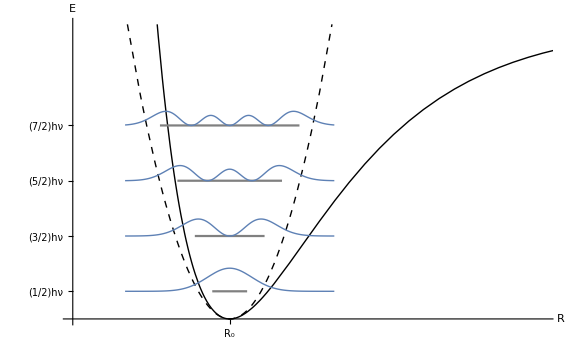

```mathematica
h=1;
μ=1;
k=fit["ParameterTableEntries"][[1,1]];
ν=(1/(2*π))(k/μ)^(1/2);
α=((4 π^2*k*μ)/h^2)^(1/2);
norm=1/((2^n n!)^(1/2))(α/π)^(1/4);
energies=
Table[h*ν*(n+1/2),{n,0,5}];
Eplotlabels=Table["("<>ToString[InputForm[(2n+1)/2]]<>")",{n,0,5}];
energiesplot=
Table[{{-(1/6)*(n+1),energies[[n+1]]},{(1/6)*(n+1),energies[[n+1]]}},{n,0,5}];
potential=(1/2)*k*x^2;
wf=Table[0.05*norm*HermiteH[n,α^(1/2)x]*Exp[-α*x^2/2]+energies[[n+1]],{n,0,5}];
wfsquared=Table[(0.25*norm*HermiteH[n,α^(1/2)x]*Exp[-α*x^2/2])^2+energies[[n+1]],{n,0,5}];
Show[
Plot[{De*(1-Exp[-a*x])^2/.{De->1.5,a->1},(1/2)*k*x^2/.k->fit["ParameterTableEntries"][[1,1]]},{x,-2,5},PlotRange->{{-1.5,3},{0,1.5}},BaseStyle->{FontFamily->"Arial",FontSize->16},PlotStyle->{Directive[Black,Thick],Directive[Black,Thick,Dashed]},AxesStyle->Directive[Thick,Black],TicksStyle->Directive[Black, Thick],Ticks->{{{0,"R_0"}},Table[{energies[[n+1]],Eplotlabels[[n+1]]<>"hν"},{n,0,3}]},ImageSize->Large, Exclusions->None,AxesOrigin->{-1.5,0},AxesLabel->{"R","E"}]
,
ListLinePlot[energiesplot[[1;;4]],PlotStyle->Directive[Gray]]
,
Plot[wfsquared[[1;;4]],{x,-1,1},PlotRange->All,PlotStyle->Thick]
]
```

Figure 13.3. The solutions to the harmonic oscillator approximation for a model diatomic, plotting the absolute square of the wavefunction, |ψ(x)|^2 (blue), offset by the energies along the potential. The approximation is better for the lower-energy states because the real potential more closely corresponds to a harmonic potential at lower energies.

It turns out that this approximation works well not only for diatomic molecules but for really almost any molecular vibration. If you calculate the vibrational frequencies of a molecule using some computational chemistry program, the software will certainly use the “harmonic approximation”, that is, approximating the vibrational potentials to be harmonic. However, these vibrations don’t always correspond to just two atoms moving apart; in larger molecules, they typically involve the motion of many atoms. These vibrations are found as what we call the normal modes of a coupled system of harmonic oscillators, but we won’t discuss how these normal modes are found in this course.

### An Improved Approximation for Diatomic Molecules: The Morse Potential

As seen in Figures 13.2 and 13.3, the harmonic oscillator approximation is not very accurate at extended internuclear distances (large values of R). In these regions, the harmonic potential continues to increase, whereas the true potential levels off as the nuclei approach infinite separation. As a result, the harmonic approximation is not very accurate for higher energy eigenvalues and cannot correctly predict the dissociation of the molecule (all energy eigenvalues are stable within the harmonic potential). An improved model of the potential for diatomic molecules is provided by the Morse potential,

V(R)=D_e(1-e^(-β(R-R_0)))^2

where D_e is the dissociation energy, the energy at which the molecule dissociates, and β describes the shape of the curve around the equilibrium internuclear distance R_0. The energy eigenvalues of the Morse potential are given by

E_n=ℏ(k/μ)^(1/2)(n+1/2)-ℏ^2/(4 D_e)(k/μ)(n+1/2)^2          n=0,1,2...

where the upper limit of the integer n is given by the condition that E_n< D_e. Shown in Figure 13.4 are the eigenfunctions and eigenvalues of the Morse potential. There are two important differences from the harmonic oscillator to note. First, the spacing between energy levels is not constant but rather decreases as n increases. Second, the amplitude of the wavefunction increases at larger values of R as n increases, meaning that the most probable bond length also increases with increasing energy.

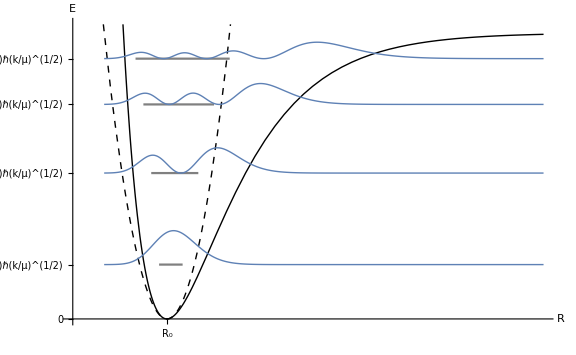

```mathematica
ℏ=1;
μ=1;
De=50;
a=2;
λ=(2*μ*De)^(1/2)/(a*ℏ);
z=2*λ*ⅇ^-x;
norm=((n!*(2λ-2n-1))/Gamma[2λ-n])^(1/2);
ψ=norm*z^(λ-n-1/2)ⅇ^(-(1/2)z)LaguerreL[n,2λ-2n-1,z];
ϵ=
Table[-(λ-n-1/2)^2,{n,0,5}];
energies=((a^2*ℏ^2)/(2*μ))*ϵ;
harmenergies=
Table[ℏ*(De*a^2*2/μ)^(1/2)*(n+1/2)-De,{n,0,5}];
harmenergiesplot=Table[{{-(1/6)*(n+1),harmenergies[[(n+1)]]},{(1/6)*(n+1),harmenergies[[(n+1)]]}},{n,0,5}];
wfsquared=Table[5*ψ^2+energies[[n+1]],{n,0,5}];
energiesplot=
Table[{{-(1/8)*(n+1),energies[[(n+1)]]},{(1/4)*(n+1),energies[[(n+1)]]}},{n,0,5}];
Eplotlabels=Table["("<>ToString[N[(-(-De-energies[[n+1]]))/(ℏ*(2*De*a^2/μ)^(1/2))]]<>")",{n,0,5}];
Show[
Plot[{De*(Exp[-2x]-2Exp[-x]),(1/2)*k*(x/a)^2-De/.k->De*a^2*2},{x,-1.5,6},PlotRange->{{-1.5,6},{-50,1.5}},BaseStyle->{FontFamily->"Arial",FontSize->16},PlotStyle->{Directive[Black,Thick],Directive[Black,Thick,Dashed]},AxesStyle->Directive[Thick,Black],
Ticks->{{{0,"R_0"}},Prepend[Table[{energies[[n+1]],Eplotlabels[[n+1]]<>"ℏ(k/μ)^(1/2)"},{n,0,3}],{-De,"0"}]},
TicksStyle->Directive[Black, Thick],ImageSize->Large, Exclusions->None,AxesOrigin->{-1.5,-50},AxesLabel->{"R","E"}]
,
ListLinePlot[energiesplot[[1;;4]],PlotStyle->Directive[Gray]]
,
Plot[wfsquared[[1;;4]],{x,-1,6},PlotRange->All,PlotStyle->Thick]
]
```

Figure 13.4. The solutions to the quantum mechanical Morse potential (black curve), plotting the absolute square of the wavefunction, |ψ(x)|^2, in blue. The energy eigenvalues are marked with gray lines, and the harmonic approximation potential is shown as a dashed black line.

## Light-Matter Interactions and Perturbation Theory

### Introduction to Time-Dependent Perturbation

Up to this point, we haven’t really worked very much with the evolution of a system in time, but we now want to look at the change in a system (molecule) upon its interaction with light, for which we will need some form of time-dependent formalism. First, recall from our discussion of the fifth postulate of quantum mechanics that the wavefunction of an unperturbed system in an eigenstate j changes in time only by a “phase factor” given by an oscillatory complex exponential,

|ψ_j(t)⟩=ⅇ^(-ⅈE_jt/ℏ)|ψ_j⟩

Note that the ket on the left-hand-side has a time dependence, whereas the one on the right-hand-side does not. What if our system is not in an energy eigenstate? Then we can instead write the time-dependent wavefunction of the system as a linear combination of the energy eigenstates, which we will label as|n⟩ for simplicity,

|ψ(t)⟩=∑_n c_n(t)ⅇ^(-ⅈE_nt/ℏ)|n⟩

where the coefficients c_n(t)give the contribution of each basis eigenfunction in time (along with the exponential factor). The square of the coefficients c_n(t)will give us the probability that the system is in state |n⟩ at time t.

Remember that the wavefunction |ψ (t)⟩ is a solution to the time-dependent Schrödinger equation,

ⅈℏ ∂/(∂t)|ψ(t)⟩=Ĥ (t)|ψ(t)⟩

Let us now separate the Hamiltonian operator into time-independent and time-dependent components in a perturbation formulation,

Ĥ (t)=(Ĥ)^(0)+(Ĥ)^(1)(t)

Because we are interested in the interaction of the system with light, which is just an oscillating electromagnetic potential, we can label the time-dependent component as V(t),

Ĥ (t)=(Ĥ)^(0)+V(t)

Substituting equations (20) and (23) in the time-dependent Schrödinger equation, we obtain

∑_n (ⅈℏ(∂c_n(t))/(∂t)+E_n c_n(t))ⅇ^(-ⅈE_nt/ℏ)|n⟩=∑_n (E_n+V(t))c_n(t)ⅇ^(-ⅈE_nt/ℏ)|n⟩

where we have used the product rule of differentiation on the left-hand side, and we have used the relation

(Ĥ)^(0)|n⟩=E_n|n⟩

Note that the term E_n c_n(t)ⅇ^(-ⅈE_nt/ℏ)|n⟩ appears on both sides of the equation and thus cancels out to yield

∑_n ⅈℏ((∂c_n(t))/(∂t))ⅇ^(-ⅈE_nt/ℏ)|n⟩=∑_n V(t)c_n(t)ⅇ^(-ⅈE_nt/ℏ)|n⟩

Now we take the inner product with the bra state ⟨m|ⅇ^(ⅈE_m t/ℏ) to obtain

∑_n ⅈℏ((∂c_n(t))/(∂t))ⅇ^(ⅈE_m t/ℏ-ⅈE_n t/ℏ)⟨m|n⟩=∑_n ⟨m|V(t)|n⟩c_n(t)ⅇ^(ⅈE_m t/ℏ-ⅈE_n t/ℏ)

because m and n are eigenfunctions of the Hamiltonian operator, which is Hermitian, they are orthogonal. Therefore, we have that

⟨m|n⟩=δ_mn

and the equation simplifies to

(∂c_m(t))/(∂t)=-ⅈ/ℏ∑_n ⟨m|V(t)|n⟩c_n(t)ⅇ^(ⅈ(E_m-E_n)t/ℏ)

Remember that the coefficients c_m(t)are the weighting coefficients applied to the eigenfunctions of the time-independent Schrödinger equation, so this equation describes how the population of these states changes with time upon interaction with the external potential V(t) (which could be, for example, the electromagnetic field of light). To simplify the equation slightly, usually we use the definitions

V_mn(t)=⟨m|V(t)|n⟩
ω_mn=(E_m-E_n)/ℏ

which give

(∂c_m(t))/(∂t)=-ⅈ/ℏ∑_n V_mn(t)c_n(t)ⅇ^(ⅈω_mn t)

Now, let’s examine a hypothetical system in eigenstate |k⟩ at time t = 0. In other words

c_n(0)=δ_nk

Equation (31) then becomes

(∂c_m(t))/(∂t)=-ⅈ/ℏ V_mk(t)ⅇ^(ⅈω_mk t)+-ⅈ/ℏ∑_(n≠k) V_mn(t)c_n(t)ⅇ^(ⅈω_mn t)

where we have removed the term for the initial state from the sum. Now, assuming that the weighting coefficients c_n(t)≈0 because c_k(t)≈1, the sum can be approximately neglected, yielding

(∂c_m^(1)(t))/(∂t)=-ⅈ/ℏ V_mk(t)ⅇ^(ⅈω_mk t)

where the superscript in c_m^(1) indicates that this is a first-order approximation for the weighting coefficients. Integration then yields

c_m^(1)(t)=-ⅈ/ℏ∫_0^t V_mk(t')ⅇ^(ⅈω_mk t')ⅆt'

which gives an equation for the weighting coefficients for a state upon interaction with a potential V(t). Note that the square of these weighting coefficients gives the probability of finding the system in state c_m at time t.

### Interaction with a Sinusoidal Potential

Let us now examine what happens to the weighting coefficients upon interaction with a sinusoidal potential (for example, light). Let us write the potential as

V(r,t)=2V(r)cos(ωt)=V(r)(ⅇ^ⅈωt+ⅇ^-ⅈωt)

Note that the potential depends not only on time but also on position and orientation, which will be very important later on. For now, let’s think only about the time portion. For the system in starting state |k⟩, using our first-order approximation for the weighting coefficients, we obtain

c_m^(1)(t)=-ⅈ/ℏ V_mk∫_0^t (ⅇ^ⅈωt'+ⅇ^-ⅈωt')ⅇ^(ⅈω_mk t')ⅆt'

where the expression

V_mk=⟨m|V(r)|k⟩

no longer depends on time (the time dependence has been separated), so we can remove it from the integral. Rearranging, we obtain

c_m^(1)(t)=-ⅈ/ℏ V_mk∫_0^t (ⅇ^(ⅈ(ω_mk+ω)t')+ⅇ^(ⅈ(ω_mk-ω)t'))ⅆt'

because we are taking an integral over time on oscillatory functions, the average value will be zero unless

ω_mk±ω≈0

which would yield an increase in the weighting coefficient of state |m⟩ with time. We can rewrite the conditions of equation (40) as

ω_mk=∓ω
(E_m-E_k)/ℏ=∓ω
E_m-E_k=∓ℏω
E_m=E_k∓ℏω

Now, the negative sign would correspond to the emission of a photon of energy ℏω (stimulated emission), and the positive sign would correspond to the absorption of a photon of energy ℏω. If we separate equation (39) into two integrals,

c_m^(1)(t)=-ⅈ/ℏ V_mk[∫_0^t ⅇ^(ⅈ(ω_mk+ω)t')ⅆt'+∫_0^t ⅇ^(ⅈ(ω_mk-ω)t')ⅆt']

then (in general) only one of the integrals will be nonzero, depending on whether the final state is above or below the initial state in energy. Let’s look at the case of absorption of radiation,

c_m^(1)(t)=-ⅈ/ℏ V_mk∫_0^t ⅇ^(ⅈ(ω_mk-ω)t')ⅆt'
	       =-ⅈ/ℏ V_mk(ⅈ (ⅇ^(ⅈ (ω_mk-ω) t)-1))/(ω-ω_mk)
	       =-ⅈ/ℏ V_mk ⅇ^(ⅈ (ω_mk-ω) t/2)2[(ⅇ^(ⅈ (ω_mk-ω) t/2)-ⅇ^(-ⅈ (ω_mk-ω) t/2))/(2ⅈ(ω_mk-ω))]
	       =-ⅈ/ℏ V_mk ⅇ^(ⅈ (ω_mk-ω) t/2)(2sin((ω_mk-ω) t/2))/(ω_mk-ω)

Remember that the probability of finding the system in state |m⟩ at time t is given by the absolute square of the weighting coefficient,

P_m(t)=|c_m^(1)(t)|^2    =V_mk^2/ℏ^2(4 sin^2((ω_mk-ω) t/2))/(ω_mk-ω)^2

Figure 13.5 shows a plot of the probability at some fixed time t as a function of the difference between the light frequency ω and ω_mk. Note that the probability of absorption is highest when  ω=ω_mk.

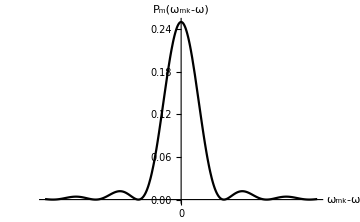

```mathematica
Plot[Sin[a*t/2]^2/(a)^2/.t->1,{a,-20,20},BaseStyle->{FontFamily->"Arial",FontSize->14},PlotStyle->Directive[Black,PointSize[Large]],AxesStyle->Directive[Thick,Black],Ticks->{{0},None},ImageSize->Medium, Exclusions->None,AxesOrigin->{0,0},AxesLabel->{"ω_mk-ω","P_m(ω_mk-ω)"}]
```

Figure 13.5. Plot of the probability P_m(ω_mk-ω)of finding the system in state |m⟩ at some fixed time t as a function of the difference between the light frequency ω and ω_mk.

As time increases, the distribution will narrow around ω_mk-ω=0, and the equation can be written as a delta function,

P_m(t)=V_mk^2/ℏ^2 2π δ(ω_mk-ω)t=V_mk^2/ℏ 2π δ(E_m-E_k-ℏω)t

Note that the probability to be in the final state |m⟩ increases linearly with time. This approximation, however, assumes a small value of c_m^(1)(t), so it becomes invalid if this probability is large.

We now have a fundamental basis for the requirement we have always discussed regarding transitions between eigenstates and their relation to the frequency (and thus energy) of the incident radiation: the energy of the light must match the difference in energy of the eigenstates to have a high probability of absorption.

### The Dipole Moment and Transition Probability

Equation (45) gives an expression for the probability of finding a system in state |m⟩ following interaction with a sinusoidal potential. For the case of interaction with light, the previous section focused on the requirement that the energy of the light equal the difference in energy between the two states. However, we have not yet discussed the influence of the V_mk term on the transition probability. For linearly polarized light, this term depends on the projection of the molecular electric dipole moment onto the electric field vector, which is given by the scalar product

2V(r)=μ·E_0

where μ is the dipole moment and E_0 is the light electric field amplitude vector. Using this expression, V_mk becomes

V_mk=⟨m|μ·E_0|k⟩

Because the states m and k have no dependence on the electric field vector E_0, this value can be removed from the bra-ket to yield

V_mk=⟨m|μ|k⟩·E_0

We now define the transition dipole moment ⟨μ⟩_mk as

⟨μ⟩_mk=⟨m|μ|k⟩

Note that the probability of finding a molecule in state |m⟩ is proportional to the absolute square of V_mk, so the intensity of a band in a spectroscopic experiment is strongly dependent on this quantity.

### Selection Rules of a Rigid-Rotor

When discussing the rigid rotor approximation, we briefly mentioned the spectroscopic selection rule

ΔJ=±1

where J is the quantum number describing the allowed energy eigenvalues of the rigid rotor,

E_J=ℏ^2/(2I)J(J+1)            J=0, 1, 2, ...

Now we will use the perturbation theory equations derived in the previous sections to investigate the origins of this selection rule for rigid-rotor diatomic molecules. First, let us assume that a molecule is interacting with linear-polarized light whose electric field points along some arbitrary z-axis in the laboratory frame. Equation (48) then becomes

V_mk=⟨m|μ cos(θ)|k⟩E_z

where we have used the fact that μ·E_0=μ_z E_z=μ cos(θ)E_z. The variable μ is now a scalar quantity giving the magnitude of the vector, and θ is the angle between the molecular dipole moment and the z axis. Remember that the eigenfunctions for the rigid rotor in spherical coordinates are the spherical harmonics (there is no dependence on the internuclear distance r because it is fixed). Therefore, the transition dipole moment becomes

⟨Y_J'^M'(θ,ϕ)|μ cos(θ)|Y_J^M(θ,ϕ)⟩=μ ⟨Y_J'^M'(θ,ϕ)|cos(θ)|Y_J^M(θ,ϕ)⟩

where the sets of quantum numbers, J, M and J’, M’ specify the initial and final states of the system, respectively. Integration in spherical coordinates yields

μ ⟨Y_J'^M'(θ,ϕ)|cos(θ)|Y_J^M(θ,ϕ)⟩=μ ∫_0^(2π) ∫_0^π Y_J'^M'(θ,ϕ)^⋆Y_J^M(θ,ϕ)cos(θ)sin(θ)ⅆθⅆϕ

Importantly, notice that if the magnitude of the molecular dipole moment is zero, then the transition dipole moment will also be zero, giving zero probability of a transition between states. This result is the origin of the requirement that molecules have a permanent dipole moment to observe a rotational spectrum. To solve the integral in equation (54), we must first break the spherical harmonics into their constituent components. Remember that spherical harmonics take the form

Y_J^M(θ,ϕ)=N_JM P_J^(|M|)(cosθ)ⅇ^ⅈMϕ

where N_JM is a normalization constant and P_J^(|M|)(cosθ)is an associated Legendre function. If we make the substitution u = cos θ , we obtain

μ ∫_0^(2π) ∫_0^π Y_J'^M'(θ,ϕ)^⋆Y_J^M(θ,ϕ)cos(θ)sin(θ)ⅆθⅆϕ=μ N_J'M' N_JM∫_0^(2π) ⅇ^(ⅈ(M-M')ϕ)ⅆϕ   ∫_-1^1 u P_J'^(|M'|)(u)P_J^(|M|)(u)ⅆu

The first integral yields a value of zero unless M=M', giving the first selection rule of

ΔM=0

The second integral in equation (56) is more complicated to evaluate, and we won’t go through the details. In short, this integral yields a value of zero unless J'=J+1 or J'=J-1, giving the second selection rule

ΔJ=±1

### Selection Rules of a Harmonic Oscillator

Now let’s consider not only the rotational states of a rigid-rotor/harmonic oscillator molecule but also the vibrational states. In addition to fulfilling the rotational selection rules outlined above, now we must consider the dependence of the transition dipole moment on the change in the internuclear distance(s). Using the harmonic approximation, the nuclear eigenfunctions for a given vibrational coordinate q are given by

ψ_n(q)=N_n H_n(α^(1/2)q)ⅇ^(-αq^2/2)

where N_n is a normalization constant, H_n is a Hermite polynomial, α=(k m_red/ℏ^2)^(1/2), and n is the quantum number specifying the n^th eigenfunction of the vibrational potential. The displacement coordinate q gives the net displacement of the atoms along the vibration’s displacement vector (we’ll discuss vibrational modes and normal coordinates more later). For a given vibration, neglecting the rotational selection rules, the transition dipole moment is then

⟨ψ_n'(q)|μ_z(q)|ψ_n(q)⟩=∫_(-∞)^∞ N_n' H_n'(α^(1/2)q)μ_z(q)N_n H_n(α^(1/2)q)ⅇ^(-αq^2)ⅆq

where μ_z(q)is the displacement-dependent projection of the molecular dipole moment onto the laboratory-frame z-axis. To obtain the dependence of μ_z on q, we would in principle have to determine the value of the dipole moment at each position along the vibrational coordinate. However, we can approximate the dependence of μ_z on q through a Taylor series expansion about the equilibrium bond distance q=0,

μ_z(q)=μ_z(0)+((ⅆ μ_z)/ⅆq)_(q=0)q+...

substituting into equation (60), we obtain

⟨ψ_n'(q)|μ_z(q)|ψ_n(q)⟩=⟨ψ_n'(q)|μ_z(0)|ψ_n(q)⟩+⟨ψ_n'(q)|((ⅆ μ_z)/ⅆq)_(q=0)q|ψ_n(q)⟩

We can remove μ_z(0)from the first bra-ket term because it does not depend on q,

⟨ψ_n'(q)|μ_z(0)|ψ_n(q)⟩=μ_z(0)⟨ψ_n'(q)|ψ_n(q)⟩

because the Hermite polynomials are orthogonal, this term will equal zero unless n'=n. For the second term, the derivative can be removed from the bra-ket to give

⟨ψ_n'(q)|((ⅆ μ_z)/ⅆq)_(q=0)q|ψ_n(q)⟩=((ⅆ μ_z)/ⅆq)_(q=0)⟨ψ_n'(q)|q|ψ_n(q)⟩
						       =((ⅆ μ_z)/ⅆq)_(q=0)⟨N_n' H_n'(α^(1/2)q)ⅇ^(-αq^2/2)|q|N_n H_n(α^(1/2)q)ⅇ^(-αq^2/2)⟩

Note that the change in the dipole moment during the vibration must be nonzero in order for the transition dipole moment to be nonzero. To evaluate the bra-ket term, we first rewrite equation (64) as

((ⅆ μ_z)/ⅆq)_(q=0)(N_n' N_n)/α^(1/2)⟨H_n'(α^(1/2)q)ⅇ^(-αq^2/2)|α^(1/2)q|H_n(α^(1/2)q)ⅇ^(-αq^2/2)⟩

Now, we use a special identity of the Hermite polynomials,

u H_n(u)=n H_(n-1)(u)+1/2 H_(n+1)(u)

using the substitution u=α^(1/2)q, equation (65) becomes

((ⅆ μ_z)/ⅆq)_(q=0)(N_n' N_n)/α^(1/2)⟨H_n'(u)ⅇ^(-u^2/2)|u|H_n(u)ⅇ^(-u^2/2)⟩
=((ⅆ μ_z)/ⅆq)_(q=0)(N_n' N_n)/α^(1/2)∫_(-∞)^∞ H_n'(u)[n H_(n-1)(u)+1/2 H_(n+1)(u)]ⅇ^(-u^2)ⅆu

Because the Hermite polynomials are orthogonal, the integral in equation (67) will return a value of zero unless n'=n±1, giving the vibrational transition selection rule of

Δn=±1

Note that this rule is valid only when we ignore higher-order terms in the Taylor series expansion and assume a harmonic oscillator wavefunction, so other transitions are possible in real systems, but the probability of the transition (and thus the intensity of the band in a spectrum) will be much smaller than for the “allowed” transitions.

### Selection Rules for Electronic Transitions

The selection rules for electronic transitions are a bit more complicated than those for the rigid rotor/harmonic oscillator model. This complexity results from the fact that the transition dipole moment now also depends on the electronic component of the wavefunction (as opposed to just the nuclear component in the cases studied thus far). We can write the transition dipole moment as

⟨μ⟩=⟨ψ'(R, r)|μ_e+μ_N|ψ(R, r)⟩

where we have separated the dipole moment into its nuclear and electronic components. If we write the wavefunction as a product of the electronic, vibrational, and rotational components,

ψ(R, r)≈ϕ_vib(R)ϕ_rot(R)ϕ_e(r;R)

we can then write the dipole moment as

⟨μ⟩=∫∫ϕ'_vib(R)^⋆ϕ'_e(r,R)^⋆(μ_e+μ_N)ϕ_vib(R)ϕ_e(r,R)ⅆrⅆR∫_0^(2π) ∫_0^π Y_J'^M'(θ,ϕ)^⋆Y_J^M(θ,ϕ)cos(θ)sin(θ)ⅆθⅆϕ

where the rotational component takes a similar dependence as we saw above (assuming a rigid rotor). Neglecting the rotational component, we can rewrite the vibrational/electronic integral as

⟨μ⟩=∫ϕ'_e(r,R)^⋆μ_e ϕ_e(r,R)ⅆr∫ϕ'_vib(R)^⋆ϕ_vib(R)ⅆR+∫ϕ'_e(r,R)^⋆ϕ_e(r,R)ⅆr∫ϕ'_vib(R)^⋆μ_N ϕ_vib(R)ⅆR

where we have separated the integral into two parts based on the μ_e and μ_N terms. The second set of integrals will always yield zero because of the orthogonality of the electronic states, leaving us with

⟨μ⟩=∫ϕ'_e(r,R)^⋆μ_e ϕ_e(r,R)ⅆr∫ϕ'_vib(R)^⋆ϕ_vib(R)ⅆR

Note that the vibrational wavefunctions here are in different electronic states and thus are not necessarily orthogonal. In fact, this equation shows that the transition dipole moment depends on the overlap between the initial and final vibrational wavefunctions, which is the basis of the Franck-Condon principle. The selection rules for the electronic component are more complicated, and we won’t cover them in more detail at this moment. We went over some of these rules in the lesson on multielectron atoms.

## Characteristics of Rotational, Vibrational, and Electronic Spectra

### Rotational (Microwave) Spectra

#### Rotational Spectra of Linear Rigid Rotor

We’ve already discussed the properties of the rotational spectra of rigid rotors, but we’ll review them again here briefly. The energy eigenvalues of a rigid rotor are given by

E_J=ℏ^2/(2I)J(J+1)            J=0, 1, 2, ...

and the spacing between energy levels is given by

ΔE= E_(J+1)-E_J=ℏ^2/I(J+1)=2Bh(J+1)

where the rotational constant B is defined as

B=h/(8 π^2 I)

The rotational constant is also often written in wavenumbers as

B^∼=B/c=h/(8 π^2 Ic)

SI units on the right-hand side will give units for B^∼ of m^-1, but this value is usually expressed in cm^-1. The spacing between bands in the rotational spectrum of a diatomic molecule is 2B in frequency or 2 B^∼ in cm^-1. Because absorption of a photon can only yield a transition from state J to state J+1, the distribution of spectral lines depends upon the initial population distribution, which is in turn given by the temperature. A model rotational spectrum of an idealized rigid rotor is shown in Figure 13.6.

```mathematica
Manipulate[
dat=Thread[{freq,int[ratio]}];  

spec=ListPlot[dat,PlotMarkers->None,Axes->{True,False},PlotRange->{{0,28},{0,4.4}},Filling->Axis,FillingStyle->Thickness[.008],
Ticks->{Thread[{freq,labels}],{None}},TicksStyle->Darker[Gray],AxesLabel->{Style["ν^,",24,Red],None},AspectRatio->1]; 
specline=Graphics[{Red,Thickness[.01],Line[{{freq[[J+1]],0},{freq[[J+1]],int[ratio][[J+1]]}}]}];

arrow1=If[J==0,Graphics[{Red,Thickness[.02],Arrowheads[Small],Arrow[{{.5,En[J]+.7},{.5,En[J+1]}}]}],Graphics[{Red,Thickness[.01],Arrowheads[Medium],Arrow[{{.5,En[J]},{.5,En[J+1]}}]}]];

tlabel=Graphics[Style[Text[Row[{"ΔE = ",ToString[NumberForm[En[J+1]-En[J],2]],"B̄"}],{1.25,118}],Italic,Red,16]];

GraphicsRow[{Show[spec,specline],
Show[levels,arrow1,tvec,tvecA,tlabel,tJ,Axes->False,AspectRatio->1.5,PlotRange->{{0,7},{-5,122}}]
},ImageSize->{600,400}],

{{ratio,3,label2},1.,25.,Appearance->"Labeled"},

{{J,0,Style["J_i",Italic,FontFamily->"Times"]},0,9,1},
ControlType->{Slider,SetterBar},TrackedSymbols:>{ratio,J},
Initialization:>(En[Jp_]:=Jp (Jp+1) ;(*rotational levels E/hB*)
freq=Table[j,{j,2,28,2}];  
labels=Table[Row[{j,OverBar[Style["B",Italic]]}],{j,2,28,2}];
label2=Text[Style[Row[{Style["k_BT",Italic],"/",Style["hc",Italic],OverBar[Style["B",Italic]]}]]];

(*J=Ji, INITIAL state for upward transition*)
int[xp_]:=Table[(2. Jp+1.) Exp[-(Jp^2+Jp)/xp],{Jp,0,13}] ;  (*intensity*)
tvec=Table[Graphics[Text[Style[ToString[NumberForm[j,1]],Italic,16],{1.28,j (j+1)}]],{j,1,10}];
tvecA=Graphics[Text[Style["0",Italic,12],{1.24,-2}]];
tJ=Graphics[Rotate[Text[Style[Row[{"J_i"," values"}],14],{1.95,60}],Pi/2.]];

levels=Plot[Table[j (j+1),{j,0,11}],{x,0,1},PlotStyle->{Thick,Black},PlotRange->{{0,2},{-3,140}},AspectRatio->1];
)]
```

Part::partw: Part 5 of {1.,2.62552,3.3516,3.1453,2.37237,1.48869,0.790531}[17.75] does not exist.

Part::partw: Part 5 of {1., 2.62552, 3.3516, 3.1453, 2.37237, 1.48869, 
      0.790531}[17.75] does not exist.

Part::partw: Part 5 of {1.,2.62552,3.3516,3.1453,2.37237,1.48869,0.790531}[17.75] does not exist.

Figure 13.6. Idealized rotational spectrum of a rigid rotor, where each spectral line corresponds to a transition between state J and state J + 1. Changing the temperature alters the initial state population distribution, thereby altering the spectrum. Wolfram Demonstrations, Porscha McRobbie and Eitan Geva (March 2011), CC BY-NC-SA, https://demonstrations.wolfram.com/TemperatureDependentRotationalEnergySpectrum/

The true spacing of bands decreases with J due to a phenomenon known as centrifugal distortion, in which the increasing angular momentum leads to an increase in the bond length and a decrease in the energy spacing relative to an ideal rigid rotor.

#### Beyond the Linear Rigid Rotor

Of course, there are many molecules that are nonlinear, and the rotational spectrum cannot be accurately represented by a single rigid rotor. Although we won’t cover the properties of the rotational spectra of such polyatomic molecules in detail, we provide a brief overview here. In short, the moment of inertia can always be represented in a molecule-based coordinate system with axes a, b, and c by the three components I_a, I_b, and I_c, where by convention

I_a≤I_b≤I_c

There are then four classes of molecules that are defined by the values of the moment of inertia: linear, spherical top, symmetric top, and asymmetric tops. Linear molecules have moment of inertia I_a<<I_b=I_c and behave as rigid rotors. Spherical tops have moment of inertia I_a=I_b=I_c and have the same energy levels as a rigid rotor (albeit with a greater number of degenerate states). Note that spherical tops do not have a dipole moment, so they don’t typically have a pure rotational spectrum.

Symmetric top molecules have two moment of inertia that are the same, either I_a=I_b<I_c (oblate top) or I_a<I_b=I_c (prolate top). The energy levels of each state are given by

E_J=BJ(J+1)+(A-B)K^2          J=0, 1, 2,...        K=0, 1, 2,...

where

B=h/(8 π^2 I_B)

and

A=h/(8 π^2 I_A) (prolate top)                A=h/(8 π^2 I_C) (oblate top)

Note that the spacing between J levels for a given value of K is the same as for a linear rigid rotor (neglecting centrifugal distortion).

For an asymmetric top, there is no formula for calculating the energy levels. Instead, one must solve a matrix eigenvalue problem in a basis of the rotation matrix functions. We unfortunately don’t have time to discuss this problem in more detail.

### Rotational-Vibrational Spectra

Previously when discussing vibrational transitions, we have neglected any rotational transitions. However, thinking back to the energy diagram in Figure 13.1, we see that rotational transitions always accompany vibrational transitions. The overall allowed transitions are subject to the selection rules for both vibrational and rotational states. An idealized rotational-vibrational spectrum for a single vibrational transitions of a linear rigid rotor is shown in Figure 13.7. Two series of rotational transitions are observed: those corresponding to Δ J=+1 (the R-branch) and those corresponding to Δ J=-1 (the P-branch). If the ground state has nonzero orbital and/or spin angular momentum, then Δ J=0 transitions are also allowed, giving a Q-branch.

```mathematica
Manipulate[
Plabel=Graphics[Style[Text[Row[{"Δ",Style["E",Italic]," = ","ν̄",ToString[NumberForm[En[Jp]-En[Jpp],2]],OverBar[Style["B",Italic]]}],{1.1,155}],Red,18]];
Rlabel=Graphics[Style[Text[Row[{"Δ",Style["E",Italic]," = ","ν̄ + ",ToString[NumberForm[En[Jp]-En[Jpp],2]],OverBar[Style["B",Italic]]}],{1.1,155}],Blue,18]];

Parrow=Graphics[{Red,Thickness[.015],Arrowheads[Medium],Arrow[{{.5,En[Jpp]},{.5,En[Jp]+offset}}]}];
Rarrow=Graphics[{Blue,Thickness[.015],Arrowheads[Medium],Arrow[{{.5,En[Jpp]},{.5,En[Jp]+offset}}]}];
error=Graphics[Rotate[Text[Style["Forbidden!",Orange,35],{.5,60}],.5 Pi]];

(*Intensities are relative to GS within each manifold. Intensity of Jth level=(2J+1)Exp[-J(J+1)hB/kT]*)
Pline=Graphics[{Red,Thickness[.01],Line[{{nu-2. (Jp+1),0},{nu-2. (Jp+1),(2. Jp+1.) Exp[-(Jp^2+Jp)/x]}}]}];
Rline=Graphics[{Blue,Thickness[.01],Line[{{nu+2. (Jpp+1),0},{nu+2. (Jpp+1),(2. Jpp+1.) Exp[-(Jpp^2+Jpp)/x]}}]}];

out2=Which[Jpp<Jp&&Jp==Jpp+1,Show[Elevels,Rlabel,Rarrow,Axes->False,PlotRange->{{-.8,5},{-4,160}},AspectRatio->1.5],
Jpp>Jp&&Jp==Jpp-1,Show[Elevels,Plabel,Parrow,Axes->False,PlotRange->{{-.8,5},{-4,160}},AspectRatio->1.5],
Jpp==Jp,Show[Elevels,error,Axes->False,PlotRange->{{-.8,5},{-4,160}},AspectRatio->1.5],
Jpp!=Jp,Show[Elevels,error,Axes->False,PlotRange->{{-.8,5},{-4,160}},AspectRatio->1.5]];

out1=Which[Jpp<Jp&&Jp==Jpp+1,Show[spec,Rline,tvecP,tvecR],
Jpp>Jp&&Jp==Jpp-1,Show[spec,Pline,tvecP,tvecR],
Jpp==Jp,Show[spec,tvecP,tvecR],Jpp!=Jp,Show[spec,tvecP,tvecR]];

GraphicsRow[{out1,out2},ImageSize->{600,400}],

{{Jpp,0,Style["J^(, ,)",Italic,FontFamily->"Times"]},0,7,1},
{{Jp,1,Style["J^,",Italic,FontFamily->"Times"]},0,7,1},ControlType->SetterBar,TrackedSymbols:>{Jpp,Jp},

Initialization:>(offset=90; (*arbitrary spacing between vibronic manifolds*)
labelsEtc=Graphics[{Table[Text[Style[ToString[NumberForm[j,1]],Italic,12],{1.2,j (j+1)}],{j,1,7}],
Text[Style["0",Italic,12],{1.2,-2}],
Table[Text[Style[ToString[NumberForm[j,1]],Italic,12],{1.2,j (j+1)+offset}],{j,1,7}],
Text[Style["0",Italic,12],{1.2,-2+offset}],
Rotate[Text[Style[Row[{"J^(, ,)"," values"}],18],{1.65,30}],Pi/2.],
Rotate[Text[Style[Row[{"J^,"," values"}],18],{1.65,30+offset}],Pi/2.],
Rotate[Text[Style["n^(, ,) = 0",16],{-.5,30}],Pi/2.],
Rotate[Text[Style["n^, = 1",16],{-.5,30+offset}],Pi/2.]
}];
(*static levels, without transition arrows*)
Elevels=Show[
Plot[Table[j (j+1),{j,0,7}],{x,0,1},PlotStyle->{Thick,Gray},PlotRange->{{-.6,1.6},{-3,160}}],
Plot[Table[j (j+1)+offset,{j,0,7}],{x,0,1},PlotStyle->{Thick,Gray},PlotRange->{{-.6,1.6},{-3,160}}],
labelsEtc,AspectRatio->1.5];

En[JJ_]:=JJ (JJ+1);
nu=1; x=15;     (*nu=arbitrarily chosen vib freq*)
Rfreq=Table[nu+j,{j,2,14,2}];
Pfreq=Table[nu-j,{j,2,14,2}];
int=Table[(2. J+1.) Exp[-(J^2+J)/x],{J,0,6}]; (*J=Ji, initial state for upward transition*)
Rdat=Thread[{Rfreq,int}];
Pdat=Thread[{Pfreq,int}];

spec=ListPlot[{Rdat,Pdat},PlotMarkers->None,Axes->{True,False},PlotRange->{{-16,18},{0,4.5}},Ticks->None,Filling->Axis,FillingStyle->Thick,AxesLabel->{Style["ν^,",20],None},PlotLabel->Row[{Style[Row[{Style["P",Italic],"-","branch"}],Red,18],
Style[Row[{Style["        R",Italic],"-","branch"}],Blue,18]}]
];
tvecP=Table[Graphics[Rotate[Text[Style[Row[{"ν̄ - ",ToString[NumberForm[2 (j+1),1]],OverBar[Style["B",Italic]]}],14,Red],{Pfreq[[j+1]],int[[j+1]]+.6}],Pi/2.]],{j,0,6}];
tvecR=Table[Graphics[Rotate[Text[Style[Row[{"ν̄ + ",ToString[NumberForm[2 (j+1),1]],OverBar[Style["B",Italic]]}],14,Blue],{Rfreq[[j+1]],int[[j+1]]+.6}],Pi/2.]],{j,0,6}])]
```

Figure 13.7. Idealized rotational-vibrational spectrum of a linear rigid rotor; for a single vibrational transition (in this case n''=0 to n'=1) there are transitions corresponding to Δ J=±1. As with the pure rotational spectra, changing the temperature alters the initial state population distribution, thereby altering the spectrum. Wolfram Demonstrations, Porscha McRobbie and Eitan Geva (March 2011), CC BY-NC-SA, https://demonstrations.wolfram.com/RotationalVibrationalSpectrumOfADiatomicMolecule/

Beyond linear rigid rotors, the rotational-vibrational coupling is much more complicated. For symmetric top molecules, the observed distribution is typically classified by whether the change in the dipole moment for a given vibration is perpendicular or parallel to the axis of the unique moment of inertia. So-called parallel bands give a structure similar to that of a rigid rotor with P-, Q-, and R-branches, whereas the substructure of a perpendicular band is more complex. For asymmetric tops, the rotational substructure is even more complicated.

Note that all of the discussion of rotational structure thus far assumes a relatively small molecule in the gas phase. In solution or solid phase, the rotations will be hindered, thereby broadening the rotational distribution and making any substructure unresolvable. In addition, the rotational constants of larger molecules are typically so small that the laser linewidth is too broad to resolve any rotational structure, even for gas-phase samples.

### Electronic Spectra

As one can surmise from Figure 13.1, electronic transitions are always accompanied by vibrational and rotational transitions. Because the energy spacing of the rotational states is quite small relative to the electronic state spacing, this substructure is typically not resolved in spectroscopic experiments, and we focus here on the vibrational-electronic, or vibronic, transitions.

```mathematica
Manipulate[Row[{Show[Plot[{15V[1,1,1,r],15(ϵ+V[ω,d,ρ,r])},{r,.5,3},PlotRange->{-1,32.5},Frame->True,FrameTicks->None,FrameLabel->{R,energy},AspectRatio->1.2,ImageSize->{295,350}],Table[Plot[e[1,1,v],{r,r0[1,1,1,v],r1[1,1,1,v]}],{v,0,10}],Table[Plot[15ϵ+e[ω,d,v],{r,r0[ω,d,ρ,v],r1[ω,d,ρ,v]},PlotStyle->Red],{v,0,Floor[10d/ω]}],
Table[Plot[e[1,1,v]+.25 ψ[1,1,1,v,r]^2,{r,r0[1,1,1,v]-.1,r1[1,1,1,v]+.1},Filling->e[1,1,v]],{v,0,5a}],Table[Plot[15ϵ+e[ω,d,v]+.25 ψ[ω,d,ρ,v,r]^2,{r,r0[ω,d,ρ,v]-.1,r1[ω,d,ρ,v]+.1},Filling->15ϵ+e[ω,d,v],FillingStyle->LightRed],{v,0,(1-a)Min[5,Floor[10d/ω]]}],
Graphics[{Blue,Opacity[1-a],Thickness[.02],Arrowheads[.08], Arrow[{{1,e[1,1,0]},{1,15(ϵ+V[ω,d,ρ,1])}}],Red,Opacity[a], Arrow[{{ρ,15ϵ+e[ω,d,0]},{ρ,.5e[1,1,2]+.5e[1,1,3]}}],Black,Thickness[.005],Arrowheads[.025],Table[Arrow[{{ρ+.1n,15ϵ+e[ω,d,n]},{ρ+.1n,15ϵ+e[ω,d,n-1]}}],{n,1,Floor[10d/ω]-2}]}]],
" ",Plot[{(1-a)∑_(n=0)^4 (-Log[Abs[1-r0[ω,d,ρ,n]]])/((ν+e[ω,d,n]-e[1,1,0])^2+.4),a∑_(n=0)^4 (-Log[Abs[1-r0[ω,d,ρ,n]]])/((ν+e[ω,d,0]-e[1,1,n])^2+.4)},{ν,-10,10},PlotRange->All,Axes->False,Frame->True,FrameTicks->None,FrameLabel->{"wavelength","intensity"},AspectRatio->1.2,ImageSize->{295,350}]}],
"molecular parameters"," ",
Grid[{{
"ΔE_elec/D_0",Control[{{ϵ,1.05,""},.75,1.2,Appearance->"Labeled"}],
"D_1/D_0",Control[{{d,.75,""},.5,1,Appearance->"Labeled"}] },{"R_1/R_0", Control[{{ρ,1.15,""},1.1,1.2,Appearance->"Labeled"}],
"ω_1/ω_0", Control[{{ω,.8,""},.6,1,Appearance->"Labeled"}]}}],
{{a,0," spectrum"},{0->"absorption",1->"fluorescence"},Setter},
TrackedSymbols:>{ϵ,d,ρ,ω,a},ControlPlacement->Top,Initialization:>(V[ω_,d_,ρ_,r_]:=d(1-E^(-3ω d^(-1/2)(r-ρ)))^2;r0[ω_,d_,ρ_,v_]:=ρ-0.3352 √d ω^-1 Log[1+0.003651 d^-1 √((0.5 +v) ω (15000 d-750(.5+ v) ω))];r1[ω_,d_,ρ_,v_]:=ρ-0.3352 √d ω^-1 Log[1-0.003651 d^-1 √((0.5 +v) ω (15000 d-750(.5+ v) ω))];e[ω_,d_,v_]:=3ω(v+.5)-.15 ω^2 d^-1(v+.5)^2;x[ω_,d_,ρ_,r_]:=20d ω^-1 E^(-3ω d^(-1/2)(r-ρ));ψ[ω_,d_,ρ_,v_,r_]:=((v!3ω d^(-1/2)(20d ω^-1-2v -1))/Gamma[20d ω^-1-v])^(1/2) E^(-x[ω,d,ρ,r]/2)x[ω,d,ρ,r]^(10d ω^-1-v-.5)LaguerreL[v,20d ω^-1-2v-1, x[ω,d,ρ,r]];)]
```

Figure 13.8. Franck-Condon approximation for a diatomic molecule. The left panel shows the energy level structure associated with each electronic eigenstate as a function of the internuclear distance R for some generic diatomic molecule. The right panel shows the associated absorption spectrum. Transition to the excited-state vibrational state with the greatest overlap with the ground-state vibrational state has the highest probability and thus the highest intensity in the absorption spectrum. Wolfram Demonstrations,  S. M. Blinder (January 2012) , CC BY-NC-SA, https://demonstrations.wolfram.com/FranckCondonPrincipleInVibronicTransitions/

The left panel of Figure 13.8 depicts the energy level structure associated with each eigenstate as a function of the internuclear distance R for some generic diatomic molecule. For a vibronic transition, we assume that the molecule begins in the v''=0 state because this generally the only state populated at room temperature. Because the mass of electrons is much smaller than the mass of nuclei, the positions of the nuclei can be regarded as static during the electronic transition, leading to a “vertical” transition to the different vibrational states of the electronic states, as indicated by the blue arrow. This assumption that nuclei positions are static during electronic transitions is known as the Franck-Condon approximation. As introduced in the discussion of electronic selection rules, the probability of a vibronic transition is dependent on the overlap integral of the two vibrational states,

∫ϕ'_vib(R)^⋆ϕ''_vib(R)ⅆR

In the case of a diatomic molecule, the greater the overlap between the ground-state and excited-state eigenfunctions as a function of the internuclear distance R, the greater the probability of the transition, and the higher the intensity of the associated spectral line in the absorption spectrum. As the difference between the equilibrium internuclear distance of the ground and excited states increases, the probability of transition to a higher-energy vibrational state of the excited state also increases.

## Group Theory

### Introduction

Group theory was originally developed as a mathematical tool, but for chemists, it has found widespread applications in the analysis of molecular properties and structure. Some applications of group theory include reduction of complexity in Fock matrices, labeling of molecular orbitals, prediction of allowed electronic transitions, and prediction of molecular vibrations. We will focus here on the application of group theory to molecular vibrations.

We will discuss symmetry operations, specific movements of the atoms about planes or axes of symmetry that leave the structure unchanged, and we will see that all of the symmetry operations for a molecule define its point group. We will then introduce character tables and how they give us information on molecular vibrations.

### Symmetry Operations and Elements

As discussed above, a symmetry operation is a movement of the atoms in a molecule that leaves the initial structure unchanged. For each symmetry operation, there is an associated symmetry element, an axis, plane, or point that is a reference for applying the operation. There are five classes of symmetry operations for molecules that we will reference.

#### Identity Operation: Ê

In the identity operation, we don’t do anything to the molecule. There is no associated axis, plane, or point of symmetry. All molecules have at least this identity element, and many molecules have only this element, for example carbamic acid (Figure 13.9)

```mathematica
MoleculePlot3D[Molecule["carbamic acid"]]
```

-Graphics3D-

Figure 13.9. Carbamic acid has no axis, plane, or point of symmetry and thus has only the identity symmetry element.

#### Rotation by 360/n About Axis of Symmetry: (Ĉ)_n

In this symmetry operation, rotation about an axis by 360^°/n leaves the molecule unchanged. This process is also known as proper rotation. The value of n is known as the order of the axis, and we label the axis as C_n. Molecules can have more than rotation axis; water has a single C_2 axis, whereas ethane contains three C_2 axes and one C_3 axis (Figure 13.10). The rotation axis with the highest value of n is called the principle rotation axis.

```mathematica
water=Molecule["water"];
ethane=Molecule["ethane"];
Grid[{{Show[
MoleculePlot3D[water,ViewPoint->Top],
Graphics3D@{Thickness[0.01],Lookup[water["SymmetryElements"],"RotationAxis",{}]},
Graphics3D[Text[Style["C",16,Bold],{0.1,0.5,0}]]
],Show[
MoleculePlot3D[ethane,ViewPoint->Top],
Graphics3D@{Thickness[0.01],Lookup[ethane["SymmetryElements"],"RotationAxis",{}]},
Graphics3D[{Text[Style["C",16,Bold],{0.2,0.8,0}],
Text[Style["C",16,Bold],{0.2,0.3,0.9}],
Text[Style["C",16,Bold],{0.2,0.4,-0.7}],
Text[Style["C",16,Bold],{1.8,0.2,0}]}]
]}},Spacings->Scaled[.05]]
```

-Graphics3D- | -Graphics3D-

Figure 13.10. Rotation axes in water (left) and ethane (right).

#### Reflection through Plane of Symmetry: σ̂

In this symmetry operation, reflection of all atom positions through a plane leaves the molecule unchanged. The corresponding planes are labeled with the symbol σ. For molecules that also have an axis of symmetry, the plane labels contain an additional subscript that denotes the orientation of the plane with respect to the axis of symmetry. If the plane includes the axis of symmetry, it is labeled as σ_v for vertical mirror plane, and if it is perpendicular to the axis of symmetry, it is labeled σ_h for horizontal mirror plane. There is also a dihedral mirror plane σ_d, which denotes a vertical mirror plane that bisects the angle between additional C_2 rotation axes. The symmetry planes of water and benzene are shown in Figure 13.11.

```mathematica
benzene=Molecule["benzene"];
Grid[{{Show[
MoleculePlot3D[water,ViewPoint->{Left,Top}],
Graphics3D@{Opacity[0.6],Lookup[water["SymmetryElements"],"SymmetryPlane",{}]}
],Show[
MoleculePlot3D[benzene,ViewPoint->{Left,Top}],
Graphics3D@{Opacity[0.6],Lookup[benzene["SymmetryElements"],"SymmetryPlane",{}]}
]}},Spacings->Scaled[.1]]
```

-Graphics3D- | -Graphics3D-

Figure 13.11. Water has two distinct σ_v planes of symmetry, and benzene has one σ_h (in plane of molecule), three σ_d (bisecting bonds), and three σ_v (through atoms) planes of symmetry.

#### Reflection through Center of Symmetry: î

The inversion, or reflection through center of symmetry, operation is similar to the reflection through a plane, but now the reflection is through a single point known as the inversion center i. Inversion centers for ethane and benzene are shown in Figure 13.12

```mathematica
Grid[{{Show[MoleculePlot3D[ethane,ViewPoint->Top],Graphics3D[{Black,Sphere[{0,0,0},0.25]}]],Show[MoleculePlot3D[benzene,ViewPoint->Top],Graphics3D[{Black,Sphere[{0,0,0},0.25]}]]}},Spacings->Scaled[.1]]
```

-Graphics3D- | -Graphics3D-

Figure 13.12. Inversion centers for ethane and benzene; inversion centers are denoted by black spheres.

#### Improper Rotation: (Ŝ)_n

The improper rotation operation involves a combination of rotation and reflection and is defined by symmetry element S_n, an n-fold rotation-reflection axis or improper rotation axis. In the operation, the molecule is first rotated about the axis by 360^°/n and then reflected through a mirror plane perpendicular to the axis. The S_6 rotation-reflection axis of ethane is illustrated in Figure 13.13. The plane of symmetry is also shown for clarity.

```mathematica
Show[
MoleculePlot3D[ethane,ViewPoint->Top,ImageSize->Medium],
Graphics3D@{Thickness[0.01],InfiniteLine[{0.,0.,0.},{-0.9999999999999994,5.306256183126995*^-9,-3.325810184005635*^-8}]},
Graphics3D@{Opacity[0.4],Hyperplane[{-0.9999999999999994,5.306256183126995*^-9,-3.325810184005635*^-8},{0.,0.,0.}]},
Graphics3D[{Text[Style["S",16,Bold],{1.8,0.2,0}]}]
]
```

-Graphics3D-

Figure 13.13. The S_6 rotation-reflection axis and plane of symmetry of ethane.

### Molecular Point Groups

Within group theory, a group has a very specific definition, and the elements of a group must obey certain rules. We won’t go through these definitions and rules in this course. Instead, we skip ahead and state that we can classify molecules based upon the symmetry elements that they possess. We call the set of all symmetry elements associated with a molecule the molecular point group.

To identify the point group associated with a given molecular structure, it is easiest to follow a flow chart such as the one shown in Figure 13.14. These charts assist in identifying the symmetry elements of a molecule and assembling them to assign the point group. You can work through many examples using this chart at https://symotter.org/challenge.

```mathematica
Import["https://upload.wikimedia.org/wikipedia/commons/4/41/Pt_Group_chart_2.png"]
```

-Graphics-

Figure 13.14. Point group chart for the classification of molecules. Wikimedia, AbdullahAlturki99, CC BY-SA 4.0, https://commons.wikimedia.org/wiki/File:Pt_Group_chart_2.png

It is useful to be able to identify point groups quickly and to then assess molecular properties without any calculations. However, in modern research, many software packages have built-in tools for identifying the molecular point group, including Mathematica.

```mathematica
m=Molecule["Naphthalene"];
MoleculePlot3D[m]
m["PointGroupDisplay"]
```

-Graphics3D-

D_(2h)

### Character Tables - A (very) Brief Introduction

Using the flow chart above, we don’t necessarily have to identify all of the symmetry operations to find the point group of the molecule. Once we know the point group, we can find all of these symmetry operations (and a great deal more information) in the point group character table. Below is the character table for the point group C_(2v).

C_(2v) | Ê | (Ĉ)_2 | (σ̂)_v(xz) | (σ̂')_v(yz) | lin.fns.,rot. | quadr. fns.
A_1 | +1 | +1 | +1 | +1 | z | x^2, y^2, z^2
A_2 | +1 | +1 | -1 | -1 | R_z | xy
B_1 | +1 | -1 | +1 | -1 | x, R_y | xz
B_2 | +1 | -1 | -1 | +1 | y, R_x | yz

You can see that the point group is listed in the top left corner, and the following four entries in the top row are the four symmetry operations of the point group: Ê, (Ĉ)_2, (σ̂)_v(xz), and (σ̂')_v(yz). Note that for other point groups, multiple symmetry operations of the same class can be grouped together in the character table if they have the same character (e.g. 2(Ĉ)_3).

To make any sense of the rest of the table, we need to define a few terms. The remaining elements in the first column give the labels of the irreducible representations of the point group, in this case A_1, A_2, B_1, and B_2. An irreducible representation is the simplest possible representation of a group that can be used to express all other representations. These representations must obey the multiplication rules for the different symmetry operations in the group (we won’t discuss these at the moment). Ignoring the final two columns, the remaining entries give the character of the irreducible representation for each symmetry operation. The character is the trace, or sum of the diagonal elements, of a representation matrix.

Finally, the last two columns give functions that transform as the irreducible representations of the point group. There are the Cartesian axes (x, y, and z), the rotation axes (R_x, R_y, and R_z), and the quadratic Cartesian products (x^2, y^2, z^2,xy,xz,and yz).

The order of the point group is the number of symmetry operations.

If all of this sounds quite complex to you, that’s because it is. However, these tables are extremely useful for predicting things like the symmetry of molecular orbitals, the symmetry of molecular vibrations, and the infrared and Raman activity of vibrations. We don’t have too much time to work through lots of examples, but let’s see how all of this information applies to molecular vibrations.

## Group Theory and Molecular Vibrations

### The Vibrations of Molecules are Given by Normal Coordinates

To give the positions of all of the atoms in a molecule requires 3N coordinates, for example the x, y, and z positions for each atom. We usually say that the molecule has 3N degrees of freedom. We need three degrees of freedom to specify the position of the entire molecule relative to some reference, which we call the translational degrees of freedom. We require an additional two or three degrees of freedom to specify the orientation about a center of mass for a linear or nonlinear molecule, respectively. That leaves us with 3N−5 or 3N−6 vibrational degrees of freedom for linear or nonlinear molecules, respectively.

Because the potential energy for nuclear motion in a polyatomic molecule doesn’t depend on rotation or translation (in the absence of external fields), we can write a Taylor series expansion of the potential energy about the equilibrium bond distances. Using some arbitrary set of coordinates q_i for the N vibrational degrees of freedom, the expansion takes the form

ΔV=V(q_1, q_2,...,q_N)-V_0=1/2(∑_(i,j))^N((∂^2 V)/(∂q_i∂q_j))q_i q_j+...

which is the multidimensional equivalent of the anharmonic oscillator Taylor series we explored in Lesson 10. Neglecting the higher-order terms is equivalent to approximating the potential as that of a harmonic oscillator. It turns out that there exists a set of normal coordinates Q_i such that the potential energy in the harmonic approximation can be written as

ΔV=1/2(∑_i)^N((∂^2 V)/(∂Q_i^2))Q_i^2

These normal coordinates are important because there are no cross terms; each potential energy coordinate is normal to the others. We can then write the vibrational Hamiltonian as

(Ĥ)_vib=(∑_i)^N-ℏ^2/(2 m_red)∂^2/(∂Q_i^2)+1/2(∑_i)^N((∂^2 V)/(∂Q_i^2))Q_i^2

and the eigenfunction of this vibrational Hamiltonian can be written as a product of separable nuclear wavefunctions for each normal coordinate,

ψ_vib(Q_1, Q_2,...,Q_N)=ψ_vib_1(Q_1)ψ_vib_2(Q_2)... ψ_vib_N(Q_N)

The vibrational energy is given by

E_vib=(∑_i)^N hv_i(v_i+1/2)

Thus, in the harmonic approximation, the vibrational motion of a polyatomic molecule is given by N independent harmonic oscillators, each with their own vibrational eigenstates.

### Normal Coordinates and Irreducible Representations

But how do we find these normal coordinates? In general, they can be found computationally through a matrix diagonalization (eigenvalue problem) scheme. However, for molecules belonging to a point group other than C_1 (only identity symmetry operation), the assignment of molecular vibrations can be greatly simplified by the application of character tables. In addition, the irreducible representations from character tables are often employed to label the type of vibration. Let’s take the example of the symmetric stretch vibration of water (Figure 13.15).

```mathematica
oxstr1s[t_]:={0,0,.12*Sin[4t]}
```

```mathematica
oxstr2as[t_]:={.15*Sin[4(t-.4)],0,0}
```

```mathematica
oxbend[t_]:={0,0,(-0.2*Sin[4t])}
```

```mathematica
hdxstr1s[t_]:={3.1945420401891713,0,-2.407260092608193}+.5*Sin[4t]*{Cos[-0.6457718232379019],0,Sin[-0.6457718232379019]}
```

```mathematica
hsxstr1s[t_]:={-3.1945420401891713,0,-2.407260092608193}+.5*Sin[4t]*{-Cos[-0.6457718232379019],0,Sin[-0.6457718232379019]}
```

```mathematica
hdxstr2as[t_]:={3.1945420401891713,0,-2.407260092608193}+.5*Sin[4t+π/2]*{Cos[-0.6457718232379019],0,Sin[-0.6457718232379019]}
```

```mathematica
hsxstr2as[t_]:={-3.1945420401891713,0,-2.407260092608193}+.5*Sin[4t-π/2]*{-Cos[-0.6457718232379019],0,Sin[-0.6457718232379019]}
```

```mathematica
hdxbend[t_]:={4*Cos[-0.6457718232379019+(0.4*Sin[4t])],0,4*Sin[-0.6457718232379019+(0.4*Sin[4t])]}
```

```mathematica
hsxbend[t_]:={-4*Cos[-0.6457718232379019+(0.4*Sin[4t])],0,4*Sin[-0.6457718232379019+(0.4*Sin[4t])]}
```

```mathematica
waterir={{{388.677,0.438},{389.54798646578143,0.438},{390.41897293156285,0.437},{391.28995939734426,0.437},{392.1609458631257,0.435},{393.031927,0.435},{393.9029134657814,0.434},{394.7738999315628,0.433},{395.64488639734424,0.433},{396.51587286312565,0.433},{397.386854,0.433},{398.25784046578144,0.433},{399.12882693156286,0.433},{399.99981339734427,0.43},{400.8707998631257,0.43},{401.741781,0.43},{402.6127674657814,0.43},{403.48375393156283,0.43},{404.35474039734424,0.43},{405.22572686312566,0.43},{406.096708,0.43},{406.9676944657814,0.43},{407.8386809315628,0.43},{408.7096673973442,0.43},{409.58065386312563,0.43},{410.451635,0.429},{411.3226214657814,0.429},{412.19360793156284,0.429},{413.06459439734425,0.429},{413.93558086312567,0.429},{414.806562,0.429},{415.6775484657814,0.427},{416.5485349315628,0.427},{417.4195213973442,0.426},{418.29050786312564,0.426},{419.161489,0.426},{420.03247546578143,0.426},{420.90346193156284,0.425},{421.77444839734426,0.425},{422.6454348631257,0.425},{423.516416,0.423},{424.3874024657814,0.423},{425.2583889315628,0.423},{426.12937539734423,0.422},{427.00036186312565,0.422},{427.871343,0.42},{428.74232946578144,0.42},{429.61331593156285,0.42},{430.48430239734427,0.419},{431.3552888631257,0.418},{432.22627,0.418},{433.0972564657814,0.418},{433.9682429315628,0.416},{434.83922939734424,0.416},{435.71021586312565,0.416},{436.581197,0.415},{437.4521834657814,0.415},{438.3231699315628,0.414},{439.1941563973442,0.414},{440.06514286312563,0.412},{440.936124,0.412},{441.8071104657814,0.411},{442.67809693156283,0.411},{443.54908339734425,0.411},{444.42006986312566,0.41},{445.291051,0.41},{446.1620374657814,0.41},{447.0330239315628,0.408},{447.9040103973442,0.408},{448.77499686312564,0.408},{449.645978,0.408},{450.5169644657814,0.407},{451.38795093156284,0.405},{452.25893739734425,0.405},{453.12992386312567,0.405},{454.000905,0.405},{454.8718914657814,0.404},{455.7428779315628,0.403},{456.61386439734423,0.403},{457.48485086312564,0.401},{458.355832,0.401},{459.22681846578143,0.401},{460.09780493156285,0.4},{460.96879139734426,0.4},{461.8397778631257,0.4},{462.710759,0.399},{463.5817454657814,0.399},{464.4527319315628,0.397},{465.32371839734424,0.396},{466.19470486312565,0.396},{467.065686,0.395},{467.93667246578144,0.393},{468.80765893156286,0.393},{469.67864539734427,0.392},{470.5496318631257,0.389},{471.420614,0.389},{472.2916004657814,0.388},{473.1625869315628,0.388},{474.03357339734424,0.386},{474.90455986312566,0.385},{475.775541,0.385},{476.6465274657814,0.384},{477.5175139315628,0.384},{478.3885003973442,0.382},{479.25948686312563,0.382},{480.130468,0.381},{481.0014544657814,0.381},{481.87244093156283,0.38},{482.74342739734425,0.38},{483.61441386312566,0.378},{484.485395,0.377},{485.3563814657814,0.376},{486.2273679315628,0.376},{487.0983543973442,0.374},{487.96934086312564,0.374},{488.840322,0.373},{489.7113084657814,0.373},{490.58229493156284,0.371},{491.45328139734426,0.371},{492.32426786312567,0.37},{493.195249,0.369},{494.0662354657814,0.367},{494.9372219315628,0.366},{495.80820839734423,0.365},{496.67919486312564,0.363},{497.550176,0.362},{498.42116246578144,0.362},{499.29214893156285,0.361},{500.16313539734426,0.359},{501.0341218631257,0.358},{501.905103,0.356},{502.7760894657814,0.355},{503.6470759315628,0.355},{504.51806239734424,0.354},{505.38904886312565,0.354},{506.26003,0.354},{507.1310164657814,0.352},{508.0020029315628,0.352},{508.8729893973442,0.351},{509.7439758631256,0.35},{510.614957,0.348},{511.4859434657814,0.348},{512.3569299315628,0.347},{513.2279163973442,0.347},{514.0989028631257,0.346},{514.969884,0.346},{515.8408704657813,0.344},{516.7118569315628,0.343},{517.5828433973442,0.343},{518.4538298631256,0.341},{519.324811,0.341},{520.1957974657813,0.34},{521.0667839315628,0.339},{521.9377703973441,0.337},{522.8087568631256,0.337},{523.679738,0.337},{524.5507244657814,0.337},{525.4217109315629,0.337},{526.2926973973442,0.336},{527.1636838631257,0.336},{528.034665,0.336},{528.9056514657814,0.335},{529.7766379315628,0.333},{530.6476243973442,0.332},{531.5186108631257,0.332},{532.389592,0.332},{533.2605784657814,0.332},{534.1315649315628,0.331},{535.0025513973442,0.331},{535.8735378631256,0.331},{536.744519,0.331},{537.6155054657813,0.329},{538.4864919315628,0.328},{539.3574783973442,0.326},{540.2284648631256,0.325},{541.099446,0.325},{541.9704324657813,0.325},{542.8414189315628,0.324},{543.7124053973441,0.324},{544.5833918631256,0.324},{545.454373,0.322},{546.3253594657814,0.322},{547.1963459315629,0.321},{548.0673323973442,0.321},{548.9383188631257,0.32},{549.8093,0.318},{550.6802864657814,0.317},{551.5512729315628,0.317},{552.4222593973442,0.316},{553.2932458631257,0.316},{554.164227,0.314},{555.0352134657813,0.314},{555.9061999315628,0.314},{556.7771863973442,0.313},{557.6481728631256,0.311},{558.519154,0.311},{559.3901404657813,0.31},{560.2611269315628,0.309},{561.1321133973441,0.307},{562.0030998631256,0.307},{562.874081,0.307},{563.7450674657814,0.306},{564.6160539315629,0.306},{565.4870403973442,0.306},{566.3580268631257,0.305},{567.229008,0.305},{568.0999944657814,0.303},{568.9709809315628,0.303},{569.8419673973442,0.302},{570.7129538631257,0.301},{571.583935,0.301},{572.4549214657814,0.301},{573.3259079315628,0.301},{574.1968943973442,0.299},{575.0678808631257,0.299},{575.938862,0.299},{576.8098484657813,0.298},{577.6808349315628,0.298},{578.5518213973442,0.298},{579.4228078631256,0.297},{580.293789,0.297},{581.1647754657813,0.297},{582.0357619315628,0.295},{582.9067483973441,0.295},{583.7777348631256,0.295},{584.648716,0.294},{585.5197024657814,0.294},{586.3906889315629,0.294},{587.2616753973442,0.292},{588.1326618631257,0.292},{589.003643,0.291},{589.8746294657814,0.29},{590.7456159315628,0.29},{591.6166023973442,0.29},{592.4875888631257,0.288},{593.35857,0.288},{594.2295564657813,0.288},{595.1005429315628,0.288},{595.9715293973442,0.288},{596.8425158631256,0.287},{597.713497,0.287},{598.5844834657813,0.287},{599.4554699315628,0.287},{600.3264563973441,0.287},{601.1974428631256,0.286},{602.068424,0.286},{602.9394104657814,0.286},{603.8103969315629,0.286},{604.6813833973442,0.284},{605.5523698631257,0.284},{606.423351,0.284},{607.2943374657814,0.284},{608.1653239315629,0.284},{609.0363103973442,0.284},{609.9072968631257,0.284},{610.778278,0.284},{611.6492644657814,0.283},{612.5202509315628,0.283},{613.3912373973442,0.283},{614.2622238631257,0.283},{615.133205,0.283},{616.0041914657813,0.283},{616.8751779315628,0.282},{617.7461643973442,0.282},{618.6171508631256,0.282},{619.488132,0.282},{620.3591184657813,0.282},{621.2301049315628,0.282},{622.1010913973441,0.282},{622.9720778631256,0.28},{623.843059,0.28},{624.7140454657814,0.28},{625.5850319315629,0.28},{626.4560183973442,0.28},{627.3270048631257,0.28},{628.197986,0.279},{629.0689724657814,0.279},{629.9399589315628,0.279},{630.8109453973442,0.279},{631.6819318631257,0.279},{632.552914,0.279},{633.4239004657813,0.277},{634.2948869315628,0.277},{635.1658733973442,0.277},{636.0368598631256,0.277},{636.907841,0.277},{637.7788274657813,0.277},{638.6498139315628,0.277},{639.5208003973441,0.277},{640.3917868631256,0.277},{641.262768,0.276},{642.1337544657814,0.276},{643.0047409315629,0.276},{643.8757273973442,0.276},{644.7467138631257,0.276},{645.617695,0.276},{646.4886814657814,0.276},{647.3596679315629,0.276},{648.2306543973442,0.276},{649.1016408631257,0.275},{649.972622,0.275},{650.8436084657814,0.275},{651.7145949315628,0.275},{652.5855813973442,0.275},{653.4565678631257,0.275},{654.327549,0.275},{655.1985354657813,0.275},{656.0695219315628,0.275},{656.9405083973442,0.273},{657.8114948631256,0.273},{658.682476,0.273},{659.5534624657813,0.273},{660.4244489315628,0.273},{661.2954353973441,0.273},{662.1664218631256,0.273},{663.037403,0.273},{663.9083894657814,0.273},{664.7793759315629,0.273},{665.6503623973442,0.273},{666.5213488631257,0.273},{667.39233,0.273},{668.2633164657814,0.273},{669.1343029315628,0.273},{670.0052893973442,0.273},{670.8762758631257,0.273},{671.747257,0.273},{672.6182434657813,0.273},{673.4892299315628,0.273},{674.3602163973442,0.273},{675.2312028631256,0.273},{676.102184,0.273},{676.9731704657813,0.273},{677.8441569315628,0.273},{678.7151433973441,0.273},{679.5861298631256,0.273},{680.457111,0.273},{681.3280974657814,0.272},{682.1990839315629,0.272},{683.0700703973442,0.272},{683.9410568631257,0.272},{684.812038,0.272},{685.6830244657814,0.272},{686.5540109315629,0.272},{687.4249973973442,0.272},{688.2959838631257,0.272},{689.166965,0.272},{690.0379514657814,0.272},{690.9089379315628,0.272},{691.7799243973442,0.272},{692.6509108631257,0.272},{693.521892,0.272},{694.3928784657813,0.272},{695.2638649315628,0.273},{696.1348513973442,0.273},{697.0058378631256,0.273},{697.876819,0.273},{698.7478054657813,0.273},{699.6187919315628,0.273},{700.4897783973441,0.273},{701.3607648631256,0.275},{702.231746,0.275},{703.1027324657814,0.275},{703.9737189315629,0.275},{704.8447053973442,0.275},{705.7156918631257,0.275},{706.586673,0.275},{707.4576594657814,0.276},{708.3286459315628,0.276},{709.1996323973442,0.276},{710.0706188631257,0.276},{710.9416,0.276},{711.8125864657814,0.276},{712.6835729315628,0.276},{713.5545593973442,0.276},{714.4255458631256,0.276},{715.296527,0.276},{716.1675134657813,0.276},{717.0384999315628,0.276},{717.9094863973442,0.276},{718.7804728631256,0.277},{719.651454,0.277},{720.5224404657813,0.277},{721.3934269315628,0.279},{722.2644133973441,0.279},{723.1353998631256,0.28},{724.006381,0.282},{724.8773674657814,0.282},{725.7483539315629,0.282},{726.6193403973442,0.282},{727.4903268631257,0.282},{728.361308,0.282},{729.2322944657814,0.283},{730.1032809315628,0.283},{730.9742673973442,0.284},{731.8452538631257,0.284},{732.716235,0.284},{733.5872214657813,0.286},{734.4582079315628,0.286},{735.3291943973442,0.287},{736.2001808631256,0.287},{737.071162,0.287},{737.9421484657813,0.288},{738.8131349315628,0.288},{739.6841213973441,0.288},{740.5551078631256,0.29},{741.426089,0.291},{742.2970754657814,0.291},{743.1680619315629,0.292},{744.0390483973442,0.292},{744.9100348631257,0.294},{745.781016,0.294},{746.6520024657814,0.295},{747.5229889315628,0.297},{748.3939753973442,0.297},{749.2649618631257,0.298},{750.135943,0.299},{751.0069294657814,0.299},{751.8779159315628,0.299},{752.7489023973442,0.301},{753.6198888631257,0.301},{754.49087,0.301},{755.3618564657813,0.301},{756.2328429315628,0.302},{757.1038293973442,0.303},{757.9748158631256,0.305},{758.845797,0.305},{759.7167834657813,0.306},{760.5877699315628,0.306},{761.4587563973441,0.306},{762.3297428631256,0.307},{763.200724,0.309},{764.0717104657814,0.31},{764.9426969315629,0.31},{765.8136833973442,0.311},{766.6846698631257,0.313},{767.555651,0.313},{768.4266374657814,0.314},{769.2976239315628,0.314},{770.1686103973442,0.316},{771.0395968631257,0.316},{771.910578,0.316},{772.7815644657813,0.317},{773.6525509315628,0.317},{774.5235373973442,0.318},{775.3945238631256,0.32},{776.265505,0.32},{777.1364914657813,0.322},{778.0074779315628,0.322},{778.8784643973441,0.322},{779.7494508631256,0.322},{780.620432,0.324},{781.4914184657814,0.324},{782.3624049315629,0.324},{783.2333913973442,0.325},{784.1043778631257,0.326},{784.975359,0.329},{785.8463454657814,0.329},{786.7173319315629,0.331},{787.5883183973442,0.332},{788.4593048631257,0.332},{789.330286,0.333},{790.2012724657814,0.335},{791.0722589315628,0.336},{791.9432453973442,0.336},{792.8142318631257,0.337},{793.685214,0.339},{794.5562004657813,0.339},{795.4271869315628,0.339},{796.2981733973442,0.34},{797.1691598631256,0.341},{798.040141,0.343},{798.9111274657813,0.344},{799.7821139315628,0.346},{800.6531003973441,0.347},{801.5240868631256,0.347},{802.395068,0.348},{803.2660544657814,0.348},{804.1370409315629,0.351},{805.0080273973442,0.351},{805.8790138631257,0.354},{806.749995,0.354},{807.6209814657814,0.355},{808.4919679315628,0.355},{809.3629543973442,0.356},{810.2339408631257,0.358},{811.104922,0.362},{811.9759084657813,0.362},{812.8468949315628,0.363},{813.7178813973442,0.365},{814.5888678631256,0.366},{815.459849,0.367},{816.3308354657813,0.369},{817.2018219315628,0.37},{818.0728083973441,0.371},{818.9437948631256,0.373},{819.814776,0.374},{820.6857624657814,0.378},{821.5567489315629,0.381},{822.4277353973442,0.381},{823.2987218631257,0.382},{824.169703,0.384},{825.0406894657814,0.386},{825.9116759315629,0.388},{826.7826623973442,0.388},{827.6536488631257,0.389},{828.52463,0.389},{829.3956164657814,0.392},{830.2666029315628,0.397},{831.1375893973442,0.399},{832.0085758631257,0.4},{832.879557,0.401},{833.7505434657813,0.403},{834.6215299315628,0.405},{835.4925163973442,0.408},{836.3635028631256,0.411},{837.234484,0.414},{838.1054704657813,0.415},{838.9764569315628,0.415},{839.8474433973441,0.418},{840.7184298631256,0.419},{841.589411,0.423},{842.4603974657814,0.425},{843.3313839315629,0.426},{844.2023703973442,0.427},{845.0733568631257,0.429},{845.944338,0.43},{846.8153244657814,0.431},{847.6863109315628,0.434},{848.5572973973442,0.435},{849.4282838631257,0.437},{850.299265,0.44},{851.1702514657813,0.444},{852.0412379315628,0.446},{852.9122243973442,0.448},{853.7832108631256,0.449},{854.654192,0.455},{855.5251784657813,0.456},{856.3961649315628,0.457},{857.2671513973442,0.459},{858.1381378631256,0.461},{859.009119,0.465},{859.8801054657814,0.467},{860.7510919315629,0.468},{861.6220783973442,0.47},{862.4930648631257,0.471},{863.364046,0.474},{864.2350324657814,0.474},{865.1060189315629,0.478},{865.9770053973442,0.479},{866.8479918631257,0.48},{867.718973,0.483},{868.5899594657814,0.485},{869.4609459315628,0.489},{870.3319323973442,0.49},{871.2029188631257,0.493},{872.0739,0.495},{872.9448864657813,0.495},{873.8158729315628,0.5},{874.6868593973442,0.501},{875.5578458631256,0.502},{876.428827,0.504},{877.2998134657813,0.508},{878.1707999315628,0.512},{879.0417863973441,0.513},{879.9127728631256,0.519},{880.783754,0.523},{881.6547404657814,0.525},{882.5257269315629,0.528},{883.3967133973442,0.529},{884.2676998631257,0.535},{885.138681,0.536},{886.0096674657814,0.539},{886.8806539315628,0.542},{887.7516403973442,0.547},{888.6226268631257,0.55},{889.493608,0.551},{890.3645944657814,0.555},{891.2355809315628,0.561},{892.1065673973442,0.561},{892.9775538631256,0.562},{893.848535,0.564},{894.7195214657813,0.566},{895.5905079315628,0.57},{896.4614943973442,0.574},{897.3324808631256,0.576},{898.203462,0.577},{899.0744484657813,0.58},{899.9454349315628,0.583},{900.8164213973441,0.587},{901.6874078631256,0.588},{902.558389,0.588},{903.4293754657814,0.589},{904.3003619315629,0.591},{905.1713483973442,0.595},{906.0423348631257,0.596},{906.913316,0.6},{907.7843024657814,0.602},{908.6552889315628,0.602},{909.5262753973442,0.604},{910.3972618631257,0.607},{911.268243,0.611},{912.1392294657813,0.613},{913.0102159315628,0.615},{913.8812023973442,0.615},{914.7521888631256,0.617},{915.62317,0.617},{916.4941564657813,0.619},{917.3651429315628,0.623},{918.2361293973441,0.625},{919.1071158631256,0.63},{919.978097,0.63},{920.8490834657814,0.632},{921.7200699315629,0.632},{922.5910563973442,0.633},{923.4620428631257,0.636},{924.333024,0.637},{925.2040104657814,0.638},{926.0749969315629,0.641},{926.9459833973442,0.645},{927.8169698631257,0.647},{928.687951,0.648},{929.5589374657814,0.651},{930.4299239315628,0.652},{931.3009103973442,0.653},{932.1718968631257,0.655},{933.042878,0.658},{933.9138644657813,0.66},{934.7848509315628,0.662},{935.6558373973442,0.662},{936.5268238631256,0.662},{937.397805,0.664},{938.2687914657813,0.664},{939.1397779315628,0.668},{940.0107643973441,0.671},{940.8817508631256,0.674},{941.752732,0.675},{942.6237184657814,0.675},{943.4947049315629,0.677},{944.3656913973442,0.677},{945.2366778631257,0.679},{946.107659,0.681},{946.9786454657814,0.683},{947.8496319315628,0.685},{948.7206183973442,0.685},{949.5916048631257,0.686},{950.462586,0.689},{951.3335724657813,0.69},{952.2045589315628,0.692},{953.0755453973442,0.692},{953.9465318631256,0.694},{954.817514,0.696},{955.6885004657813,0.697},{956.5594869315628,0.698},{957.4304733973441,0.7},{958.3014598631256,0.7},{959.172441,0.701},{960.0434274657814,0.702},{960.9144139315629,0.707},{961.7854003973442,0.707},{962.6563868631257,0.708},{963.527368,0.709},{964.3983544657814,0.711},{965.2693409315629,0.711},{966.1403273973442,0.713},{967.0113138631257,0.713},{967.882295,0.715},{968.7532814657814,0.719},{969.6242679315628,0.72},{970.4952543973442,0.722},{971.3662408631257,0.723},{972.237222,0.724},{973.1082084657813,0.724},{973.9791949315628,0.724},{974.8501813973442,0.726},{975.7211678631256,0.726},{976.592149,0.726},{977.4631354657813,0.727},{978.3341219315628,0.728},{979.2051083973441,0.731},{980.0760948631256,0.732},{980.947076,0.734},{981.8180624657814,0.735},{982.6890489315629,0.735},{983.5600353973442,0.735},{984.4310218631257,0.737},{985.302003,0.737},{986.1729894657814,0.737},{987.0439759315628,0.738},{987.9149623973442,0.741},{988.7859488631257,0.741},{989.65693,0.741},{990.5279164657813,0.742},{991.3989029315628,0.743},{992.2698893973442,0.743},{993.1408758631256,0.743},{994.011857,0.746},{994.8828434657813,0.747},{995.7538299315628,0.747},{996.6248163973441,0.749},{997.4958028631256,0.749},{998.366784,0.752},{999.2377704657814,0.757},{1000.1087569315629,0.758},{1000.9797433973442,0.758},{1001.8507298631257,0.758},{1002.721711,0.76},{1003.5926974657814,0.76},{1004.4636839315629,0.76},{1005.3346703973442,0.76},{1006.2056568631257,0.761},{1007.076638,0.761},{1007.9476244657814,0.761},{1008.8186109315628,0.761},{1009.6895973973442,0.762},{1010.5605838631257,0.762},{1011.431565,0.762},{1012.3025514657813,0.762},{1013.1735379315628,0.762},{1014.0445243973442,0.762},{1014.9155108631256,0.764},{1015.786492,0.764},{1016.6574784657813,0.765},{1017.5284649315628,0.768},{1018.3994513973441,0.768},{1019.2704378631256,0.769},{1020.141419,0.771},{1021.0124054657814,0.771},{1021.8833919315629,0.771},{1022.7543783973442,0.772},{1023.6253648631257,0.772},{1024.496346,0.772},{1025.3673324657814,0.772},{1026.2383189315626,0.772},{1027.109305397344,0.772},{1027.9802918631256,0.772},{1028.851273,0.773},{1029.7222594657815,0.775},{1030.5932459315627,0.776},{1031.4642323973442,0.776},{1032.3352188631256,0.776},{1033.2062,0.776},{1034.0771864657816,0.776},{1034.9481729315628,0.776},{1035.8191593973443,0.776},{1036.6901458631257,0.776},{1037.561127,0.777},{1038.4321134657814,0.777},{1039.3030999315627,0.777},{1040.1740863973441,0.779},{1041.0450728631256,0.78},{1041.916054,0.78},{1042.7870404657815,0.78},{1043.6580269315627,0.782},{1044.5290133973442,0.782},{1045.3999998631257,0.783},{1046.270981,0.783},{1047.1419674657814,0.783},{1048.0129539315626,0.783},{1048.883940397344,0.783},{1049.7549268631255,0.783},{1050.625908,0.784},{1051.4968944657815,0.784},{1052.3678809315627,0.784},{1053.2388673973442,0.784},{1054.1098538631256,0.784},{1054.980835,0.784},{1055.8518214657815,0.784},{1056.7228079315628,0.784},{1057.5937943973443,0.786},{1058.4647808631257,0.786},{1059.335762,0.786},{1060.2067484657814,0.786},{1061.0777349315626,0.786},{1061.9487213973441,0.787},{1062.8197078631256,0.787},{1063.690689,0.788},{1064.5616754657815,0.788},{1065.4326619315627,0.788},{1066.3036483973442,0.788},{1067.1746348631257,0.788},{1068.045616,0.788},{1068.9166024657816,0.788},{1069.7875889315628,0.79},{1070.6585753973443,0.79},{1071.5295618631258,0.788},{1072.400543,0.788},{1073.2715294657814,0.788},{1074.1425159315627,0.788},{1075.0135023973442,0.788},{1075.8844888631256,0.79},{1076.75547,0.79},{1077.6264564657815,0.794},{1078.4974429315628,0.794},{1079.3684293973442,0.795},{1080.2394158631257,0.795},{1081.110397,0.795},{1081.9813834657814,0.794},{1082.8523699315626,0.794},{1083.723356397344,0.795},{1084.5943428631256,0.795},{1085.465324,0.795},{1086.3363104657815,0.795},{1087.2072969315627,0.795},{1088.0782833973442,0.795},{1088.9492698631257,0.795},{1089.820251,0.797},{1090.6912374657816,0.797},{1091.5622239315628,0.795},{1092.4332103973443,0.795},{1093.3041968631258,0.795},{1094.175178,0.795},{1095.0461644657814,0.797},{1095.9171509315627,0.797},{1096.7881373973441,0.797},{1097.6591238631256,0.798},{1098.530105,0.798},{1099.4010914657815,0.798},{1100.2720779315628,0.798},{1101.1430643973442,0.798},{1102.0140508631257,0.798},{1102.885032,0.798},{1103.7560184657814,0.797},{1104.6270049315626,0.798},{1105.497991397344,0.798},{1106.3689778631256,0.798},{1107.239959,0.798},{1108.1109454657815,0.799},{1108.9819319315627,0.799},{1109.8529183973442,0.799},{1110.7239048631257,0.799},{1111.594886,0.799},{1112.4658724657816,0.799},{1113.3368589315628,0.799},{1114.2078453973443,0.799},{1115.0788318631257,0.799},{1115.949814,0.799},{1116.8208004657815,0.799},{1117.6917869315628,0.799},{1118.5627733973442,0.799},{1119.4337598631257,0.799},{1120.304741,0.799},{1121.1757274657814,0.799},{1122.0467139315626,0.799},{1122.917700397344,0.799},{1123.7886868631256,0.799},{1124.659668,0.799},{1125.5306544657815,0.799},{1126.4016409315627,0.799},{1127.2726273973442,0.799},{1128.1436138631257,0.799},{1129.014595,0.799},{1129.8855814657816,0.799},{1130.7565679315628,0.798},{1131.6275543973443,0.798},{1132.4985408631258,0.798},{1133.369522,0.799},{1134.2405084657814,0.799},{1135.1114949315627,0.799},{1135.9824813973441,0.801},{1136.8534678631256,0.801},{1137.724449,0.801},{1138.5954354657815,0.801},{1139.4664219315628,0.801},{1140.3374083973442,0.799},{1141.2083948631257,0.801},{1142.079376,0.801},{1142.9503624657814,0.801},{1143.8213489315626,0.801},{1144.692335397344,0.801},{1145.5633218631256,0.801},{1146.434303,0.801},{1147.3052894657815,0.801},{1148.1762759315627,0.801},{1149.0472623973442,0.801},{1149.9182488631257,0.802},{1150.78923,0.802},{1151.6602164657816,0.802},{1152.5312029315628,0.802},{1153.4021893973443,0.802},{1154.2731758631257,0.801},{1155.144157,0.801},{1156.0151434657814,0.801},{1156.8861299315627,0.801},{1157.7571163973441,0.801},{1158.6281028631256,0.801},{1159.499084,0.801},{1160.3700704657815,0.798},{1161.2410569315628,0.798},{1162.1120433973442,0.798},{1162.9830298631257,0.798},{1163.854011,0.799},{1164.7249974657814,0.799},{1165.5959839315626,0.799},{1166.466970397344,0.799},{1167.3379568631256,0.798},{1168.208938,0.798},{1169.0799244657815,0.798},{1169.9509109315627,0.797},{1170.8218973973442,0.798},{1171.6928838631256,0.798},{1172.563865,0.798},{1173.4348514657815,0.799},{1174.3058379315628,0.799},{1175.1768243973443,0.799},{1176.0478108631257,0.799},{1176.918792,0.798},{1177.7897784657814,0.798},{1178.6607649315627,0.798},{1179.5317513973441,0.798},{1180.4027378631256,0.799},{1181.273719,0.798},{1182.1447054657815,0.798},{1183.0156919315627,0.798},{1183.8866783973442,0.797},{1184.7576648631257,0.798},{1185.628646,0.798},{1186.4996324657814,0.798},{1187.3706189315626,0.797},{1188.241605397344,0.797},{1189.1125918631255,0.797},{1189.983573,0.797},{1190.8545594657814,0.797},{1191.7255459315627,0.797},{1192.5965323973442,0.797},{1193.4675188631256,0.797},{1194.3385,0.797},{1195.2094864657815,0.797},{1196.0804729315628,0.797},{1196.9514593973443,0.797},{1197.8224458631257,0.797},{1198.693427,0.797},{1199.5644134657814,0.797},{1200.4353999315626,0.797},{1201.306386397344,0.795},{1202.1773728631256,0.795},{1203.048354,0.795},{1203.9193404657815,0.795},{1204.7903269315627,0.795},{1205.6613133973442,0.795},{1206.5322998631257,0.794},{1207.403281,0.794},{1208.2742674657816,0.794},{1209.1452539315628,0.795},{1210.0162403973443,0.794},{1210.8872268631258,0.794},{1211.758208,0.794},{1212.6291944657814,0.794},{1213.5001809315627,0.794},{1214.3711673973442,0.794},{1215.2421538631256,0.794},{1216.113135,0.794},{1216.9841214657815,0.794},{1217.8551079315628,0.794},{1218.7260943973442,0.792},{1219.5970808631257,0.792},{1220.468062,0.792},{1221.3390484657814,0.792},{1222.2100349315626,0.792},{1223.081021397344,0.792},{1223.9520078631256,0.792},{1224.822989,0.791},{1225.6939754657815,0.791},{1226.5649619315627,0.791},{1227.4359483973442,0.791},{1228.3069348631257,0.791},{1229.177916,0.79},{1230.0489024657816,0.79},{1230.9198889315628,0.79},{1231.7908753973443,0.79},{1232.6618618631258,0.79},{1233.532843,0.788},{1234.4038294657814,0.788},{1235.2748159315627,0.788},{1236.1458023973441,0.788},{1237.0167888631256,0.788},{1237.88777,0.787},{1238.7587564657815,0.787},{1239.6297429315628,0.787},{1240.5007293973442,0.787},{1241.3717158631257,0.787},{1242.242697,0.787},{1243.1136834657814,0.787},{1243.9846699315626,0.787},{1244.855656397344,0.786},{1245.7266428631256,0.786},{1246.597624,0.786},{1247.4686104657815,0.786},{1248.3395969315627,0.786},{1249.2105833973442,0.786},{1250.0815698631257,0.786},{1250.952551,0.786},{1251.8235374657816,0.786},{1252.6945239315628,0.786},{1253.5655103973443,0.786},{1254.4364968631257,0.786},{1255.307478,0.786},{1256.1784644657814,0.786},{1257.0494509315627,0.786},{1257.9204373973441,0.786},{1258.7914238631256,0.786},{1259.662405,0.786},{1260.5333914657815,0.786},{1261.4043779315627,0.786},{1262.2753643973442,0.786},{1263.1463508631257,0.786},{1264.017332,0.786},{1264.8883184657814,0.786},{1265.7593049315626,0.786},{1266.630291397344,0.786},{1267.5012778631256,0.786},{1268.372259,0.786},{1269.2432454657815,0.784},{1270.1142319315627,0.784},{1270.9852183973442,0.784},{1271.8562048631256,0.784},{1272.727186,0.784},{1273.5981724657815,0.784},{1274.4691589315628,0.784},{1275.3401453973443,0.784},{1276.2111318631257,0.784},{1277.082114,0.784},{1277.9531004657815,0.784},{1278.8240869315628,0.784},{1279.6950733973442,0.784},{1280.5660598631257,0.783},{1281.437041,0.783},{1282.3080274657814,0.783},{1283.1790139315626,0.783},{1284.050000397344,0.783},{1284.9209868631256,0.783},{1285.791968,0.783},{1286.6629544657815,0.783},{1287.5339409315627,0.783},{1288.4049273973442,0.783},{1289.2759138631257,0.784},{1290.146895,0.783},{1291.0178814657816,0.784},{1291.8888679315628,0.783},{1292.7598543973443,0.783},{1293.6308408631257,0.783},{1294.501822,0.783},{1295.3728084657814,0.783},{1296.2437949315627,0.783},{1297.1147813973441,0.782},{1297.9857678631256,0.782},{1298.856749,0.782},{1299.7277354657815,0.782},{1300.5987219315627,0.782},{1301.4697083973442,0.78},{1302.3406948631257,0.779},{1303.211676,0.779},{1304.0826624657814,0.779},{1304.9536489315626,0.779},{1305.824635397344,0.779},{1306.6956218631256,0.779},{1307.566603,0.779},{1308.4375894657815,0.779},{1309.3085759315627,0.779},{1310.1795623973442,0.779},{1311.0505488631256,0.779},{1311.92153,0.779},{1312.7925164657815,0.779},{1313.6635029315628,0.779},{1314.5344893973443,0.779},{1315.4054758631257,0.779},{1316.276457,0.779},{1317.1474434657814,0.779},{1318.0184299315627,0.779},{1318.8894163973441,0.779},{1319.7604028631256,0.782},{1320.631384,0.782},{1321.5023704657815,0.78},{1322.3733569315627,0.78},{1323.2443433973442,0.78},{1324.1153298631257,0.78},{1324.986311,0.78},{1325.8572974657814,0.78},{1326.7282839315626,0.78},{1327.599270397344,0.78},{1328.4702568631255,0.78},{1329.341238,0.78},{1330.2122244657814,0.78},{1331.0832109315627,0.779},{1331.9541973973442,0.777},{1332.8251838631256,0.777},{1333.696165,0.777},{1334.5671514657815,0.777},{1335.4381379315628,0.777},{1336.3091243973442,0.777},{1337.1801108631257,0.777},{1338.051092,0.777},{1338.9220784657814,0.777},{1339.7930649315626,0.777},{1340.664051397344,0.776},{1341.5350378631256,0.776},{1342.406019,0.777},{1343.2770054657815,0.777},{1344.1479919315627,0.776},{1345.0189783973442,0.776},{1345.8899648631257,0.776},{1346.760946,0.776},{1347.6319324657816,0.776},{1348.5029189315628,0.775},{1349.3739053973443,0.776},{1350.2448918631258,0.775},{1351.115873,0.773},{1351.9868594657814,0.773},{1352.8578459315627,0.773},{1353.7288323973441,0.773},{1354.5998188631256,0.773},{1355.4708,0.773},{1356.3417864657815,0.772},{1357.2127729315628,0.772},{1358.0837593973442,0.772},{1358.9547458631257,0.772},{1359.825727,0.772},{1360.6967134657814,0.772},{1361.5676999315626,0.772},{1362.438686397344,0.772},{1363.3096728631256,0.772},{1364.180654,0.772},{1365.0516404657815,0.773},{1365.9226269315627,0.773},{1366.7936133973442,0.773},{1367.6645998631257,0.773},{1368.535581,0.773},{1369.4065674657816,0.773},{1370.2775539315628,0.773},{1371.1485403973443,0.775},{1372.0195268631257,0.776},{1372.890508,0.776},{1373.7614944657814,0.776},{1374.6324809315627,0.776},{1375.5034673973441,0.776},{1376.3744538631256,0.776},{1377.245435,0.776},{1378.1164214657815,0.776},{1378.9874079315628,0.776},{1379.8583943973442,0.776},{1380.7293808631257,0.776},{1381.600362,0.776},{1382.4713484657814,0.776},{1383.3423349315626,0.775},{1384.213321397344,0.773},{1385.0843078631256,0.772},{1385.955289,0.772},{1386.8262754657815,0.772},{1387.6972619315627,0.771},{1388.5682483973442,0.771},{1389.4392348631256,0.771},{1390.310216,0.771},{1391.1812024657816,0.771},{1392.0521889315628,0.771},{1392.9231753973443,0.769},{1393.7941618631257,0.769},{1394.665143,0.769},{1395.5361294657814,0.769},{1396.4071159315627,0.769},{1397.2781023973441,0.769},{1398.1490888631256,0.769},{1399.02007,0.769},{1399.8910564657815,0.769},{1400.7620429315627,0.769},{1401.6330293973442,0.769},{1402.5040158631257,0.769},{1403.374997,0.769},{1404.2459834657814,0.769},{1405.1169699315626,0.769},{1405.987956397344,0.769},{1406.8589428631255,0.768},{1407.729924,0.768},{1408.6009104657815,0.768},{1409.4718969315627,0.768},{1410.3428833973442,0.768},{1411.2138698631256,0.768},{1412.084851,0.768},{1412.9558374657815,0.768},{1413.8268239315628,0.768},{1414.6978103973443,0.768},{1415.5687968631257,0.768},{1416.439778,0.768},{1417.3107644657814,0.768},{1418.1817509315626,0.768},{1419.0527373973441,0.768},{1419.9237238631256,0.768},{1420.794705,0.768},{1421.6656914657815,0.768},{1422.5366779315627,0.768},{1423.4076643973442,0.768},{1424.2786508631257,0.768},{1425.149632,0.767},{1426.0206184657816,0.767},{1426.8916049315628,0.767},{1427.7625913973443,0.767},{1428.6335778631258,0.767},{1429.504559,0.765},{1430.3755454657814,0.765},{1431.2465319315627,0.765},{1432.1175183973442,0.765},{1432.9885048631256,0.765},{1433.859486,0.765},{1434.7304724657815,0.765},{1435.6014589315628,0.765},{1436.4724453973442,0.765},{1437.3434318631257,0.765},{1438.214414,0.764},{1439.0854004657815,0.764},{1439.9563869315627,0.764},{1440.8273733973442,0.764},{1441.6983598631257,0.761},{1442.569341,0.761},{1443.4403274657814,0.761},{1444.3113139315626,0.761},{1445.182300397344,0.761},{1446.0532868631255,0.761},{1446.924268,0.761},{1447.7952544657815,0.761},{1448.6662409315627,0.76},{1449.5372273973442,0.76},{1450.4082138631256,0.76},{1451.279195,0.758},{1452.1501814657815,0.758},{1453.0211679315628,0.758},{1453.8921543973443,0.758},{1454.7631408631257,0.758},{1455.634122,0.757},{1456.5051084657814,0.757},{1457.3760949315626,0.758},{1458.2470813973441,0.758},{1459.1180678631256,0.757},{1459.989049,0.757},{1460.8600354657815,0.757},{1461.7310219315627,0.756},{1462.6020083973442,0.754},{1463.4729948631257,0.754},{1464.343976,0.754},{1465.2149624657816,0.753},{1466.0859489315628,0.753},{1466.9569353973443,0.753},{1467.8279218631258,0.753},{1468.698903,0.752},{1469.5698894657814,0.752},{1470.4408759315627,0.75},{1471.3118623973442,0.75},{1472.1828488631256,0.75},{1473.05383,0.749},{1473.9248164657815,0.749},{1474.7958029315628,0.749},{1475.6667893973442,0.749},{1476.5377758631257,0.747},{1477.408757,0.747},{1478.2797434657814,0.746},{1479.1507299315626,0.746},{1480.021716397344,0.745},{1480.8927028631256,0.745},{1481.763684,0.745},{1482.6346704657815,0.745},{1483.5056569315627,0.745},{1484.3766433973442,0.745},{1485.2476298631257,0.743},{1486.118611,0.743},{1486.9895974657816,0.743},{1487.8605839315628,0.742},{1488.7315703973443,0.741},{1489.6025568631258,0.741},{1490.473538,0.739},{1491.3445244657814,0.738},{1492.2155109315627,0.738},{1493.0864973973441,0.737},{1493.9574838631256,0.737},{1494.828465,0.737},{1495.6994514657815,0.735},{1496.5704379315628,0.735},{1497.4414243973442,0.735},{1498.3124108631257,0.734},{1499.183392,0.734},{1500.0543784657814,0.732},{1500.9253649315626,0.731},{1501.796351397344,0.73},{1502.6673378631256,0.728},{1503.538319,0.727},{1504.4093054657815,0.727},{1505.2802919315627,0.727},{1506.1512783973442,0.726},{1507.0222648631257,0.726},{1507.893246,0.724},{1508.7642324657816,0.724},{1509.6352189315628,0.724},{1510.5062053973443,0.724},{1511.3771918631257,0.723},{1512.248173,0.722},{1513.1191594657814,0.722},{1513.9901459315627,0.722},{1514.8611323973441,0.72},{1515.7321188631256,0.719},{1516.6031,0.717},{1517.4740864657815,0.716},{1518.3450729315628,0.716},{1519.2160593973442,0.715},{1520.0870458631257,0.713},{1520.958027,0.713},{1521.8290134657814,0.711},{1522.6999999315626,0.711},{1523.570986397344,0.711},{1524.4419728631256,0.709},{1525.312954,0.708},{1526.1839404657815,0.707},{1527.0549269315627,0.707},{1527.9259133973442,0.705},{1528.7968998631256,0.702},{1529.667881,0.701},{1530.5388674657815,0.7},{1531.4098539315628,0.7},{1532.2808403973443,0.698},{1533.1518268631257,0.697},{1534.022808,0.696},{1534.8937944657814,0.694},{1535.7647809315627,0.693},{1536.6357673973441,0.692},{1537.5067538631256,0.692},{1538.377735,0.692},{1539.2487214657815,0.69},{1540.1197079315627,0.689},{1540.9906943973442,0.686},{1541.8616808631257,0.686},{1542.732662,0.683},{1543.6036484657814,0.681},{1544.4746349315626,0.678},{1545.345621397344,0.677},{1546.2166078631255,0.675},{1547.087589,0.673},{1547.9585754657815,0.671},{1548.8295619315627,0.671},{1549.7005483973442,0.664},{1550.5715348631256,0.663},{1551.442516,0.662},{1552.3135024657815,0.66},{1553.1844889315628,0.66},{1554.0554753973443,0.659},{1554.9264618631257,0.656},{1555.797443,0.655},{1556.6684294657814,0.653},{1557.5394159315626,0.652},{1558.4104023973441,0.651},{1559.2813888631256,0.649},{1560.15237,0.647},{1561.0233564657815,0.645},{1561.8943429315627,0.641},{1562.7653293973442,0.638},{1563.6363158631257,0.637},{1564.507297,0.634},{1565.3782834657816,0.633},{1566.2492699315628,0.63},{1567.1202563973443,0.63},{1567.9912428631258,0.625},{1568.862224,0.625},{1569.7332104657814,0.621},{1570.6041969315627,0.617},{1571.4751833973442,0.615},{1572.3461698631256,0.613},{1573.217151,0.608},{1574.0881374657815,0.606},{1574.9591239315628,0.603},{1575.8301103973442,0.602},{1576.7010968631257,0.596},{1577.572078,0.592},{1578.4430644657814,0.591},{1579.3140509315626,0.588},{1580.185037397344,0.584},{1581.0560238631256,0.58},{1581.927005,0.577},{1582.7979914657815,0.574},{1583.6689779315627,0.568},{1584.5399643973442,0.565},{1585.4109508631257,0.562},{1586.281932,0.553},{1587.1529184657816,0.551},{1588.0239049315628,0.549},{1588.8948913973443,0.543},{1589.7658778631258,0.54},{1590.636859,0.529},{1591.5078454657814,0.525},{1592.3788319315627,0.519},{1593.2498183973441,0.513},{1594.1208048631256,0.508},{1594.991786,0.504},{1595.8627724657815,0.501},{1596.7337589315628,0.493},{1597.6047453973442,0.49},{1598.4757318631257,0.487},{1599.346714,0.48},{1600.2177004657815,0.474},{1601.0886869315627,0.467},{1601.9596733973442,0.46},{1602.8306598631257,0.456},{1603.701641,0.448},{1604.5726274657816,0.445},{1605.4436139315628,0.437},{1606.3146003973443,0.43},{1607.1855868631258,0.426},{1608.056568,0.418},{1608.9275544657814,0.41},{1609.7985409315627,0.407},{1610.6695273973442,0.399},{1611.5405138631256,0.391},{1612.411495,0.388},{1613.2824814657815,0.3711},{1614.1534679315628,0.369},{1615.0244543973442,0.362},{1615.8954408631257,0.355},{1616.766422,0.35},{1617.6374084657814,0.346},{1618.5083949315626,0.341},{1619.379381397344,0.34},{1620.2503678631256,0.332},{1621.121349,0.329},{1621.9923354657815,0.324},{1622.8633219315627,0.317},{1623.7343083973442,0.309},{1624.6052948631257,0.301},{1625.476276,0.294},{1626.3472624657816,0.287},{1627.2182489315628,0.282},{1628.0892353973443,0.279},{1628.9602218631258,0.276},{1629.831203,0.273},{1630.7021894657814,0.269},{1631.5731759315627,0.267},{1632.4441623973441,0.267},{1633.3151488631256,0.265},{1634.18613,0.265},{1635.0571164657815,0.264},{1635.9281029315628,0.264},{1636.7990893973442,0.264},{1637.6700758631257,0.264},{1638.541057,0.264},{1639.4120434657814,0.264},{1640.2830299315626,0.264},{1641.154016397344,0.265},{1642.0250028631256,0.265},{1642.895984,0.267},{1643.7669704657815,0.267},{1644.6379569315627,0.267},{1645.5089433973442,0.268},{1646.3799298631257,0.268},{1647.250911,0.271},{1648.1218974657816,0.271},{1648.9928839315628,0.273},{1649.8638703973443,0.273},{1650.7348568631257,0.276},{1651.605838,0.283},{1652.4768244657814,0.286},{1653.3478109315627,0.291},{1654.2187973973441,0.294},{1655.0897838631256,0.299},{1655.960765,0.301},{1656.8317514657815,0.305},{1657.7027379315628,0.307},{1658.5737243973442,0.314},{1659.4447108631257,0.316},{1660.315692,0.321},{1661.1866784657814,0.324},{1662.0576649315626,0.329},{1662.928651397344,0.329},{1663.7996378631256,0.332},{1664.670619,0.336},{1665.5416054657815,0.337},{1666.4125919315627,0.341},{1667.2835783973442,0.346},{1668.1545648631256,0.352},{1669.025546,0.355},{1669.8965324657815,0.358},{1670.7675189315628,0.369},{1671.6385053973443,0.373},{1672.5094918631257,0.377},{1673.380473,0.38},{1674.2514594657814,0.386},{1675.1224459315627,0.396},{1675.9934323973441,0.399},{1676.8644188631256,0.407},{1677.7354,0.414},{1678.6063864657815,0.416},{1679.4773729315627,0.42},{1680.3483593973442,0.427},{1681.2193458631257,0.434},{1682.090327,0.441},{1682.9613134657814,0.446},{1683.8322999315626,0.455},{1684.703286397344,0.459},{1685.5742728631255,0.465},{1686.445254,0.47},{1687.3162404657814,0.476},{1688.1872269315627,0.482},{1689.0582133973442,0.49},{1689.9291998631256,0.495},{1690.800181,0.509},{1691.6711674657815,0.514},{1692.5421539315628,0.524},{1693.4131403973443,0.534},{1694.2841268631257,0.54},{1695.155108,0.559},{1696.0260944657814,0.565},{1696.8970809315626,0.573},{1697.768067397344,0.579},{1698.6390538631256,0.584},{1699.510035,0.594},{1700.3810214657815,0.603},{1701.2520079315627,0.61},{1702.1229943973442,0.615},{1702.9939808631257,0.619},{1703.864962,0.629},{1704.7359484657816,0.634},{1705.6069349315628,0.638},{1706.4779213973443,0.645},{1707.3489078631258,0.649},{1708.219889,0.659},{1709.0908754657814,0.66},{1709.9618619315627,0.67},{1710.8328483973442,0.675},{1711.7038348631256,0.681},{1712.574816,0.685},{1713.4458024657815,0.693},{1714.3167889315628,0.697},{1715.1877753973442,0.705},{1716.0587618631257,0.709},{1716.929743,0.715},{1717.8007294657814,0.723},{1718.6717159315626,0.724},{1719.542702397344,0.728},{1720.4136888631256,0.734},{1721.28467,0.741},{1722.1556564657815,0.747},{1723.0266429315627,0.754},{1723.8976293973442,0.757},{1724.7686158631257,0.761},{1725.639597,0.767},{1726.5105834657816,0.768},{1727.3815699315628,0.771},{1728.2525563973443,0.775},{1729.1235428631257,0.777},{1729.994524,0.782},{1730.8655104657814,0.786},{1731.7364969315627,0.79},{1732.6074833973441,0.794},{1733.4784698631256,0.797},{1734.349451,0.801},{1735.2204374657815,0.803},{1736.0914239315628,0.805},{1736.9624103973442,0.81},{1737.8333968631257,0.811},{1738.704378,0.814},{1739.5753644657814,0.816},{1740.4463509315626,0.816},{1741.317337397344,0.82},{1742.1883238631256,0.822},{1743.059305,0.824},{1743.9302914657815,0.826},{1744.8012779315627,0.828},{1745.6722643973442,0.831},{1746.5432508631256,0.831},{1747.414232,0.832},{1748.2852184657816,0.835},{1749.1562049315628,0.837},{1750.0271913973443,0.839},{1750.8981778631257,0.841},{1751.769159,0.841},{1752.6401454657814,0.843},{1753.5111319315627,0.843},{1754.3821183973441,0.846},{1755.2531048631256,0.85},{1756.124086,0.85},{1756.9950724657815,0.851},{1757.8660589315627,0.852},{1758.7370453973442,0.852},{1759.6080318631257,0.852},{1760.479014,0.854},{1761.3500004657815,0.856},{1762.2209869315627,0.859},{1763.0919733973442,0.861},{1763.9629598631257,0.862},{1764.833941,0.863},{1765.7049274657816,0.865},{1766.5759139315628,0.866},{1767.4469003973443,0.87},{1768.3178868631258,0.871},{1769.188868,0.873},{1770.0598544657814,0.874},{1770.9308409315627,0.876},{1771.8018273973441,0.876},{1772.6728138631256,0.877},{1773.543795,0.877},{1774.4147814657815,0.877},{1775.2857679315628,0.878},{1776.1567543973442,0.878},{1777.0277408631257,0.878},{1777.898722,0.88},{1778.7697084657814,0.881},{1779.6406949315626,0.882},{1780.511681397344,0.884},{1781.3826678631256,0.885},{1782.253649,0.886},{1783.1246354657815,0.888},{1783.9956219315627,0.891},{1784.8666083973442,0.889},{1785.7375948631257,0.891},{1786.608576,0.891},{1787.4795624657816,0.891},{1788.3505489315628,0.892},{1789.2215353973443,0.892},{1790.0925218631257,0.893},{1790.963503,0.893},{1791.8344894657814,0.895},{1792.7054759315627,0.895},{1793.5764623973441,0.895},{1794.4474488631256,0.893},{1795.31843,0.896},{1796.1894164657815,0.896},{1797.0604029315627,0.897},{1797.9313893973442,0.897},{1798.8023758631257,0.899},{1799.673357,0.899},{1800.5443434657814,0.9},{1801.4153299315626,0.9},{1802.286316397344,0.9},{1803.1573028631256,0.9},{1804.028284,0.9},{1804.8992704657815,0.901},{1805.7702569315627,0.901},{1806.6412433973442,0.901},{1807.5122298631256,0.901},{1808.383211,0.901},{1809.2541974657815,0.901},{1810.1251839315628,0.903},{1810.9961703973443,0.904},{1811.8671568631257,0.905},{1812.738138,0.905},{1813.6091244657814,0.905},{1814.4801109315626,0.905},{1815.3510973973441,0.907},{1816.2220838631256,0.907},{1817.093065,0.907},{1817.9640514657815,0.907},{1818.8350379315627,0.908},{1819.7060243973442,0.908},{1820.5770108631257,0.91},{1821.447992,0.911},{1822.3189784657816,0.91},{1823.1899649315628,0.911},{1824.0609513973443,0.911},{1824.9319378631258,0.911},{1825.802919,0.912},{1826.6739054657814,0.912},{1827.5448919315627,0.912},{1828.4158783973442,0.912},{1829.2868648631256,0.912},{1830.157846,0.914},{1831.0288324657815,0.914},{1831.8998189315628,0.912},{1832.7708053973442,0.912},{1833.6417918631257,0.914},{1834.512773,0.914},{1835.3837594657814,0.914},{1836.2547459315626,0.914},{1837.125732397344,0.914},{1837.9967188631256,0.914},{1838.8677,0.915},{1839.7386864657815,0.915},{1840.6096729315627,0.914},{1841.4806593973442,0.915},{1842.3516458631257,0.915},{1843.222627,0.915},{1844.0936134657816,0.915},{1844.9645999315628,0.916},{1845.8355863973443,0.916},{1846.7065728631258,0.918},{1847.577554,0.918},{1848.4485404657814,0.918},{1849.3195269315627,0.918},{1850.1905133973441,0.918},{1851.0614998631256,0.918},{1851.932481,0.916},{1852.8034674657815,0.916},{1853.6744539315628,0.918},{1854.5454403973442,0.918},{1855.4164268631257,0.918},{1856.287408,0.918},{1857.1583944657814,0.918},{1858.0293809315626,0.918},{1858.900367397344,0.918},{1859.7713538631256,0.918},{1860.642335,0.918},{1861.5133214657815,0.918},{1862.3843079315627,0.918},{1863.2552943973442,0.919},{1864.1262808631257,0.919},{1864.997262,0.919},{1865.8682484657816,0.919},{1866.7392349315628,0.919},{1867.6102213973443,0.919},{1868.4812078631257,0.919},{1869.352189,0.919},{1870.2231754657814,0.919},{1871.0941619315627,0.918},{1871.9651483973441,0.918},{1872.8361348631256,0.918},{1873.707116,0.918},{1874.5781024657815,0.918},{1875.4490889315628,0.918},{1876.3200753973442,0.918},{1877.1910618631257,0.918},{1878.062043,0.918},{1878.9330294657814,0.919},{1879.8040159315626,0.919},{1880.675002397344,0.919},{1881.5459888631256,0.918},{1882.41697,0.918},{1883.2879564657815,0.918},{1884.1589429315627,0.918},{1885.0299293973442,0.918},{1885.9009158631256,0.918},{1886.771897,0.918},{1887.6428834657816,0.918},{1888.5138699315628,0.918},{1889.3848563973443,0.918},{1890.2558428631257,0.918},{1891.126824,0.918},{1891.9978104657814,0.918},{1892.8687969315627,0.916},{1893.7397833973441,0.916},{1894.6107698631256,0.916},{1895.481751,0.916},{1896.3527374657815,0.916},{1897.2237239315627,0.915},{1898.0947103973442,0.915},{1898.9656968631257,0.915},{1899.836678,0.915},{1900.7076644657814,0.915},{1901.5786509315626,0.915},{1902.449637397344,0.915},{1903.3206238631255,0.915},{1904.191605,0.915},{1905.0625914657815,0.915},{1905.9335779315627,0.915},{1906.8045643973442,0.915},{1907.6755508631256,0.915},{1908.546532,0.915},{1909.4175184657815,0.915},{1910.2885049315628,0.915},{1911.1594913973443,0.915},{1912.0304778631257,0.914},{1912.901459,0.914},{1913.7724454657814,0.914},{1914.6434319315626,0.914},{1915.5144183973441,0.914},{1916.3854048631256,0.914},{1917.256386,0.914},{1918.1273724657815,0.914},{1918.9983589315627,0.914},{1919.8693453973442,0.914},{1920.7403318631257,0.912},{1921.611314,0.912},{1922.4823004657815,0.912},{1923.3532869315627,0.912},{1924.2242733973442,0.911},{1925.0952598631256,0.911},{1925.966241,0.91},{1926.8372274657816,0.91},{1927.7082139315628,0.91},{1928.5792003973443,0.908},{1929.4501868631257,0.908},{1930.321168,0.908},{1931.1921544657814,0.907},{1932.0631409315627,0.907},{1932.9341273973441,0.907},{1933.8051138631256,0.907},{1934.676095,0.905},{1935.5470814657815,0.905},{1936.4180679315627,0.904},{1937.2890543973442,0.904},{1938.1600408631257,0.903},{1939.031022,0.903},{1939.9020084657814,0.903},{1940.7729949315626,0.903},{1941.643981397344,0.903},{1942.5149678631255,0.903},{1943.385949,0.903},{1944.2569354657815,0.901},{1945.1279219315627,0.901},{1945.9989083973442,0.901},{1946.8698948631256,0.901},{1947.740876,0.901},{1948.6118624657815,0.9},{1949.4828489315628,0.9},{1950.3538353973443,0.899},{1951.2248218631257,0.897},{1952.095803,0.897},{1952.9667894657814,0.899},{1953.8377759315626,0.897},{1954.7087623973441,0.897},{1955.5797488631256,0.897},{1956.45073,0.897},{1957.3217164657815,0.896},{1958.1927029315627,0.896},{1959.0636893973442,0.896},{1959.9346758631257,0.895},{1960.805657,0.893},{1961.6766434657816,0.892},{1962.5476299315628,0.892},{1963.4186163973443,0.892},{1964.2896028631258,0.891},{1965.160584,0.891},{1966.0315704657814,0.889},{1966.9025569315627,0.889},{1967.7735433973442,0.889},{1968.6445298631256,0.889},{1969.515511,0.889},{1970.3864974657815,0.889},{1971.2574839315628,0.888},{1972.1284703973442,0.886},{1972.9994568631257,0.886},{1973.870438,0.885},{1974.7414244657814,0.885},{1975.6124109315626,0.885},{1976.483397397344,0.885},{1977.3543838631256,0.884},{1978.225365,0.884},{1979.0963514657815,0.884},{1979.9673379315627,0.884},{1980.8383243973442,0.882},{1981.7093108631257,0.881},{1982.580292,0.881},{1983.4512784657816,0.88},{1984.3222649315628,0.88},{1985.1932513973443,0.878},{1986.0642378631258,0.878},{1986.935219,0.878},{1987.8062054657814,0.877},{1988.6771919315627,0.877},{1989.5481783973441,0.876},{1990.4191648631256,0.876},{1991.290146,0.874},{1992.1611324657815,0.874},{1993.0321189315628,0.874},{1993.9031053973442,0.873},{1994.7740918631257,0.873},{1995.645073,0.873},{1996.5160594657814,0.873},{1997.3870459315626,0.873},{1998.258032397344,0.873},{1999.1290188631256,0.873},{2000.,0.871},{2000.8709864657815,0.871},{2001.7419729315627,0.871},{2002.6129593973442,0.871},{2003.4839458631257,0.871},{2004.354927,0.872},{2005.2259134657816,0.873},{2006.0968999315628,0.8735},{2006.9678863973443,0.874},{2007.8388728631257,0.874},{2008.709854,0.874},{2009.5808404657814,0.875},{2010.4518269315627,0.876},{2011.3228133973441,0.876},{2012.1937998631256,0.876},{2013.064781,0.8745},{2013.9357674657815,0.873},{2014.8067539315628,0.873},{2015.6777403973442,0.873},{2016.5487268631257,0.872},{2017.419708,0.871},{2018.2906944657814,0.871},{2019.1616809315626,0.871},{2020.032667397344,0.8705},{2020.9036538631256,0.87},{2021.774635,0.8685},{2022.6456214657815,0.867},{2023.5166079315627,0.8665},{2024.3875943973442,0.866},{2025.2585808631256,0.866},{2026.129562,0.866},{2027.0005484657815,0.8655},{2027.8715349315628,0.865},{2028.7425213973443,0.865},{2029.6135078631257,0.865},{2030.484489,0.865},{2031.3554754657814,0.865},{2032.2264619315627,0.864},{2033.0974483973441,0.863},{2033.9684348631256,0.863},{2034.839416,0.863},{2035.7104024657815,0.8625},{2036.5813889315627,0.862},{2037.4523753973442,0.8615},{2038.3233618631257,0.861},{2039.194343,0.86},{2040.0653294657814,0.859},{2040.9363159315626,0.8585},{2041.807302397344,0.858},{2042.6782888631255,0.858},{2043.54927,0.858},{2044.4202564657814,0.858},{2045.2912429315627,0.858},{2046.1622293973442,0.858},{2047.0332158631256,0.858},{2047.904197,0.857},{2048.7751834657815,0.856},{2049.646169931563,0.8555},{2050.5171563973445,0.855},{2051.3881428631257,0.8545},{2052.259124,0.854},{2053.1301104657814,0.854},{2054.001096931563,0.854},{2054.8720833973443,0.854},{2055.7430698631256,0.854},{2056.614051,0.853},{2057.4850374657813,0.852},{2058.356023931563,0.852},{2059.227010397344,0.852},{2060.0979968631254,0.852},{2060.968978,0.852},{2061.839964465781,0.852},{2062.710950931563,0.852},{2063.581937397344,0.852},{2064.4529238631253,0.852},{2065.323905,0.852},{2066.1948914657814,0.852},{2067.065877931563,0.8515},{2067.9368643973444,0.851},{2068.8078508631256,0.851},{2069.678832,0.851},{2070.5498184657813,0.8505},{2071.420804931563,0.85},{2072.2917913973442,0.85},{2073.1627778631255,0.85},{2074.033759,0.85},{2074.904745465781,0.85},{2075.775731931563,0.85},{2076.646718397344,0.85},{2077.5177048631253,0.85},{2078.388686,0.85},{2079.259672465781,0.849},{2080.1306589315627,0.848},{2081.001645397344,0.848},{2081.872631863125,0.848},{2082.743614,0.848},{2083.614600465781,0.848},{2084.485586931563,0.8475},{2085.356573397344,0.847},{2086.2275598631254,0.8465},{2087.098541,0.846},{2087.969527465781,0.846},{2088.840513931563,0.846},{2089.711500397344,0.846},{2090.5824868631253,0.846},{2091.453468,0.845},{2092.3244544657814,0.844},{2093.195440931563,0.844},{2094.0664273973443,0.844},{2094.9374138631256,0.844},{2095.808395,0.844},{2096.6793814657813,0.844},{2097.550367931563,0.844},{2098.421354397344,0.844},{2099.2923408631254,0.844},{2100.163322,0.844},{2101.034308465781,0.844},{2101.905294931563,0.8435},{2102.776281397344,0.843},{2103.6472678631253,0.843},{2104.518249,0.843},{2105.3892354657814,0.843},{2106.260221931563,0.843},{2107.1312083973444,0.843},{2108.0021948631256,0.843},{2108.873176,0.843},{2109.7441624657813,0.843},{2110.615148931563,0.843},{2111.4861353973442,0.843},{2112.3571218631255,0.843},{2113.228103,0.843},{2114.099089465781,0.843},{2114.970075931563,0.843},{2115.841062397344,0.843},{2116.7120488631253,0.843},{2117.58303,0.843},{2118.454016465781,0.843},{2119.3250029315627,0.843},{2120.195989397344,0.843},{2121.066975863125,0.843},{2121.937957,0.843},{2122.8089434657813,0.843},{2123.679929931563,0.843},{2124.5509163973443,0.843},{2125.4219028631255,0.843},{2126.292884,0.843},{2127.163870465781,0.843},{2128.034856931563,0.843},{2128.905843397344,0.843},{2129.7768298631254,0.843},{2130.647811,0.843},{2131.518797465781,0.843},{2132.3897839315628,0.843},{2133.260770397344,0.843},{2134.1317568631252,0.843},{2135.002738,0.843},{2135.8737244657814,0.843},{2136.744710931563,0.843},{2137.6156973973443,0.843},{2138.4866838631256,0.8421},{2139.357665,0.841},{2140.2286514657812,0.841},{2141.099637931563,0.841},{2141.970624397344,0.8419},{2142.8416108631254,0.8429},{2143.712592,0.843},{2144.583578465781,0.843},{2145.454564931563,0.843},{2146.325551397344,0.843},{2147.1965378631253,0.843},{2148.067519,0.843},{2148.9385054657814,0.843},{2149.809491931563,0.843},{2150.6804783973444,0.843},{2151.5514648631256,0.843},{2152.422446,0.843},{2153.2934324657813,0.843},{2154.164418931563,0.843},{2155.035405397344,0.843},{2155.9063918631255,0.843},{2156.777373,0.843},{2157.648359465781,0.843},{2158.519345931563,0.843},{2159.390332397344,0.843},{2160.2613188631253,0.843},{2161.1323,0.8435},{2162.0032864657815,0.844},{2162.874272931563,0.8449},{2163.7452593973444,0.8459},{2164.6162458631256,0.846},{2165.487227,0.846},{2166.3582134657813,0.8465},{2167.229199931563,0.847},{2168.1001863973443,0.8484},{2168.9711728631255,0.8499},{2169.842154,0.85},{2170.713140465781,0.85},{2171.584126931563,0.8505},{2172.455113397344,0.851},{2173.3260998631254,0.8524},{2174.197081,0.8539},{2175.068067465781,0.8545},{2175.9390539315627,0.855},{2176.810040397344,0.8555},{2177.681026863125,0.856},{2178.552008,0.856},{2179.4229944657814,0.856},{2180.293980931563,0.8551},{2181.1649673973443,0.8541},{2182.0359538631255,0.854},{2182.906935,0.854},{2183.777921465781,0.8531},{2184.648907931563,0.8521},{2185.519894397344,0.852},{2186.3908808631254,0.852},{2187.261862,0.852},{2188.132848465781,0.852},{2189.003834931563,0.8529},{2189.874821397344,0.8539},{2190.7458078631253,0.854},{2191.616789,0.854},{2192.4877754657814,0.8545},{2193.358761931563,0.855},{2194.2297483973443,0.855},{2195.1007348631256,0.855},{2195.971716,0.855},{2196.8427024657813,0.855},{2197.713688931563,0.8555},{2198.584675397344,0.856},{2199.4556618631254,0.856},{2200.326643,0.856},{2201.197629465781,0.8569},{2202.068615931563,0.8579},{2202.939602397344,0.8585},{2203.8105888631253,0.859},{2204.68157,0.859},{2205.5525564657814,0.859},{2206.423542931563,0.859},{2207.2945293973444,0.859},{2208.1655158631256,0.8599},{2209.036497,0.8609},{2209.9074834657813,0.8615},{2210.778469931563,0.862},{2211.6494563973442,0.8625},{2212.5204428631255,0.863},{2213.391424,0.8639},{2214.262410465781,0.8649},{2215.133396931563,0.865},{2216.004383397344,0.865},{2216.8753698631253,0.8655},{2217.746351,0.866},{2218.617337465781,0.866},{2219.4883239315627,0.866},{2220.359310397344,0.8678},{2221.230296863125,0.8698},{2222.101278,0.87},{2222.9722644657813,0.87},{2223.843250931563,0.87},{2224.7142373973443,0.87},{2225.5852238631255,0.87},{2226.456205,0.87},{2227.327191465781,0.8705},{2228.198177931563,0.871},{2229.069164397344,0.8719},{2229.9401508631254,0.8729},{2230.811132,0.8735},{2231.682118465781,0.874},{2232.5531049315628,0.8749},{2233.424091397344,0.8759},{2234.2950778631252,0.876},{2235.166059,0.876},{2236.0370454657814,0.8765},{2236.908031931563,0.877},{2237.7790183973443,0.877},{2238.6500048631256,0.877},{2239.520986,0.877},{2240.3919724657812,0.877},{2241.262958931563,0.8775},{2242.133945397344,0.8779},{2243.0049318631254,0.8794},{2243.875914,0.8809},{2244.7469004657814,0.881},{2245.617886931563,0.881},{2246.4888733973444,0.881},{2247.3598598631256,0.881},{2248.230841,0.8815},{2249.1018274657813,0.882},{2249.972813931563,0.882},{2250.8438003973442,0.882},{2251.7147868631255,0.8834},{2252.585768,0.8849},{2253.456754465781,0.8855},{2254.327740931563,0.886},{2255.198727397344,0.886},{2256.0697138631253,0.886},{2256.940695,0.8869},{2257.811681465781,0.8879},{2258.6826679315627,0.8884},{2259.553654397344,0.8889},{2260.424640863125,0.889},{2261.295622,0.889},{2262.1666084657813,0.8899},{2263.037594931563,0.8909},{2263.9085813973443,0.891},{2264.7795678631255,0.891},{2265.650549,0.891},{2266.521535465781,0.891},{2267.392521931563,0.8915},{2268.263508397344,0.8919},{2269.1344948631254,0.892},{2270.005476,0.892},{2270.876462465781,0.892},{2271.7474489315628,0.892},{2272.618435397344,0.8933},{2273.4894218631252,0.8948},{2274.360403,0.8954},{2275.2313894657814,0.8959},{2276.102375931563,0.896},{2276.9733623973443,0.896},{2277.8443488631256,0.8964},{2278.71533,0.897},{2279.5863164657812,0.897},{2280.457302931563,0.897},{2281.328289397344,0.8979},{2282.1992758631254,0.8989},{2283.070257,0.899},{2283.941243465781,0.899},{2284.812229931563,0.8994},{2285.683216397344,0.8999},{2286.5542028631253,0.9},{2287.425184,0.9},{2288.2961704657814,0.9004},{2289.167156931563,0.9009},{2290.0381433973444,0.9019},{2290.9091298631256,0.9029},{2291.780111,0.9034},{2292.6510974657813,0.9039},{2293.522083931563,0.9044},{2294.393070397344,0.9049},{2295.2640568631255,0.905},{2296.135038,0.905},{2297.006024465781,0.9059},{2297.877010931563,0.9069},{2298.747997397344,0.907},{2299.6189838631253,0.907},{2300.489965,0.9074},{2301.3609514657815,0.9079},{2302.231937931563,0.9093},{2303.1029243973444,0.9108},{2303.9739108631256,0.9114},{2304.844892,0.9119},{2305.7158784657813,0.912},{2306.586864931563,0.912},{2307.4578513973443,0.912},{2308.3288378631255,0.912},{2309.199819,0.9129},{2310.070805465781,0.9139},{2310.941791931563,0.9158},{2311.812778397344,0.9177},{2312.6837648631254,0.9189},{2313.554746,0.9199},{2314.425732465781,0.92},{2315.2967189315627,0.92},{2316.167705397344,0.92},{2317.038691863125,0.92},{2317.909673,0.9213},{2318.7806594657814,0.9228},{2319.651645931563,0.9248},{2320.5226323973443,0.9268},{2321.3936188631255,0.9296},{2322.2646,0.9326},{2323.135586465781,0.9352},{2324.006572931563,0.9377},{2324.877559397344,0.9389},{2325.7485458631254,0.9399},{2326.619527,0.94},{2327.490513465781,0.94},{2328.361499931563,0.9404},{2329.232486397344,0.9409},{2330.1034728631253,0.941},{2330.974454,0.941},{2331.8454404657814,0.9414},{2332.716426931563,0.9419},{2333.5874133973443,0.942},{2334.4583998631256,0.942},{2335.329381,0.9429},{2336.2003674657813,0.9439},{2337.071353931563,0.944},{2337.942340397344,0.944},{2338.8133268631254,0.944},{2339.684308,0.944},{2340.555294465781,0.944},{2341.426280931563,0.944},{2342.297267397344,0.944},{2343.1682538631253,0.944},{2344.039235,0.944},{2344.9102214657814,0.944},{2345.781207931563,0.944},{2346.6521943973444,0.944},{2347.5231808631256,0.944},{2348.394162,0.944},{2349.2651484657813,0.944},{2350.136134931563,0.944},{2351.0071213973442,0.944},{2351.8781078631255,0.944},{2352.749089,0.9444},{2353.620075465781,0.9449},{2354.491061931563,0.945},{2355.362048397344,0.945},{2356.2330348631253,0.945},{2357.104016,0.945},{2357.975002465781,0.9454},{2358.8459889315627,0.9459},{2359.716975397344,0.9469},{2360.587961863125,0.9479},{2361.458943,0.948},{2362.3299294657813,0.948},{2363.200915931563,0.948},{2364.0719023973443,0.948},{2364.9428888631255,0.948},{2365.81387,0.948},{2366.684856465781,0.948},{2367.555842931563,0.948},{2368.426829397344,0.9471},{2369.2978158631254,0.9461},{2370.168797,0.946},{2371.039783465781,0.946},{2371.9107699315628,0.946},{2372.781756397344,0.946},{2373.6527428631252,0.9456},{2374.523724,0.9451},{2375.3947104657814,0.945},{2376.265696931563,0.945},{2377.1366833973443,0.945},{2378.0076698631256,0.945},{2378.878651,0.945},{2379.7496374657812,0.945},{2380.620623931563,0.9446},{2381.491610397344,0.9441},{2382.3625968631254,0.944},{2383.233578,0.944},{2384.104564465781,0.944},{2384.975550931563,0.944},{2385.846537397344,0.944},{2386.7175238631253,0.944},{2387.588505,0.944},{2388.4594914657814,0.944},{2389.330477931563,0.944},{2390.2014643973444,0.944},{2391.0724508631256,0.9444},{2391.943432,0.9449},{2392.8144184657813,0.9454},{2393.685404931563,0.9459},{2394.556391397344,0.946},{2395.4273778631255,0.946},{2396.298359,0.946},{2397.169345465781,0.946},{2398.040331931563,0.946},{2398.911318397344,0.946},{2399.7823048631253,0.9469},{2400.653286,0.9479},{2401.5242724657815,0.948},{2402.395258931563,0.948},{2403.2662453973444,0.948},{2404.1372318631256,0.948},{2405.008214,0.948},{2405.879200465781,0.948},{2406.750186931563,0.9484},{2407.621173397344,0.9489},{2408.4921598631254,0.949},{2409.363141,0.949},{2410.234127465781,0.949},{2411.1051139315628,0.949},{2411.976100397344,0.9494},{2412.8470868631252,0.9499},{2413.718068,0.9508},{2414.5890544657814,0.9518},{2415.460040931563,0.952},{2416.3310273973443,0.952},{2417.2020138631256,0.952},{2418.072995,0.952},{2418.9439814657812,0.952},{2419.814967931563,0.952},{2420.685954397344,0.9524},{2421.5569408631254,0.9529},{2422.427922,0.953},{2423.298908465781,0.953},{2424.169894931563,0.9538},{2425.040881397344,0.9548},{2425.9118678631253,0.955},{2426.782849,0.955},{2427.6538354657814,0.955},{2428.524821931563,0.955},{2429.3958083973444,0.955},{2430.2667948631256,0.955},{2431.137776,0.955},{2432.0087624657813,0.955},{2432.879748931563,0.9558},{2433.750735397344,0.9568},{2434.6217218631255,0.957},{2435.492703,0.957},{2436.363689465781,0.957},{2437.234675931563,0.957},{2438.105662397344,0.957},{2438.9766488631253,0.957},{2439.84763,0.957},{2440.7186164657815,0.957},{2441.589602931563,0.9578},{2442.4605893973444,0.9588},{2443.3315758631256,0.959},{2444.202557,0.959},{2445.0735434657813,0.959},{2445.944529931563,0.959},{2446.8155163973443,0.959},{2447.6865028631255,0.959},{2448.557484,0.959},{2449.428470465781,0.959},{2450.299456931563,0.959},{2451.170443397344,0.959},{2452.0414298631254,0.9594},{2452.912411,0.9599},{2453.783397465781,0.96},{2454.6543839315627,0.96},{2455.525370397344,0.96},{2456.396356863125,0.96},{2457.267338,0.9604},{2458.1383244657814,0.9609},{2459.009310931563,0.961},{2459.8802973973443,0.961},{2460.7512838631255,0.961},{2461.622265,0.961},{2462.493251465781,0.9618},{2463.364237931563,0.9628},{2464.235224397344,0.963},{2465.1062108631254,0.963},{2465.977192,0.963},{2466.848178465781,0.963},{2467.719164931563,0.9634},{2468.590151397344,0.9639},{2469.4611378631253,0.964},{2470.332119,0.964},{2471.2031054657814,0.964},{2472.074091931563,0.964},{2472.9450783973443,0.9644},{2473.8160648631256,0.9649},{2474.687046,0.965},{2475.5580324657813,0.965},{2476.429018931563,0.9658},{2477.300005397344,0.9668},{2478.1709918631254,0.967},{2479.041973,0.967},{2479.912959465781,0.967},{2480.783945931563,0.967},{2481.654932397344,0.9674},{2482.5259188631253,0.9679},{2483.3969,0.968},{2484.2678864657814,0.968},{2485.138872931563,0.968},{2486.0098593973444,0.968},{2486.8808458631256,0.968},{2487.751827,0.968},{2488.6228134657813,0.968},{2489.493799931563,0.968},{2490.3647863973442,0.9688},{2491.2357728631255,0.9698},{2492.106754,0.97},{2492.977740465781,0.97},{2493.848726931563,0.9704},{2494.719713397344,0.9709},{2495.5906998631253,0.971},{2496.461681,0.971},{2497.3326674657815,0.971},{2498.203653931563,0.971},{2499.0746403973444,0.971},{2499.9456268631257,0.971},{2500.816608,0.9714},{2501.6875944657813,0.9719},{2502.558580931563,0.9728},{2503.4295673973443,0.9738},{2504.3005538631255,0.974},{2505.171535,0.974},{2506.042521465781,0.974},{2506.913507931563,0.974},{2507.784494397344,0.974},{2508.6554808631254,0.974},{2509.526462,0.974},{2510.397448465781,0.974},{2511.2684349315628,0.974},{2512.139421397344,0.974},{2513.0104078631252,0.974},{2513.881389,0.974},{2514.7523754657814,0.9744},{2515.623361931563,0.9749},{2516.4943483973443,0.975},{2517.3653348631256,0.975},{2518.236316,0.975},{2519.1073024657812,0.975},{2519.978288931563,0.9754},{2520.849275397344,0.9759},{2521.7202618631254,0.9768},{2522.591243,0.9778},{2523.462229465781,0.978},{2524.333215931563,0.978},{2525.204202397344,0.9772},{2526.0751888631253,0.9762},{2526.94617,0.976},{2527.8171564657814,0.976},{2528.688142931563,0.976},{2529.5591293973443,0.976},{2530.4301158631256,0.976},{2531.301097,0.976},{2532.1720834657813,0.9768},{2533.043069931563,0.9778},{2533.914056397344,0.978},{2534.7850428631255,0.978},{2535.656024,0.9784},{2536.527010465781,0.9789},{2537.397996931563,0.979},{2538.268983397344,0.979},{2539.1399698631253,0.979},{2540.010951,0.979},{2540.8819374657814,0.979},{2541.752923931563,0.979},{2542.6239103973444,0.9794},{2543.4948968631256,0.9799},{2544.365878,0.98},{2545.2368644657813,0.98},{2546.107850931563,0.98},{2546.9788373973443,0.98},{2547.8498238631255,0.9808},{2548.720805,0.9818},{2549.591791465781,0.982},{2550.462777931563,0.982},{2551.333764397344,0.982},{2552.2047508631254,0.982},{2553.075732,0.982},{2553.946718465781,0.982},{2554.8177049315627,0.982},{2555.688691397344,0.982},{2556.559677863125,0.9812},{2557.430659,0.9802},{2558.3016454657813,0.9808},{2559.172631931563,0.9818},{2560.0436183973443,0.9824},{2560.9146048631255,0.9829},{2561.785586,0.983},{2562.656572465781,0.983},{2563.527558931563,0.983},{2564.398545397344,0.983},{2565.2695318631254,0.983},{2566.140514,0.983},{2567.0115004657814,0.983},{2567.882486931563,0.983},{2568.7534733973444,0.983},{2569.6244598631256,0.983},{2570.495441,0.9838},{2571.3664274657813,0.9848},{2572.237413931563,0.985},{2573.108400397344,0.985},{2573.9793868631255,0.9842},{2574.850368,0.9832},{2575.721354465781,0.9838},{2576.592340931563,0.9848},{2577.463327397344,0.985},{2578.3343138631253,0.985},{2579.205295,0.985},{2580.0762814657814,0.985},{2580.947267931563,0.985},{2581.8182543973444,0.985},{2582.6892408631256,0.9854},{2583.560222,0.9859},{2584.4312084657813,0.986},{2585.302194931563,0.986},{2586.1731813973443,0.986},{2587.0441678631255,0.986},{2587.915149,0.986},{2588.786135465781,0.986},{2589.657121931563,0.9864},{2590.528108397344,0.9869},{2591.3990948631254,0.987},{2592.270076,0.987},{2593.141062465781,0.9866},{2594.0120489315627,0.9861},{2594.883035397344,0.986},{2595.754021863125,0.986},{2596.625003,0.986},{2597.4959894657813,0.986},{2598.366975931563,0.986},{2599.2379623973443,0.986},{2600.1089488631255,0.986},{2600.97993,0.986},{2601.850916465781,0.9864},{2602.721902931563,0.9869},{2603.592889397344,0.987},{2604.4638758631254,0.987},{2605.334857,0.987},{2606.205843465781,0.987},{2607.0768299315628,0.987},{2607.947816397344,0.987},{2608.8188028631253,0.987},{2609.689784,0.987},{2610.5607704657814,0.987},{2611.431756931563,0.987},{2612.3027433973443,0.987},{2613.1737298631256,0.987},{2614.044711,0.987},{2614.9156974657812,0.987},{2615.786683931563,0.987},{2616.657670397344,0.987},{2617.5286568631254,0.987},{2618.399638,0.987},{2619.270624465781,0.987},{2620.141610931563,0.987},{2621.012597397344,0.987},{2621.8835838631253,0.987},{2622.754565,0.987},{2623.6255514657814,0.987},{2624.496537931563,0.987},{2625.3675243973444,0.987},{2626.2385108631256,0.987},{2627.109492,0.987},{2627.9804784657813,0.987},{2628.851464931563,0.987},{2629.7224513973442,0.987},{2630.5934378631255,0.987},{2631.464419,0.987},{2632.335405465781,0.987},{2633.206391931563,0.987},{2634.077378397344,0.987},{2634.9483648631253,0.987},{2635.819346,0.987},{2636.6903324657815,0.987},{2637.561318931563,0.987},{2638.4323053973444,0.987},{2639.3032918631257,0.987},{2640.174273,0.987},{2641.0452594657813,0.987},{2641.916245931563,0.987},{2642.7872323973443,0.987},{2643.6582188631255,0.987},{2644.5292,0.987},{2645.400186465781,0.987},{2646.271172931563,0.987},{2647.142159397344,0.987},{2648.0131458631254,0.987},{2648.884127,0.987},{2649.755113465781,0.987},{2650.6260999315627,0.987},{2651.497086397344,0.987},{2652.3680728631252,0.987},{2653.239054,0.987},{2654.1100404657814,0.9866},{2654.981026931563,0.9861},{2655.8520133973443,0.986},{2656.7229998631256,0.986},{2657.593981,0.9856},{2658.4649674657812,0.9851},{2659.335953931563,0.985},{2660.206940397344,0.985},{2661.0779268631254,0.985},{2661.948908,0.985},{2662.819894465781,0.985},{2663.690880931563,0.985},{2664.561867397344,0.985},{2665.4328538631253,0.985},{2666.303835,0.985},{2667.1748214657814,0.985},{2668.045807931563,0.9842},{2668.9167943973443,0.9832},{2669.7877808631256,0.983},{2670.658762,0.983},{2671.5297484657813,0.983},{2672.400734931563,0.983},{2673.271721397344,0.9826},{2674.1427078631255,0.9821},{2675.013689,0.982},{2675.884675465781,0.982},{2676.755661931563,0.982},{2677.626648397344,0.982},{2678.4976348631253,0.982},{2679.368616,0.982},{2680.2396024657814,0.982},{2681.110588931563,0.982},{2681.9815753973444,0.982},{2682.8525618631256,0.982},{2683.723543,0.9812},{2684.5945294657813,0.9802},{2685.465515931563,0.98},{2686.3365023973442,0.98},{2687.2074888631255,0.98},{2688.07847,0.98},{2688.949456465781,0.98},{2689.820442931563,0.98},{2690.691429397344,0.9796},{2691.5624158631254,0.9791},{2692.433397,0.9786},{2693.304383465781,0.9781},{2694.1753699315627,0.978},{2695.046356397344,0.978},{2695.917342863125,0.978},{2696.788324,0.978},{2697.6593104657813,0.978},{2698.530296931563,0.978},{2699.4012833973443,0.978},{2700.2722698631255,0.978},{2701.143251,0.9772},{2702.014237465781,0.9762},{2702.885223931563,0.976},{2703.756210397344,0.976},{2704.6271968631254,0.976},{2705.498178,0.976},{2706.369164465781,0.976},{2707.2401509315628,0.976},{2708.111137397344,0.9756},{2708.9821238631253,0.9751},{2709.853105,0.975},{2710.7240914657814,0.975},{2711.595077931563,0.9746},{2712.4660643973443,0.9741},{2713.3370508631256,0.974},{2714.208032,0.974},{2715.0790184657812,0.974},{2715.950004931563,0.974},{2716.820991397344,0.9733},{2717.6919778631254,0.9723},{2718.562959,0.972},{2719.433945465781,0.972},{2720.304931931563,0.9716},{2721.175918397344,0.9711},{2722.0469048631253,0.971},{2722.917886,0.971},{2723.7888724657814,0.971},{2724.659858931563,0.971},{2725.5308453973444,0.9706},{2726.4018318631256,0.9701},{2727.272814,0.97},{2728.143800465781,0.97},{2729.014786931563,0.9693},{2729.885773397344,0.9683},{2730.7567598631254,0.9676},{2731.627741,0.9671},{2732.498727465781,0.967},{2733.3697139315627,0.967},{2734.240700397344,0.9663},{2735.111686863125,0.9653},{2735.982668,0.965},{2736.8536544657813,0.965},{2737.724640931563,0.9646},{2738.5956273973443,0.9641},{2739.4666138631255,0.964},{2740.337595,0.964},{2741.208581465781,0.9636},{2742.079567931563,0.9631},{2742.950554397344,0.963},{2743.8215408631254,0.963},{2744.692522,0.9623},{2745.563508465781,0.9613},{2746.4344949315628,0.9606},{2747.305481397344,0.9601},{2748.1764678631253,0.9596},{2749.047449,0.9591},{2749.9184354657814,0.959},{2750.789421931563,0.959},{2751.6604083973443,0.9583},{2752.5313948631256,0.9573},{2753.402376,0.9566},{2754.2733624657812,0.9561},{2755.144348931563,0.956},{2756.015335397344,0.956},{2756.8863218631254,0.9556},{2757.757303,0.9551},{2758.628289465781,0.9543},{2759.499275931563,0.9533},{2760.370262397344,0.953},{2761.2412488631253,0.953},{2762.11223,0.9519},{2762.9832164657814,0.9504},{2763.854202931563,0.9496},{2764.7251893973444,0.9491},{2765.5961758631256,0.9486},{2766.467157,0.9481},{2767.3381434657813,0.9473},{2768.209129931563,0.9463},{2769.080116397344,0.9456},{2769.9511028631255,0.9451},{2770.822084,0.9446},{2771.693070465781,0.9441},{2772.564056931563,0.9433},{2773.435043397344,0.9423},{2774.3060298631253,0.942},{2775.177011,0.942},{2776.0479974657815,0.9416},{2776.918983931563,0.9411},{2777.7899703973444,0.9406},{2778.6609568631256,0.9401},{2779.531938,0.9393},{2780.4029244657813,0.9383},{2781.273910931563,0.9376},{2782.1448973973443,0.9371},{2783.0158838631255,0.9363},{2783.886865,0.9353},{2784.757851465781,0.935},{2785.628837931563,0.935},{2786.499824397344,0.9346},{2787.3708108631254,0.9341},{2788.241792,0.9336},{2789.112778465781,0.9331},{2789.9837649315627,0.9319},{2790.854751397344,0.9304},{2791.7257378631252,0.9296},{2792.596719,0.9291},{2793.4677054657814,0.9283},{2794.338691931563,0.9273},{2795.2096783973443,0.9266},{2796.0806648631255,0.9261},{2796.951646,0.926},{2797.822632465781,0.926},{2798.693618931563,0.926},{2799.564605397344,0.926},{2800.4355918631254,0.9249},{2801.306573,0.9234},{2802.177559465781,0.9219},{2803.048545931563,0.9204},{2803.919532397344,0.9196},{2804.7905188631253,0.9191},{2805.6615,0.9179},{2806.5324864657814,0.9164},{2807.403472931563,0.9156},{2808.2744593973443,0.9151},{2809.1454458631256,0.9146},{2810.016427,0.9141},{2810.8874134657813,0.9133},{2811.758399931563,0.9123},{2812.629386397344,0.9116},{2813.5003728631254,0.9111},{2814.371354,0.9099},{2815.242340465781,0.9084},{2816.113326931563,0.9076},{2816.984313397344,0.9072},{2817.8552998631253,0.907},{2818.726281,0.907},{2819.5972674657814,0.9059},{2820.468253931563,0.9044},{2821.3392403973444,0.9029},{2822.2102268631256,0.9014},{2823.081208,0.9003},{2823.9521944657813,0.8993},{2824.823180931563,0.8979},{2825.6941673973442,0.8964},{2826.5651538631255,0.8956},{2827.436135,0.8951},{2828.307121465781,0.8943},{2829.178107931563,0.8933},{2830.049094397344,0.8923},{2830.9200808631253,0.8913},{2831.791062,0.8889},{2832.662048465781,0.8859},{2833.5330349315627,0.884},{2834.404021397344,0.8825},{2835.275007863125,0.8813},{2836.145989,0.8803},{2837.0169754657813,0.8793},{2837.887961931563,0.8783},{2838.7589483973443,0.8776},{2839.6299348631255,0.8771},{2840.500916,0.8759},{2841.371902465781,0.8744},{2842.242888931563,0.8737},{2843.113875397344,0.8731},{2843.9848618631254,0.8723},{2844.855843,0.8713},{2845.726829465781,0.8707},{2846.5978159315628,0.8702},{2847.468802397344,0.8697},{2848.3397888631252,0.8692},{2849.21077,0.8683},{2850.0817564657814,0.8673},{2850.952742931563,0.8663},{2851.8237293973443,0.8653},{2852.6947158631256,0.864},{2853.565697,0.8624},{2854.4366834657812,0.862},{2855.307669931563,0.862},{2856.178656397344,0.8617},{2857.0496428631254,0.8612},{2857.920624,0.8603},{2858.791610465781,0.8593},{2859.662596931563,0.858},{2860.533583397344,0.8565},{2861.4045698631253,0.8553},{2862.275551,0.8543},{2863.1465374657814,0.8533},{2864.017523931563,0.8523},{2864.8885103973444,0.852},{2865.7594968631256,0.852},{2866.630478,0.8517},{2867.5014644657813,0.8512},{2868.372450931563,0.85},{2869.243437397344,0.8485},{2870.1144238631255,0.8466},{2870.985405,0.8446},{2871.856391465781,0.843},{2872.727377931563,0.8415},{2873.598364397344,0.8403},{2874.4693508631253,0.8393},{2875.340332,0.8383},{2876.2113184657815,0.8373},{2877.082304931563,0.8367},{2877.9532913973444,0.8362},{2878.8242778631256,0.8357},{2879.695259,0.8352},{2880.5662454657813,0.834},{2881.437231931563,0.8325},{2882.3082183973443,0.83},{2883.1792048631255,0.827},{2884.050186,0.8257},{2884.921172465781,0.8252},{2885.792158931563,0.824},{2886.663145397344,0.8225},{2887.5341318631254,0.8213},{2888.405114,0.8203},{2889.2761004657814,0.819},{2890.147086931563,0.8175},{2891.0180733973443,0.8156},{2891.8890598631256,0.8136},{2892.760041,0.8109},{2893.6310274657812,0.8079},{2894.502013931563,0.8067},{2895.373000397344,0.8062},{2896.2439868631254,0.8057},{2897.114968,0.8052},{2897.985954465781,0.8036},{2898.856940931563,0.8016},{2899.727927397344,0.7996},{2900.5989138631253,0.7977},{2901.469895,0.796},{2902.3408814657814,0.7945},{2903.211867931563,0.7927},{2904.0828543973444,0.7907},{2904.9538408631256,0.788},{2905.824822,0.785},{2906.6958084657813,0.7833},{2907.566794931563,0.7823},{2908.437781397344,0.781},{2909.3087678631255,0.7795},{2910.179749,0.7763},{2911.050735465781,0.7723},{2911.921721931563,0.77},{2912.792708397344,0.7685},{2913.6636948631253,0.7656},{2914.534676,0.7621},{2915.4056624657815,0.76},{2916.276648931563,0.7585},{2917.1476353973444,0.758},{2918.0186218631256,0.758},{2918.889603,0.7577},{2919.7605894657813,0.7572},{2920.631575931563,0.7533},{2921.5025623973443,0.7479},{2922.3735488631255,0.7447},{2923.24453,0.7426},{2924.115516465781,0.7417},{2924.986502931563,0.7412},{2925.857489397344,0.7396},{2926.7284758631254,0.7377},{2927.599457,0.736},{2928.470443465781,0.7345},{2929.3414299315627,0.7327},{2930.212416397344,0.7307},{2931.0834028631252,0.728},{2931.954384,0.725},{2932.8253704657814,0.7223},{2933.696356931563,0.7198},{2934.5673433973443,0.718},{2935.4383298631255,0.7165},{2936.309311,0.7143},{2937.180297465781,0.7119},{2938.051283931563,0.7103},{2938.922270397344,0.7093},{2939.7932568631254,0.7067},{2940.664238,0.7032},{2941.535224465781,0.7007},{2942.406210931563,0.6987},{2943.277197397344,0.6963},{2944.1481838631253,0.6938},{2945.019165,0.6927},{2945.8901514657814,0.6922},{2946.761137931563,0.6913},{2947.6321243973443,0.6903},{2948.5031108631256,0.6883},{2949.374092,0.6858},{2950.2450784657813,0.6827},{2951.116064931563,0.6792},{2951.987051397344,0.677},{2952.8580378631254,0.6755},{2953.729019,0.6734},{2954.600005465781,0.6709},{2955.470991931563,0.669},{2956.341978397344,0.6675},{2957.2129648631253,0.6657},{2958.083946,0.6637},{2958.9549324657814,0.6617},{2959.825918931563,0.6597},{2960.6969053973444,0.6567},{2961.5678918631256,0.6532},{2962.438873,0.6503},{2963.3098594657813,0.6479},{2964.180845931563,0.646},{2965.0518323973442,0.6445},{2965.9228188631255,0.6417},{2966.7938,0.6382},{2967.664786465781,0.636},{2968.535772931563,0.6345},{2969.406759397344,0.6333},{2970.2777458631253,0.6324},{2971.148727,0.6297},{2972.019713465781,0.6262},{2972.8906999315627,0.6231},{2973.761686397344,0.6201},{2974.632672863125,0.6184},{2975.503654,0.6173},{2976.3746404657813,0.6163},{2977.245626931563,0.6153},{2978.1166133973443,0.6137},{2978.9875998631255,0.6117},{2979.858581,0.6084},{2980.729567465781,0.6044},{2981.600553931563,0.6027},{2982.471540397344,0.6022},{2983.3425268631254,0.5997},{2984.213508,0.5962},{2985.084494465781,0.5937},{2985.9554809315628,0.5917},{2986.826467397344,0.59},{2987.6974538631252,0.5885},{2988.568435,0.5864},{2989.4394214657814,0.5839},{2990.310407931563,0.5808},{2991.1813943973443,0.5773},{2992.0523808631256,0.5741},{2992.923362,0.571},{2993.7943484657812,0.568},{2994.665334931563,0.565},{2995.536321397344,0.562},{2996.4073078631254,0.559},{2997.278289,0.5564},{2998.149275465781,0.5539},{2999.020261931563,0.5517},{2999.891248397344,0.5497},{3000.7622348631253,0.5471},{3001.633216,0.5441},{3002.5042024657814,0.5385},{3003.375188931563,0.5315},{3004.2461753973444,0.5261},{3005.1171618631256,0.5216},{3005.988143,0.519},{3006.8591294657813,0.5175},{3007.730115931563,0.5157},{3008.601102397344,0.5137},{3009.4720888631255,0.5127},{3010.34307,0.5122},{3011.214056465781,0.5094},{3012.085042931563,0.5054},{3012.956029397344,0.503},{3013.8270158631253,0.5015},{3014.697997,0.4984},{3015.5689834657815,0.4944},{3016.439969931563,0.4917},{3017.3109563973444,0.4897},{3018.1819428631256,0.4877},{3019.052924,0.4857},{3019.9239104657813,0.4821},{3020.794896931563,0.4776},{3021.6658833973443,0.4735},{3022.5368698631255,0.4695},{3023.407851,0.4655},{3024.278837465781,0.4615},{3025.149823931563,0.4587},{3026.020810397344,0.4567},{3026.8917968631254,0.4538},{3027.762778,0.4503},{3028.633764465781,0.448},{3029.5047509315627,0.4465},{3030.375737397344,0.4434},{3031.246723863125,0.4394},{3032.117705,0.4367},{3032.9886914657814,0.4347},{3033.859677931563,0.4315},{3034.7306643973443,0.4275},{3035.6016508631255,0.4241},{3036.472632,0.4211},{3037.343618465781,0.4187},{3038.214604931563,0.4167},{3039.085591397344,0.4147},{3039.9565778631254,0.4127},{3040.827559,0.4098},{3041.698545465781,0.4063},{3042.569531931563,0.4025},{3043.440518397344,0.3985},{3044.3115048631253,0.3942},{3045.182486,0.3896},{3046.0534724657814,0.3861},{3046.924458931563,0.3831},{3047.7954453973443,0.3814},{3048.6664318631256,0.3804},{3049.537414,0.3781},{3050.408400465781,0.3751},{3051.279386931563,0.3727},{3052.150373397344,0.3707},{3053.0213598631253,0.3678},{3053.892341,0.3643},{3054.7633274657815,0.3614},{3055.634313931563,0.3589},{3056.5053003973444,0.3571},{3057.3762868631256,0.3556},{3058.247268,0.3541},{3059.1182544657813,0.3526},{3059.989240931563,0.3505},{3060.8602273973443,0.348},{3061.7312138631255,0.3448},{3062.602195,0.3413},{3063.473181465781,0.3384},{3064.344167931563,0.3359},{3065.215154397344,0.3337},{3066.0861408631254,0.3317},{3066.957122,0.3288},{3067.828108465781,0.3253},{3068.6990949315627,0.3215},{3069.570081397344,0.3175},{3070.441067863125,0.3117},{3071.312049,0.3047},{3072.1830354657814,0.2995},{3073.054021931563,0.2955},{3073.9250083973443,0.2909},{3074.7959948631255,0.2859},{3075.666976,0.2828},{3076.537962465781,0.2808},{3077.408948931563,0.2791},{3078.279935397344,0.2776},{3079.1509218631254,0.2755},{3080.021903,0.2729},{3080.892889465781,0.2695},{3081.763875931563,0.2655},{3082.634862397344,0.2615},{3083.5058488631253,0.2575},{3084.37683,0.2551},{3085.2478164657814,0.2536},{3086.118802931563,0.2518},{3086.9897893973443,0.2498},{3087.8607758631256,0.2484},{3088.731757,0.2474},{3089.6027434657813,0.2455},{3090.473729931563,0.243},{3091.344716397344,0.2399},{3092.2157028631254,0.2364},{3093.086684,0.2329},{3093.957670465781,0.2294},{3094.828656931563,0.2274},{3095.699643397344,0.2264},{3096.5706298631253,0.2251},{3097.441611,0.2236},{3098.3125974657814,0.2199},{3099.183583931563,0.2149},{3100.0545703973444,0.2105},{3100.9255568631256,0.2065},{3101.796538,0.2035},{3102.6675244657813,0.201},{3103.538510931563,0.1988},{3104.4094973973442,0.1968},{3105.2804838631255,0.1948},{3106.151465,0.1928},{3107.022451465781,0.1911},{3107.893437931563,0.1896},{3108.764424397344,0.1878},{3109.6354108631253,0.1858},{3110.506392,0.1838},{3111.377378465781,0.1818},{3112.2483649315627,0.1792},{3113.119351397344,0.1762},{3113.990337863125,0.1747},{3114.861319,0.1742},{3115.7323054657813,0.1737},{3116.603291931563,0.1732},{3117.4742783973443,0.1712},{3118.3452648631255,0.1682},{3119.216246,0.1667},{3120.087232465781,0.1662},{3120.958218931563,0.1636},{3121.829205397344,0.1596},{3122.7001918631254,0.1559},{3123.571173,0.1524},{3124.442159465781,0.1498},{3125.3131459315628,0.1478},{3126.184132397344,0.1461},{3127.0551188631252,0.1446},{3127.9261,0.1431},{3128.7970864657814,0.1416},{3129.668072931563,0.1401},{3130.5390593973443,0.1386},{3131.4100458631256,0.1368},{3132.281027,0.1348},{3133.1520134657812,0.1322},{3134.022999931563,0.1292},{3134.893986397344,0.1265},{3135.7649728631254,0.124},{3136.635954,0.1224},{3137.506940465781,0.1214},{3138.377926931563,0.1192},{3139.248913397344,0.1162},{3140.1198998631253,0.1135},{3140.990881,0.111},{3141.8618674657814,0.1088},{3142.732853931563,0.1068},{3143.6038403973444,0.1042},{3144.4748268631256,0.1012},{3145.345808,0.0997},{3146.2167944657813,0.0992},{3147.087780931563,0.0987},{3147.958767397344,0.0982},{3148.8297538631255,0.0974},{3149.700735,0.0964},{3150.571721465781,0.0957},{3151.442707931563,0.0952},{3152.313694397344,0.092},{3153.1846808631253,0.087},{3154.055662,0.0838},{3154.9266484657815,0.0818},{3155.797634931563,0.0804},{3156.6686213973444,0.0794},{3157.5396078631256,0.0784},{3158.410589,0.0774},{3159.2815754657813,0.0758},{3160.152561931563,0.0738},{3161.0235483973443,0.0718},{3161.8945348631255,0.0698},{3162.765516,0.0678},{3163.636502465781,0.0658},{3164.507488931563,0.0647},{3165.378475397344,0.0642},{3166.2494618631254,0.0631},{3167.120443,0.0616},{3167.991429465781,0.061},{3168.8624159315627,0.061},{3169.733402397344,0.0598},{3170.604388863125,0.0578},{3171.47537,0.0558},{3172.3463564657814,0.0538},{3173.217342931563,0.0524},{3174.0883293973443,0.0514},{3174.9593158631255,0.0504},{3175.830297,0.0494},{3176.701283465781,0.0475},{3177.572269931563,0.045},{3178.443256397344,0.0434},{3179.3142428631254,0.0424},{3180.185224,0.0414},{3181.056210465781,0.0404},{3181.927196931563,0.0397},{3182.798183397344,0.0392},{3183.6691698631253,0.0387},{3184.540151,0.0382},{3185.4111374657814,0.0371},{3186.282123931563,0.0356},{3187.1531103973443,0.035},{3188.0240968631256,0.035},{3188.895078,0.0347},{3189.7660644657813,0.0342},{3190.637050931563,0.0334},{3191.508037397344,0.0324},{3192.3790238631254,0.0317},{3193.250005,0.0312},{3194.120991465781,0.0304},{3194.991977931563,0.0294},{3195.862964397344,0.0287},{3196.7339508631253,0.0282},{3197.604932,0.0277},{3198.4759184657814,0.0272},{3199.346904931563,0.027},{3200.2178913973444,0.027},{3201.0888778631256,0.0264},{3201.959859,0.0254},{3202.8308454657813,0.0247},{3203.701831931563,0.0242},{3204.5728183973442,0.024},{3205.4438048631255,0.024},{3206.314786,0.0237},{3207.185772465781,0.0232},{3208.056758931563,0.0224},{3208.927745397344,0.0214},{3209.7987318631253,0.0207},{3210.669714,0.0202},{3211.5407004657814,0.0197},{3212.411686931563,0.0192},{3213.2826733973443,0.0184},{3214.1536598631255,0.0174},{3215.024641,0.017},{3215.895627465781,0.017},{3216.766613931563,0.017},{3217.637600397344,0.017},{3218.5085868631254,0.0167},{3219.379568,0.0162},{3220.250554465781,0.016},{3221.121540931563,0.016},{3221.992527397344,0.016},{3222.8635138631253,0.016},{3223.734495,0.0154},{3224.6054814657814,0.0144},{3225.476467931563,0.014},{3226.3474543973443,0.014},{3227.2184408631256,0.0137},{3228.089422,0.0132},{3228.9604084657813,0.013},{3229.831394931563,0.013},{3230.702381397344,0.013},{3231.5733678631254,0.013},{3232.444349,0.0127},{3233.315335465781,0.0122},{3234.186321931563,0.012},{3235.057308397344,0.012},{3235.9282948631253,0.0114},{3236.799276,0.0104},{3237.6702624657814,0.01},{3238.541248931563,0.01},{3239.4122353973444,0.0097},{3240.2832218631256,0.0092},{3241.154203,0.009},{3242.0251894657813,0.009},{3242.896175931563,0.009},{3243.7671623973442,0.009},{3244.6381488631255,0.009},{3245.50913,0.009},{3246.380116465781,0.009},{3247.251102931563,0.009},{3248.122089397344,0.009},{3248.9930758631253,0.009},{3249.864057,0.009},{3250.735043465781,0.009},{3251.6060299315627,0.0087},{3252.477016397344,0.0082},{3253.348002863125,0.008},{3254.218984,0.008},{3255.0899704657813,0.008},{3255.960956931563,0.008},{3256.8319433973443,0.008},{3257.7029298631255,0.008},{3258.573911,0.008},{3259.444897465781,0.008},{3260.315883931563,0.008},{3261.186870397344,0.008},{3262.0578568631254,0.0074},{3262.928838,0.0064},{3263.799824465781,0.006},{3264.6708109315628,0.006},{3265.541797397344,0.006},{3266.4127838631252,0.006},{3267.283765,0.006},{3268.1547514657814,0.006},{3269.025737931563,0.006},{3269.8967243973443,0.006},{3270.7677108631256,0.006},{3271.638692,0.006},{3272.5096784657812,0.006},{3273.380664931563,0.006},{3274.251651397344,0.006},{3275.1226378631254,0.006},{3275.993619,0.006},{3276.864605465781,0.006},{3277.735591931563,0.006},{3278.606578397344,0.006},{3279.4775648631253,0.006},{3280.348546,0.006},{3281.2195324657814,0.0057},{3282.090518931563,0.0052},{3282.9615053973444,0.005},{3283.8324918631256,0.005},{3284.703473,0.005},{3285.5744594657813,0.005},{3286.445445931563,0.005},{3287.316432397344,0.005},{3288.1874188631255,0.0047},{3289.0584,0.0042},{3289.929386465781,0.004},{3290.800372931563,0.004},{3291.671359397344,0.004},{3292.5423458631253,0.004},{3293.413327,0.004},{3294.2843134657815,0.004},{3295.155299931563,0.0035},{3296.0262863973444,0.0025},{3296.8972728631256,0.002},{3297.768254,0.002},{3298.6392404657813,0.002},{3299.510226931563,0.002},{3300.3812133973443,0.0017},{3301.2521998631255,0.0012},{3302.123181,0.001},{3302.994167465781,0.001},{3303.865153931563,0.001},{3304.736140397344,0.001},{3305.6071268631254,0.001},{3306.478108,0.001},{3307.349094465781,0.001},{3308.2200809315627,0.001},{3309.091067397344,0.001},{3309.962053863125,0.001},{3310.833035,0.001},{3311.7040214657814,0.001},{3312.575007931563,0.001},{3313.4459943973443,0.001},{3314.3169808631255,0.001},{3315.187962,0.001},{3316.058948465781,0.001},{3316.929934931563,0.001},{3317.800921397344,0.001},{3318.6719078631254,0.001},{3319.542889,0.001},{3320.413875465781,0.001},{3321.284861931563,0.001},{3322.155848397344,0.001},{3323.0268348631253,0.001},{3323.897816,0.001},{3324.7688024657814,0.001},{3325.639788931563,0.001},{3326.5107753973443,0.001},{3327.3817618631256,0.001},{3328.252743,0.001},{3329.1237294657813,0.001},{3329.994715931563,0.001},{3330.865702397344,0.001},{3331.7366888631254,0.001},{3332.60767,0.001},{3333.478656465781,0.001},{3334.349642931563,0.001},{3335.220629397344,0.001},{3336.0916158631253,0.001},{3336.962597,0.001},{3337.8335834657814,0.001},{3338.704569931563,0.001},{3339.5755563973444,0.001},{3340.4465428631256,0.001},{3341.317524,0.001},{3342.1885104657813,0.001},{3343.059496931563,0.001},{3343.9304833973442,0.001},{3344.8014698631255,0.001},{3345.672451,0.001},{3346.543437465781,0.001},{3347.414423931563,0.001},{3348.285410397344,0.001},{3349.1563968631253,0.001},{3350.027378,0.001},{3350.8983644657815,0.001},{3351.769350931563,0.001},{3352.6403373973444,0.001},{3353.5113238631257,0.001},{3354.382305,0.001},{3355.2532914657813,0.001},{3356.124277931563,0.001},{3356.9952643973443,0.001},{3357.8662508631255,0.001},{3358.737232,0.001},{3359.608218465781,0.001},{3360.479204931563,0.001},{3361.350191397344,0.001},{3362.2211778631254,0.001},{3363.092159,0.001},{3363.963145465781,0.001},{3364.8341319315628,0.001},{3365.705118397344,0.001},{3366.5761048631252,0.001},{3367.447086,0.001},{3368.3180724657814,0.001},{3369.189058931563,0.001},{3370.0600453973443,0.001},{3370.9310318631256,0.001},{3371.802014,0.001},{3372.673000465781,0.001},{3373.543986931563,0.001},{3374.414973397344,0.001},{3375.2859598631253,0.001},{3376.156941,0.001},{3377.0279274657814,0.001},{3377.898913931563,0.001},{3378.7699003973444,0.001},{3379.6408868631256,0.001},{3380.511868,0.001},{3381.3828544657813,0.001},{3382.253840931563,0.001},{3383.1248273973442,0.001},{3383.9958138631255,0.001},{3384.866795,0.001},{3385.737781465781,0.001},{3386.608767931563,0.001},{3387.479754397344,0.001},{3388.3507408631253,0.001},{3389.221722,0.001},{3390.0927084657815,0.001},{3390.963694931563,0.001},{3391.8346813973444,0.001},{3392.7056678631257,0.001},{3393.576649,0.001},{3394.4476354657813,0.001},{3395.318621931563,0.001},{3396.1896083973443,0.001},{3397.0605948631255,0.001},{3397.931576,0.001},{3398.802562465781,0.001},{3399.673548931563,0.001},{3400.544535397344,0.001},{3401.4155218631254,0.001},{3402.286503,0.001},{3403.157489465781,0.001},{3404.0284759315628,0.001},{3404.899462397344,0.001},{3405.7704488631252,0.001},{3406.64143,0.001},{3407.5124164657814,0.001},{3408.383402931563,0.001},{3409.2543893973443,0.001},{3410.1253758631256,0.001},{3410.996357,0.001},{3411.8673434657812,0.001},{3412.738329931563,0.001},{3413.609316397344,0.001},{3414.4803028631254,0.001},{3415.351284,0.001},{3416.222270465781,0.001},{3417.093256931563,0.001},{3417.964243397344,0.001},{3418.8352298631253,0.001},{3419.706211,0.001},{3420.5771974657814,0.001},{3421.448183931563,0.001},{3422.3191703973444,0.001},{3423.1901568631256,0.001},{3424.061138,0.001},{3424.9321244657813,0.001},{3425.803110931563,0.001},{3426.674097397344,0.001},{3427.5450838631255,0.001},{3428.416065,0.001},{3429.287051465781,0.001},{3430.158037931563,0.001},{3431.029024397344,0.001},{3431.9000108631253,0.001},{3432.770992,0.001},{3433.6419784657814,0.001},{3434.512964931563,0.001},{3435.3839513973444,0.001},{3436.2549378631256,0.001},{3437.125919,0.001},{3437.9969054657813,0.001},{3438.867891931563,0.001},{3439.7388783973443,0.001},{3440.6098648631255,0.001},{3441.480846,0.001},{3442.351832465781,0.001},{3443.222818931563,0.001},{3444.093805397344,0.001},{3444.9647918631254,0.001},{3445.835773,0.001},{3446.706759465781,0.0012},{3447.5777459315627,0.0017},{3448.448732397344,0.002},{3449.319718863125,0.002},{3450.1907,0.002},{3451.0616864657813,0.002},{3451.932672931563,0.002},{3452.8036593973443,0.002},{3453.6746458631255,0.002},{3454.545627,0.002},{3455.416613465781,0.002},{3456.287599931563,0.002},{3457.158586397344,0.002},{3458.0295728631254,0.002},{3458.900554,0.0025},{3459.771540465781,0.0035},{3460.6425269315628,0.004},{3461.513513397344,0.004},{3462.3844998631253,0.004},{3463.255481,0.004},{3464.1264674657814,0.004},{3464.997453931563,0.004},{3465.8684403973443,0.004},{3466.7394268631256,0.004},{3467.610408,0.004},{3468.4813944657812,0.004},{3469.352380931563,0.004},{3470.223367397344,0.004},{3471.0943538631254,0.0042},{3471.965335,0.0047},{3472.836321465781,0.005},{3473.707307931563,0.005},{3474.578294397344,0.005},{3475.4492808631253,0.005},{3476.320262,0.005},{3477.1912484657814,0.005},{3478.062234931563,0.005},{3478.9332213973444,0.005},{3479.8042078631256,0.005},{3480.675189,0.005},{3481.5461754657813,0.005},{3482.417161931563,0.005},{3483.2881483973442,0.005},{3484.1591348631255,0.005},{3485.030116,0.0052},{3485.901102465781,0.0057},{3486.772088931563,0.006},{3487.643075397344,0.006},{3488.5140618631253,0.006},{3489.385043,0.006},{3490.2560294657815,0.006},{3491.127015931563,0.006},{3491.9980023973444,0.0065},{3492.8689888631257,0.0075},{3493.73997,0.008},{3494.6109564657813,0.008},{3495.481942931563,0.008},{3496.3529293973443,0.008},{3497.2239158631255,0.008},{3498.094897,0.008},{3498.965883465781,0.0082},{3499.836869931563,0.0087},{3500.707856397344,0.009},{3501.5788428631254,0.009},{3502.449824,0.009},{3503.320810465781,0.009},{3504.1917969315627,0.009},{3505.062783397344,0.009},{3505.9337698631252,0.0092},{3506.804751,0.0097},{3507.6757374657814,0.01},{3508.546723931563,0.01},{3509.4177103973443,0.01},{3510.2886968631256,0.01},{3511.159678,0.01},{3512.0306644657812,0.01},{3512.901650931563,0.0105},{3513.772637397344,0.0115},{3514.6436238631254,0.012},{3515.514605,0.012},{3516.385591465781,0.012},{3517.256577931563,0.012},{3518.127564397344,0.012},{3518.9985508631253,0.012},{3519.869532,0.012},{3520.7405184657814,0.012},{3521.611504931563,0.012},{3522.4824913973443,0.012},{3523.3534778631256,0.012},{3524.224459,0.012},{3525.0954454657813,0.0122},{3525.966431931563,0.0127},{3526.837418397344,0.0132},{3527.7084048631255,0.0137},{3528.579386,0.014},{3529.450372465781,0.014},{3530.321358931563,0.0145},{3531.192345397344,0.0155},{3532.0633318631253,0.016},{3532.934314,0.016},{3533.8053004657813,0.016},{3534.676286931563,0.016},{3535.5472733973443,0.0162},{3536.4182598631255,0.0167},{3537.289241,0.017},{3538.160227465781,0.017},{3539.031213931563,0.0175},{3539.902200397344,0.0185},{3540.7731868631254,0.019},{3541.644168,0.019},{3542.515154465781,0.019},{3543.3861409315627,0.019},{3544.257127397344,0.0192},{3545.1281138631252,0.0197},{3545.999095,0.02},{3546.8700814657814,0.02},{3547.741067931563,0.02},{3548.6120543973443,0.02},{3549.4830408631256,0.0207},{3550.354022,0.0222},{3551.2250084657812,0.0232},{3552.095994931563,0.0237},{3552.966981397344,0.0242},{3553.8379678631254,0.0247},{3554.708949,0.0255},{3555.579935465781,0.0265},{3556.450921931563,0.0275},{3557.321908397344,0.0285},{3558.1928948631253,0.0295},{3559.063876,0.0304},{3559.9348624657814,0.031},{3560.805848931563,0.031},{3561.6768353973443,0.0312},{3562.5478218631256,0.0317},{3563.418803,0.032},{3564.2897894657813,0.032},{3565.160775931563,0.0324},{3566.031762397344,0.0334},{3566.9027488631255,0.034},{3567.77373,0.034},{3568.644716465781,0.0345},{3569.515702931563,0.0355},{3570.386689397344,0.036},{3571.2576758631253,0.036},{3572.128657,0.0364},{3572.9996434657814,0.0374},{3573.870629931563,0.0382},{3574.7416163973444,0.0387},{3575.6126028631256,0.0392},{3576.483584,0.0397},{3577.3545704657813,0.0404},{3578.225556931563,0.0414},{3579.0965433973442,0.0422},{3579.9675298631255,0.0427},{3580.838511,0.0443},{3581.709497465781,0.0473},{3582.580483931563,0.0492},{3583.451470397344,0.0497},{3584.3224568631254,0.0507},{3585.193438,0.0522},{3586.064424465781,0.053},{3586.9354109315627,0.053},{3587.806397397344,0.0532},{3588.677383863125,0.0537},{3589.548365,0.0549},{3590.4193514657813,0.0569},{3591.290337931563,0.0587},{3592.1613243973443,0.0602},{3593.0323108631255,0.0612},{3593.903292,0.0617},{3594.774278465781,0.0624},{3595.645264931563,0.0634},{3596.516251397344,0.0642},{3597.3872378631254,0.0647},{3598.258219,0.0652},{3599.129205465781,0.0657},{3600.0001919315628,0.0669},{3600.871178397344,0.0689},{3601.7421648631253,0.0706},{3602.613146,0.0722},{3603.4841324657814,0.0739},{3604.355118931563,0.0759},{3605.2261053973443,0.0774},{3606.0970918631256,0.0784},{3606.968073,0.0792},{3607.8390594657812,0.0797},{3608.710045931563,0.0807},{3609.581032397344,0.0822},{3610.4520188631254,0.0839},{3611.323,0.0859},{3612.193986465781,0.0896},{3613.064972931563,0.0956},{3613.935959397344,0.0996},{3614.8069458631253,0.1011},{3615.677927,0.1022},{3616.5489134657814,0.1027},{3617.419899931563,0.1038},{3618.2908863973444,0.1058},{3619.1618728631256,0.1078},{3620.032854,0.1099},{3620.9038404657813,0.1127},{3621.774826931563,0.1167},{3622.645813397344,0.1205},{3623.5167998631255,0.124},{3624.387781,0.1266},{3625.258767465781,0.1281},{3626.129753931563,0.1299},{3627.000740397344,0.1319},{3627.8717268631253,0.1339},{3628.742708,0.1359},{3629.6136944657815,0.1385},{3630.484680931563,0.142},{3631.3556673973444,0.1451},{3632.2266538631256,0.1476},{3633.097635,0.1505},{3633.9686214657813,0.154},{3634.839607931563,0.1577},{3635.7105943973443,0.1617},{3636.5815808631255,0.1655},{3637.452562,0.169},{3638.323548465781,0.1725},{3639.194534931563,0.176},{3640.065521397344,0.1791},{3640.9365078631254,0.1816},{3641.807489,0.1858},{3642.678475465781,0.1923},{3643.5494619315627,0.1983},{3644.420448397344,0.2038},{3645.2914348631252,0.2089},{3646.162416,0.2134},{3647.0334024657814,0.2177},{3647.904388931563,0.2217},{3648.7753753973443,0.2246},{3649.6463618631255,0.2261},{3650.517343,0.2307},{3651.388329465781,0.2397},{3652.259315931563,0.2489},{3653.130302397344,0.2584},{3654.0012888631254,0.2685},{3654.87227,0.2796},{3655.743256465781,0.2879},{3656.614242931563,0.2924},{3657.485229397344,0.298},{3658.3562158631253,0.3049},{3659.227197,0.31},{3660.0981834657814,0.3125},{3660.969169931563,0.3192},{3661.8401563973443,0.3317},{3662.7111428631256,0.3436},{3663.582124,0.3545},{3664.4531104657813,0.3631},{3665.324096931563,0.3681},{3666.195083397344,0.3747},{3667.0660698631254,0.3837},{3667.937051,0.3918},{3668.808037465781,0.3988},{3669.679023931563,0.4056},{3670.550010397344,0.4121},{3671.4209968631253,0.4199},{3672.291978,0.4294},{3673.1629644657814,0.4409},{3674.033950931563,0.4548},{3674.9049373973444,0.4653},{3675.7759238631256,0.4708},{3676.646905,0.4781},{3677.5178914657813,0.4881},{3678.388877931563,0.4956},{3679.2598643973442,0.4996},{3680.1308508631255,0.5067},{3681.001832,0.5182},{3681.872818465781,0.5353},{3682.743804931563,0.5608},{3683.614791397344,0.5774},{3684.4857778631253,0.5809},{3685.356759,0.5856},{3686.227745465781,0.5921},{3687.0987319315627,0.5988},{3687.969718397344,0.6058},{3688.840704863125,0.6136},{3689.711686,0.6227},{3690.5826724657813,0.6301},{3691.453658931563,0.6351},{3692.3246453973443,0.6423},{3693.1956318631255,0.6528},{3694.066614,0.6614},{3694.937600465781,0.6674},{3695.808586931563,0.6726},{3696.679573397344,0.6766},{3697.5505598631253,0.681},{3698.421541,0.686},{3699.2925274657814,0.6906},{3700.163513931563,0.6946},{3701.0345003973443,0.7006},{3701.9054868631256,0.7096},{3702.776468,0.7182},{3703.6474544657813,0.7261},{3704.518440931563,0.7322},{3705.389427397344,0.7352},{3706.2604138631255,0.7378},{3707.131395,0.7398},{3708.002381465781,0.7428},{3708.873367931563,0.7473},{3709.744354397344,0.752},{3710.6153408631253,0.757},{3711.486322,0.7616},{3712.3573084657814,0.7656},{3713.228294931563,0.7696},{3714.0992813973444,0.7736},{3714.9702678631256,0.7774},{3715.841249,0.7809},{3716.7122354657813,0.784},{3717.583221931563,0.7865},{3718.4542083973442,0.7886},{3719.3251948631255,0.7901},{3720.196176,0.7924},{3721.067162465781,0.7959},{3721.938148931563,0.7995},{3722.809135397344,0.8035},{3723.6801218631254,0.8066},{3724.551103,0.8081},{3725.422089465781,0.8098},{3726.2930759315627,0.8118},{3727.164062397344,0.8132},{3728.035048863125,0.8137},{3728.90603,0.8146},{3729.7770164657813,0.8161},{3730.648002931563,0.8176},{3731.5189893973443,0.8191},{3732.3899758631255,0.8208},{3733.260957,0.8228},{3734.131943465781,0.825},{3735.002929931563,0.8275},{3735.873916397344,0.8294},{3736.7449028631254,0.8304},{3737.615884,0.831},{3738.486870465781,0.831},{3739.3578569315628,0.8314},{3740.228843397344,0.8324},{3741.0998298631253,0.8336},{3741.970811,0.8351},{3742.8417974657814,0.8368},{3743.712783931563,0.8388},{3744.5837703973443,0.8406},{3745.4547568631256,0.8421},{3746.325738,0.8432},{3747.1967244657812,0.8437},{3748.067710931563,0.8448},{3748.938697397344,0.8468},{3749.8096838631254,0.8486},{3750.680665,0.8501},{3751.551651465781,0.8516},{3752.422637931563,0.8531},{3753.293624397344,0.854},{3754.1646108631253,0.854},{3755.035592,0.8542},{3755.9065784657814,0.8547},{3756.777564931563,0.855},{3757.6485513973444,0.855},{3758.5195378631256,0.8561},{3759.390519,0.8591},{3760.2615054657813,0.8614},{3761.132491931563,0.8624},{3762.003478397344,0.8634},{3762.8744648631255,0.8644},{3763.745446,0.8652},{3764.616432465781,0.8657},{3765.487418931563,0.866},{3766.358405397344,0.866},{3767.2293918631253,0.8666},{3768.100373,0.8681},{3768.9713594657815,0.8692},{3769.842345931563,0.8697},{3770.7133323973444,0.8702},{3771.5843188631256,0.8707},{3772.4553,0.8716},{3773.3262864657813,0.8731},{3774.197272931563,0.874},{3775.0682593973443,0.874},{3775.9392458631255,0.8746},{3776.810227,0.8761},{3777.681213465781,0.877},{3778.552199931563,0.877},{3779.423186397344,0.8772},{3780.2941728631254,0.8777},{3781.165154,0.8784},{3782.036140465781,0.8794},{3782.9071269315627,0.8804},{3783.778113397344,0.8814},{3784.6490998631252,0.8824},{3785.520081,0.8834},{3786.3910674657814,0.8842},{3787.262053931563,0.8847},{3788.1330403973443,0.8852},{3789.0040268631255,0.8857},{3789.875008,0.886},{3790.745994465781,0.886},{3791.616980931563,0.886},{3792.487967397344,0.886},{3793.3589538631254,0.886},{3794.229935,0.886},{3795.100921465781,0.886},{3795.971907931563,0.886},{3796.842894397344,0.8858},{3797.7138808631253,0.8853},{3798.584862,0.885},{3799.4558484657814,0.885}}};
```

```mathematica
Manipulate[Pane[Which[
a==6,Column[{Row[{Show[Graphics3D[{{Red,Sphere[oxstr1s[t/2],1.5]},Sphere[hdxstr1s[t/2],0.5],Sphere[hsxstr1s[t/2],0.5],Tube[{oxstr1s[t/2],hdxstr1s[t/2]},.2,VertexColors->{Red,White}],Tube[{oxstr1s[t/2],hsxstr1s[t/2]},.2,VertexColors->{Red,White}]},PlotRange->{{-5,5},{-4,4},{-4,4}},ImageSize->{250,200},Boxed->False,PlotLabel->"symmetric stretch 3277 cm^-1"],ViewPoint->{0,-∞,0}],Spacer[25],Show[Graphics3D[{{Red,Sphere[oxstr2as[t/2],1.5]},Sphere[hdxstr2as[t/2],0.5],Sphere[hsxstr2as[t/2],0.5],Tube[{oxstr2as[t/2],hdxstr2as[t/2]},.2,VertexColors->{Red,White}],Tube[{oxstr2as[t/2],hsxstr2as[t/2]},.2,VertexColors->{Red,White}]},PlotRange->{{-5,5},{-4,4},{-4,4}},ImageSize->{250,200},Boxed->False,PlotLabel->"asymmetric stretch 3490 cm^-1"],ViewPoint->{0,-∞,0}]}],Show[Graphics3D[{{Red,Sphere[oxbend[t/2],1.5]},Sphere[hdxbend[t/2],0.5],Sphere[hsxbend[t/2],0.5],Tube[{oxbend[t/2],hdxbend[t/2]},.2,VertexColors->{Red,White}],Tube[{oxbend[t/2],hsxbend[t/2]},.2,VertexColors->{Red,White}]},PlotRange->{{-5,5},{-4,4},{-4.5,4}},ImageSize->{550,200}],ViewPoint->{0,-∞,0},Boxed->False,PlotLabel->"bend 1645 cm^-1"]}],
a==3,Show[Graphics3D[{{Red,If[d,Opacity[.2],Opacity[1]],Sphere[oxstr1s[t],1.5]},Sphere[hdxstr1s[t],0.5],Sphere[hsxstr1s[t],0.5],Tube[{oxstr1s[t],hdxstr1s[t]},.2,VertexColors->{Red,White}],Tube[{oxstr1s[t],hsxstr1s[t]},.2,VertexColors->{Red,White}],{If[d,Opacity[1],Opacity[0]],Thick,Arrow[{hdxstr1s[-t]+hsxstr1s[-t],oxstr1s[t]}]}},PlotRange->{{-8,8},{-8,8},{-8,8}}],ViewPoint->{0,-∞,0},Boxed->False,ImageSize->{550,400}],
a==4,Show[Graphics3D[{{Red,If[d,Opacity[.2],Opacity[1]],Sphere[oxstr2as[t],1.5]},Sphere[hdxstr2as[t],0.5],Sphere[hsxstr2as[t],0.5],Tube[{oxstr2as[t],hdxstr2as[t]},.2,VertexColors->{Red,White}],Tube[{oxstr2as[t],hsxstr2as[t]},.2,VertexColors->{Red,White}],{If[d,Opacity[1],Opacity[0]],Thick,Arrow[{hdxstr2as[-t]+hsxstr2as[-t],oxstr2as[t]}]}},PlotRange->{{-8,8},{-8,8},{-8,8}}],ViewPoint->{0,-∞,0},Boxed->False,ImageSize->{550,400}],
a==5,Show[Graphics3D[{{Red,If[d,Opacity[.2],Opacity[1]],Sphere[oxbend[t/2],1.5]},Sphere[hdxbend[t/2],0.5],Sphere[hsxbend[t/2],0.5],Tube[{oxbend[t/2],hdxbend[t/2]},.2,VertexColors->{Red,White}],Tube[{oxbend[t/2],hsxbend[t/2]},.2,VertexColors->{Red,White}],{If[d,Opacity[1],Opacity[0]],Thick,Arrow[{hdxbend[t/2]+hsxbend[t/2],oxbend[t/2]}]}},PlotRange->{{-8,8},{-8,8},{-8,8}}],ViewPoint->{0,-∞,0},Boxed->False,ImageSize->{550,400}],
a==2,
ListPlot[waterir,Joined->True, PlotRange-> All,AxesLabel->{"wavelength (cm^-1)","transmittance"},ImageSize->{550,400},Epilog->{Arrow[{{670,.45},{687,.29}}],
Text[Style["libration"],{670,.5}],Arrow[{{1350,.3},{1645,.26}}],Arrow[{{2900,.16},{3277,.015}}],Arrow[{{3550,.3},{3490,.015}}],Inset[Show[Graphics3D[{{Red,Sphere[oxstr1s[t/2],1.5]},Sphere[hdxstr1s[t/2],0.5],Sphere[hsxstr1s[t/2],0.5],Tube[{oxstr1s[t/2],hdxstr1s[t/2]},.2,VertexColors->{Red,White}],Tube[{oxstr1s[t/2],hsxstr1s[t/2]},.2,VertexColors->{Red,White}]},PlotRange->{{-5,5},{-4,4},{-4,4}},ImageSize->{150,50},Boxed->False,PlotLabel->Style["symmetric stretch",8]],ViewPoint->{0,-∞,0}],{2900,.25}],Inset[Show[Graphics3D[{{Red,Sphere[oxstr2as[t/2],1.5]},Sphere[hdxstr2as[t/2],0.5],Sphere[hsxstr2as[t/2],0.5],Tube[{oxstr2as[t/2],hdxstr2as[t/2]},.2,VertexColors->{Red,White}],Tube[{oxstr2as[t/2],hsxstr2as[t/2]},.2,VertexColors->{Red,White}]},PlotRange->{{-5,5},{-4,4},{-4,4}},ImageSize->{200,50},Boxed->False,PlotLabel->Style["asymmetric stretch",8]],ViewPoint->{0,-∞,0}],{3550,.4}],Inset[Show[Graphics3D[{{Red,Sphere[oxbend[t/2],1.5]},Sphere[hdxbend[t/2],0.5],Sphere[hsxbend[t/2],0.5],Tube[{oxbend[t/2],hdxbend[t/2]},.2,VertexColors->{Red,White}],Tube[{oxbend[t/2],hsxbend[t/2]},.2,VertexColors->{Red,White}]},PlotRange->{{-5,5},{-4,4},{-4.5,4}},ImageSize->{150,50},Boxed->False,PlotLabel->Style["bend",8]],ViewPoint->{0,-∞,0}],{1300,.4}]}]],{550,400}],{{a,2,""},{2->"infrared spectrum",3->"symmetric stretch 3277 cm^-1",4->"asymmetric stretch 3490 cm^-1",5->"bend 1645 cm^-1",6->"infrared-active vibrations"},ControlType->PopupMenu},Row[{Control[{{t,0,"run"},0,9*π,ControlType->Trigger}],Spacer[20],Control[{{d,True,"show/hide dipole moment"},{True,False},Enabled->If[a==5||a==3||a==4,True,False]}]}],SaveDefinitions->True]
```

Figure 13.15. Fundamental vibrations of the water molecule. Wolfram Demonstrations, D. Meliga and S. Z. Lavagnino (January 2020), CC BY-NC-SA 3.0, https://demonstrations.wolfram.com/InfraredActiveVibrationalModesInWater/

Water belongs to the C_(2v) point group, and we can then see how each symmetry operation impacts the symmetric stretch vibration ν_s,

Ê ν_s=ν_s
(Ĉ)_2 ν_s=ν_s
(σ̂)_v ν_s=ν_s
(σ̂')_v ν_s=ν_s

where by convention the molecule is situated in the yz plane. In matrix form, we could represent these transformations as {1, 1, 1, 1}, and we would then say that the symmetric stretch vibration belongs to the A_1 irreducible representation. We can apply the same procedure to the asymmetric stretch vibration ν_as,

Ê ν_as=ν_as
(Ĉ)_2 ν_as=-ν_as
(σ̂)_v ν_as=-ν_as
(σ̂')_v ν_as=ν_as

we see that the (Ĉ)_2 and (σ̂)_v operations change the direction of the vibration of the two hydrogen atoms, so multiplication by −1 is required to maintain the equality. The matrix representation is then {1, −1, −1, 1}, and ν_as therefore belongs to the B_2 irreducible representation.

One can go even further and determine the number of molecular vibrations belonging to each irreducible representation (without knowing the type of vibration beforehand), but we won’t cover this derivation.

Most computational chemistry programs will provide the irreducible representation to which a vibration belongs. Below is some output from the Gaussian program for a molecule belonging to the C_2 point group:

1                      2                      3
                      B                      A                      A
 Frequencies --   - 290.6986                28.1599                47.9066
 Red. masses --      1.3671                 3.3812                 3.3787
 Frc consts  --      0.0681                 0.0016                 0.0046
 IR Inten    --   3761.3507                 3.5463                 6.0731
  Atom  AN      X      Y      Z        X      Y      Z        X      Y      Z
     1   8     0.01  - 0.04   0.01    - 0.01  - 0.03   0.01    - 0.07   0.08   0.19
     2   6    - 0.06   0.01  - 0.03     0.03  - 0.03   0.01    - 0.01   0.06   0.02
     3   8     0.02   0.04   0.06    - 0.05   0.02   0.15     0.02  - 0.01  - 0.10
     4   6     0.01  - 0.04   0.01     0.18  - 0.10  - 0.17     0.03   0.12  - 0.09
     5   1    - 0.01  - 0.05   0.02     0.15  - 0.13  - 0.19    - 0.09   0.14   0.14
     6   1     0.03  - 0.03   0.02     0.35   0.02  - 0.17     0.09   0.41  - 0.27
     7   1     0.06  - 0.08   0.01     0.17  - 0.21  - 0.30     0.14  - 0.13  - 0.27
     8   8     0.01  - 0.04  - 0.01     0.01   0.03   0.01     0.07  - 0.08   0.19
     9   6    - 0.06   0.01   0.03    - 0.03   0.03   0.01     0.01  - 0.06   0.02
    10   8     0.02   0.04  - 0.06     0.05  - 0.02   0.15    - 0.02   0.01  - 0.10
    11   6     0.01  - 0.04  - 0.01    - 0.18   0.10  - 0.17    - 0.03  - 0.12  - 0.09
    12   1    - 0.01  - 0.05  - 0.02    - 0.15   0.13  - 0.19     0.09  - 0.14   0.14
    13   1     0.03  - 0.03  - 0.02    - 0.35  - 0.02  - 0.17    - 0.09  - 0.41  - 0.27
    14   1     0.06  - 0.08  - 0.01    - 0.17   0.21  - 0.30    - 0.14   0.13  - 0.27
    15   1     0.23   0.94  - 0.00     0.00   0.00   0.14    - 0.00   0.00  - 0.13
                      4                      5                      6
                      B                      B                      A
 Frequencies --     62.2184                80.5672                85.1543
 Red. masses --      2.2399                 1.5490                 1.2283
 Frc consts  --      0.0051                 0.0059                 0.0052
 IR Inten    --     25.6384                27.7102                 1.3859
  Atom  AN      X      Y      Z        X      Y      Z        X      Y      Z
     1   8     0.13  - 0.03  - 0.06     0.09  - 0.03  - 0.05     0.03  - 0.02  - 0.06
     2   6     0.01  - 0.00   0.01    - 0.00  - 0.00  - 0.00    - 0.00  - 0.01   0.00
     3   8    - 0.08  - 0.02   0.08    - 0.05  - 0.03   0.02    - 0.01   0.00   0.03
     4   6    - 0.05   0.05   0.05    - 0.04   0.06   0.01    - 0.03  - 0.01   0.04
     5   1     0.16   0.09  - 0.20    - 0.20   0.09   0.33    - 0.23  - 0.01   0.36
     6   1    - 0.12  - 0.27   0.25    - 0.05   0.40  - 0.25    - 0.03   0.34  - 0.22
     7   1    - 0.25   0.35   0.19     0.15  - 0.23  - 0.14     0.20  - 0.31  - 0.09
     8   8     0.13  - 0.03   0.06     0.09  - 0.03   0.05    - 0.03   0.02  - 0.06
     9   6     0.01  - 0.00  - 0.01    - 0.00  - 0.00   0.00     0.00   0.01   0.00
    10   8    - 0.08  - 0.02  - 0.08    - 0.05  - 0.03  - 0.02     0.01  - 0.00   0.03
    11   6    - 0.05   0.05  - 0.05    - 0.04   0.06  - 0.01     0.03   0.01   0.04
    12   1     0.16   0.09   0.20    - 0.20   0.09  - 0.33     0.23   0.01   0.36
    13   1    - 0.12  - 0.27  - 0.25    - 0.05   0.40   0.25     0.03  - 0.34  - 0.22
    14   1    - 0.25   0.35  - 0.19     0.15  - 0.23   0.14    - 0.20   0.31  - 0.09
    15   1    - 0.09   0.04  - 0.00    - 0.05   0.04   0.00    - 0.00   0.00   0.04

For each vibration, the irreducible representation (A or B) is given below the vibration number.

### Predicting Infrared and Raman Activity from Group Theory

We will see that the irreducible representation to which a vibration belongs tells us about its infrared and Raman activity. Recall that in the harmonic oscillator approximation, the vibrational wavefunction can be written as

ψ_vib(Q_1, Q_2,...,Q_N)=ψ_vib_1(Q_1)ψ_vib_2(Q_2)... ψ_vib_N(Q_N)

If we now evaluate the transition dipole moment for the excitation from the ground state to the excited state, we write

⟨μ⟩_10=⟨ψ_(1vib)(Q_1, Q_2,...,Q_N)|μ|ψ_(0vib)(Q_1, Q_2,...,Q_N)⟩

where ψ_(1vib) is the excited state, and ψ_(0vib) is the ground state.

Because the normal modes belong to the irreducible representations of the point group, any group symmetry operator Â acting on the normal mode will change the dependence on Q by ±1,

Â ψ_(0 vib_i)(Q_i)=ψ_(0 vib_i)(±Q_i)

Remembering that the ground-state harmonic oscillator functions depend on the square of Q_i,

ψ_(0 vib_i)(Q_i)=N_0 H_0(α^(1/2)Q_i)ⅇ^(-αQ_i^2/2)=c_i ⅇ^(-αQ_i^2/2)

we have that

ψ_(0 vib_i)(Q_i)=ψ_(0 vib_i)(±Q_i)

We can say that the ground-state harmonic oscillator wavefunction belongs to the irreducible representation A_1 (totally symmetric). In this irreducible representation, any symmetry operation will yield a character of +1.

Now we turn our attention to the form of the vibrationally excited state wavefunction, where, for one vibrational state,

ψ_(1 vib_i)(Q_i)=N_1 H_1(α^(1/2)Q_i)ⅇ^(-αQ_i^2/2)=c'_i Q_i c_i ⅇ^(-αQ_i^2/2)

In other words, the first excited state differs from the ground state by some factor c'_i Q_i, where c'_i is a normalization constant. We can then write the entire vibrational wavefunction as

ψ_(1vib)(Q_1, Q_2,...,Q_N)=c'_i Q_i ψ_(0vib)(Q_1, Q_2,...,Q_N)

Where the i^th vibration is in the first excited state. Because the new wavefunction differs from the ground state by a factor of Q_i, we say that the wavefunction transforms as the normal coordinate Q_i. Now, a symmetry operator acting on this wavefunction will return the character of the operation, which we will call χ,

Â ψ_(1vib)(Q_1, Q_2,...,Q_N)=χ_Q_i(Â)ψ_(1vib)(Q_1, Q_2,...,Q_N)

We use a similar notation to denote a symmetry operator acting on the x, y, or z component of the dipole moment,

Â μ_x=χ_μ_x(Â)μ_x
Â μ_y=χ_μ_y(Â)μ_y
Â μ_z=χ_μ_z(Â)μ_z

In summary, we have found the following results of the symmetry operations acting on three components,

Â ψ_(0vib)=χ_A_1(Â)ψ_(0vib)=(1)ψ_(0vib)
Â ψ_(1vib)=χ_Q_i(Â)ψ_(1vib)
Â μ_x=χ_μ_x(Â)μ_x

Now we can apply the symmetry operation Â to the transition dipole moment,

Â⟨μ⟩_10=⟨Â ψ_(1vib)|Â μ|Â ψ_(0vib)⟩

where we evaluate the x, y, and z components of μ individually. Taking μ_x as an example,

Â⟨μ_x⟩_10=⟨Â ψ_(1vib)|Â μ_x|Â ψ_(0vib)⟩
	      =χ_Q_i(Â)χ_μ_x(Â)χ_A_1(Â)⟨ψ_(1vib)|μ_x|ψ_(0vib)⟩
	      =χ_Q_i(Â)χ_μ_x(Â)⟨ψ_(1vib)|μ_x|ψ_(0vib)⟩

Because the transition dipole moment should not change under any operation of the group, we must have that

χ_Q_i(Â)χ_μ_x(Â)=1

This condition is only met if Q_i and μ_x belong to the same irreducible representation. In other words, Q_i must belong to the same irreducible representation as x, y, or z to have nonzero infrared intensity. The irreducible representations to which x, y, and z belong are given by the penultimate column of the character table.

A similar result is obtained for Raman activity, which depends on polarizability, except that the normal coordinate must belong to the same irreducible representation as a product of Cartesian coordinates (e.g. xy, yz, xz, y^2, x^2, z^2). The irreducible representations of these transformations are given in the final column of the character table.